# Controlling the pandemic during SARS-CoV-2 vaccine deployment: a modeling study

# Case example: Portugal

## Clearing memory Set working directory

```mathematica
$HistoryLength=0;
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
Memory:=Row[{"Memory Used:",MemoryInUse[]/1024^2.," MB"}]
SetDirectory["//Users//LynxGAV//Documents//Work//Vaccination//Manuscript//"];
Memory
```

Memory Used:29.0504 MB

## Vaccine efficacy profiles

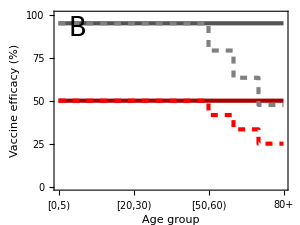

```mathematica
AgeSpecificEfficacyProfile[BaselineValue_]:={{1,BaselineValue},{7,BaselineValue},{7,BaselineValue-(BaselineValue-BaselineValue/2)/3},{8,BaselineValue-(BaselineValue-BaselineValue/2)/3},{8,BaselineValue-2(BaselineValue-BaselineValue/2)/3},{9,BaselineValue-2(BaselineValue-BaselineValue/2)/3},{9,BaselineValue/2},{10,BaselineValue/2}};
ConstantEfficacyProfile[BaselineValue_]:={{1,BaselineValue},{10,BaselineValue}};

ImSize=300;

fig1B=Show[ListLinePlot[{ConstantEfficacyProfile[95],ConstantEfficacyProfile[50],AgeSpecificEfficacyProfile[95],AgeSpecificEfficacyProfile[50]},AspectRatio->0.75,ImageSize->ImSize,Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotStyle->{{Thickness[0.01],Darker[Gray]},{Thickness[0.01],Darker[Red]},{Gray,Dashed},{Red,Dashed}},FrameLabel-> {{"Vaccine efficacy (%)",None},{"Age group",None}},PlotTheme-> "Web",PlotRange->{{1,10},{0,100}},PlotRangePadding->None,FrameTicks->{{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}},Automatic}],Graphics[Text[StyleForm["B",FontSize->26],Scaled[{0.1,0.9}]]]]

format={".pdf",".eps"};

(*Table[Export[StringJoin["Figures//Fig1B",format⟦i⟧],fig1B],{i,1,Length[format]}];*)
```

## Demography and contact matrices

Imported demography PT 10 age groups

(433332.
461299.
1.05668×10^6
1.09208×10^6
1.25045×10^6
1.57523×10^6
1.48212×10^6
1.2933×10^6
973123.
668660.)

Imported demography PT 17 age groups

(433332.
461299.
507646.
549033.
544575.
547505.
571355.
679093.
792670.
782555.
747581.
734540.
672758.
620543.
544016.
429107.
668660.)

Imported demography NL 10 age groups

(866062.
917442.
2.00833×10^6
2.20179×10^6
2.1082×10^6
2.26111×10^6
2.50839×10^6
2.08991×10^6
1.52211×10^6
798820.)

Imported demography NL 17 age groups

(866062.
917442.
956315.
1.05202×10^6
1.07993×10^6
1.12186×10^6
1.07691×10^6
1.03129×10^6
1.02539×10^6
1.23572×10^6
1.27686×10^6
1.23153×10^6
1.09684×10^6
993074.
913384.
608726.
798820.)

Imported contact matrix PT before the lockdown 16 age groups

(2.5896 | 0.804684 | 0.304764 | 0.21177 | 0.311748 | 0.615214 | 0.939848 | 0.864798 | 0.47479 | 0.25731 | 0.24719 | 0.188627 | 0.14055 | 0.1244 | 0.0854492 | 0.0483542
0.76345 | 4.5649 | 0.888805 | 0.269362 | 0.135034 | 0.411398 | 0.785379 | 0.942651 | 0.821328 | 0.318395 | 0.213586 | 0.165769 | 0.14358 | 0.120167 | 0.061128 | 0.052829
0.167434 | 1.42258 | 7.07196 | 0.767668 | 0.234083 | 0.236325 | 0.401634 | 0.78975 | 1.04906 | 0.499163 | 0.275605 | 0.138829 | 0.0864582 | 0.104991 | 0.0780326 | 0.0733984
0.0953777 | 0.257912 | 2.17437 | 7.37128 | 1.14897 | 0.621134 | 0.544085 | 0.818182 | 0.987631 | 0.876617 | 0.425816 | 0.168308 | 0.0756531 | 0.0589411 | 0.0373322 | 0.0271346
0.153111 | 0.129647 | 0.199075 | 1.74596 | 3.47483 | 1.6302 | 1.19386 | 1.12438 | 0.925029 | 1.00695 | 0.662694 | 0.317464 | 0.101728 | 0.0513646 | 0.0588598 | 0.055928
0.418154 | 0.247953 | 0.141726 | 0.717595 | 1.8876 | 3.5733 | 1.91356 | 1.56081 | 1.29163 | 1.04187 | 0.916881 | 0.429779 | 0.152563 | 0.0675958 | 0.0381027 | 0.0287432
0.635546 | 0.898539 | 0.594943 | 0.457635 | 1.05064 | 1.90297 | 3.42514 | 2.18936 | 1.5449 | 1.1811 | 0.860014 | 0.540441 | 0.246356 | 0.133965 | 0.0759401 | 0.0751264
0.628149 | 1.00728 | 0.895339 | 0.816957 | 0.765681 | 1.50023 | 2.01658 | 3.61005 | 2.21177 | 1.36726 | 0.90663 | 0.466607 | 0.315329 | 0.232461 | 0.147754 | 0.0604242
0.279968 | 0.606867 | 0.895462 | 1.0965 | 0.898423 | 1.28208 | 1.68465 | 1.94117 | 2.96267 | 1.64326 | 1.05812 | 0.353125 | 0.222011 | 0.15623 | 0.113756 | 0.0580184
0.338495 | 0.452543 | 0.550061 | 1.39677 | 0.820247 | 1.0225 | 1.31161 | 1.48116 | 1.54908 | 2.0966 | 1.04924 | 0.425332 | 0.18254 | 0.115189 | 0.108969 | 0.102342
0.209257 | 0.571576 | 0.834232 | 1.11116 | 0.859169 | 1.21903 | 1.20066 | 1.19646 | 1.52288 | 1.65086 | 1.75913 | 0.729923 | 0.289979 | 0.153368 | 0.110392 | 0.101735
0.413513 | 0.605121 | 0.55202 | 0.721731 | 0.578094 | 0.996647 | 1.12372 | 0.93767 | 0.987028 | 0.815126 | 1.01326 | 1.45752 | 0.517769 | 0.265915 | 0.146228 | 0.10414
0.352744 | 0.333317 | 0.232332 | 0.398564 | 0.35842 | 0.568112 | 0.732291 | 0.844741 | 0.639151 | 0.536874 | 0.495201 | 0.699003 | 1.25005 | 0.531536 | 0.30305 | 0.141822
0.229975 | 0.373206 | 0.313438 | 0.182838 | 0.24992 | 0.394536 | 0.659675 | 0.700445 | 0.627883 | 0.400744 | 0.41866 | 0.542889 | 0.648516 | 1.31149 | 0.381853 | 0.19945
0.129054 | 0.343935 | 0.350814 | 0.374042 | 0.175902 | 0.315424 | 0.395009 | 0.727404 | 0.684119 | 0.574224 | 0.417634 | 0.416738 | 0.738973 | 0.871931 | 1.1968 | 0.386836
0.25801 | 0.343299 | 0.506562 | 0.397087 | 0.194396 | 0.221113 | 0.417844 | 0.462229 | 0.521337 | 0.57654 | 0.555067 | 0.375617 | 0.311183 | 0.510464 | 0.460042 | 0.753576)

Imported school contact matrix PT before the lockdown 16 age groups

(1.66051 | 0.26834 | 0.0509724 | 0.0526263 | 0.0123117 | 0.0706302 | 0.15275 | 0.11822 | 0.0521619 | 0.0606281 | 0.0316418 | 0.0206473 | 0.00260088 | 0.00101002 | 8.27936×10^-66 | 6.40828×10^-120
0.335772 | 2.84217 | 0.167469 | 0.0176249 | 0.0144978 | 0.0542965 | 0.0860027 | 0.0861113 | 0.0785907 | 0.0547269 | 0.045465 | 0.0138426 | 0.00526092 | 0.00143012 | 0.000348625 | 8.1182×10^-39
0.00295165 | 0.650166 | 3.99749 | 0.117878 | 0.00971625 | 0.0444741 | 0.05507 | 0.0929602 | 0.0912733 | 0.0699409 | 0.0482956 | 0.023753 | 0.00584671 | 0.0007571 | 4.95596×10^-25 | 0.000182852
0.0168767 | 0.0265016 | 1.18128 | 3.84976 | 0.0380132 | 0.0479371 | 0.0651295 | 0.0970075 | 0.0768016 | 0.0883692 | 0.0480322 | 0.0279311 | 0.00615754 | 0.00109025 | 6.23285×10^-33 | 1.71325×10^-70
0.0165484 | 0.0115921 | 0.0048152 | 0.388773 | 0.216441 | 0.0290088 | 0.0218991 | 0.0278921 | 0.0173487 | 0.0211463 | 0.0113473 | 0.00817789 | 0.000645981 | 0.00121154 | 0.000177231 | 1.22026×10^-47
0.0227918 | 0.0756706 | 0.0249559 | 0.122587 | 0.16068 | 0.119433 | 0.0241917 | 0.033517 | 0.0384517 | 0.0333907 | 0.00870023 | 0.0139604 | 0.00457032 | 0.00245067 | 0.000463795 | 0.00128792
0.0538104 | 0.307111 | 0.213864 | 0.129597 | 0.0329953 | 0.0757203 | 0.0807013 | 0.0587282 | 0.0615074 | 0.031725 | 0.0257134 | 0.00379157 | 0.00645221 | 0.000473418 | 1.65816×10^-48 | 3.11874×10^-55
0.0951461 | 0.192073 | 0.148192 | 0.0716003 | 0.0134611 | 0.0509861 | 0.0836181 | 0.0655822 | 0.070219 | 0.0333104 | 0.00489867 | 0.0109994 | 0.000699282 | 0.00225462 | 1.84907×10^-123 | 9.71935×10^-67
0.0289698 | 0.104091 | 0.0869557 | 0.33298 | 0.00631632 | 0.0246579 | 0.0283427 | 0.040212 | 0.0832557 | 0.0294452 | 0.0326703 | 0.00884886 | 0.00682765 | 0.000514165 | 4.82359×10^-68 | 2.40772×10^-92
0.238478 | 0.229539 | 0.156428 | 0.530003 | 0.00454231 | 0.0304338 | 0.0686509 | 0.062248 | 0.0561085 | 0.0334626 | 0.0409513 | 0.0182493 | 0.00411504 | 0.00182086 | 6.22424×10^-134 | 3.2804×10^-72
0.0576784 | 0.37265 | 0.48982 | 0.497371 | 0.00460442 | 0.0154414 | 0.0500429 | 0.0517281 | 0.0623844 | 0.084589 | 0.042674 | 0.0220929 | 0.00577609 | 9.62647×10^-24 | 1.24075×10^-117 | 5.65431×10^-78
0.171177 | 0.341453 | 0.309723 | 0.334554 | 0.00537945 | 0.0582598 | 0.0258761 | 0.0452734 | 0.0554566 | 0.0399184 | 0.0347616 | 0.0377628 | 0.0109801 | 1.21328×10^-31 | 0.000783335 | 0.000763698
0.0737849 | 0.0657965 | 0.0348462 | 0.156822 | 0.0117186 | 0.00181008 | 0.0184368 | 0.0529987 | 0.0114245 | 0.0180404 | 0.0141459 | 0.00713495 | 0.0233664 | 0.0115642 | 4.42716×10^-67 | 2.12265×10^-37
0.00217706 | 0.0279268 | 0.0110222 | 7.69605×10^-32 | 0.00190096 | 0.00195541 | 0.013152 | 0.00583086 | 0.00582293 | 0.00936293 | 0.00211082 | 0.0159675 | 0.00845152 | 0.0176352 | 0.011127 | 3.45783×10^-126
1.28761×10^-28 | 5.1279×10^-26 | 1.93743×10^-40 | 0.0076306 | 2.63686×10^-22 | 1.69998×10^-24 | 1.26161×10^-26 | 0.00764088 | 0.00786849 | 0.0212029 | 0.0352907 | 0.0214737 | 0.0077468 | 0.00801554 | 0.0079129 | 0.0213827
2.82937×10^-94 | 0.0212049 | 8.49807×10^-42 | 0.0213359 | 4.90075×10^-36 | 0.00760384 | 9.79395×10^-69 | 2.23656×10^-60 | 1.4404×10^-48 | 8.57957×10^-60 | 4.70441×10^-42 | 1.6008×10^-46 | 2.21183×10^-83 | 8.86092×10^-107 | 1.02043×10^-80 | 6.61417×10^-113)

Contact matrix PT before the lockdown 10 age groups

(2.5896 | 0.804684 | 0.516534 | 0.926962 | 1.80465 | 0.7321 | 0.435817 | 0.264949 | 0.133803 | 0.0753485
0.76345 | 4.5649 | 1.15817 | 0.546432 | 1.72803 | 1.13972 | 0.379355 | 0.263747 | 0.113957 | 0.0823213
0.129995 | 0.817437 | 8.72605 | 1.14571 | 1.28017 | 1.71243 | 0.507798 | 0.161908 | 0.106246 | 0.0769165
0.285988 | 0.188959 | 1.40072 | 5.28344 | 2.89786 | 2.13328 | 1.1639 | 0.186716 | 0.0907526 | 0.0659131
0.631529 | 0.957597 | 1.41086 | 2.58013 | 5.62109 | 3.18927 | 1.38567 | 0.47127 | 0.182082 | 0.104625
0.309044 | 0.530201 | 1.96954 | 2.01271 | 3.21197 | 4.12889 | 1.44271 | 0.338244 | 0.191416 | 0.12472
0.310487 | 0.588201 | 1.61252 | 1.82869 | 2.23073 | 2.49398 | 2.48 | 0.612018 | 0.231079 | 0.160387
0.293837 | 0.352457 | 0.566304 | 0.791188 | 1.47295 | 1.1053 | 1.08257 | 1.86719 | 0.510333 | 0.264082
0.185918 | 0.343654 | 0.803696 | 0.457894 | 1.01555 | 1.18758 | 0.876842 | 1.26287 | 1.42047 | 0.854788
0.25801 | 0.343299 | 0.903648 | 0.415509 | 0.880073 | 1.09788 | 0.930684 | 0.821647 | 1.21362 | 1.17427)

School contact matrix PT before the lockdown 10 age groups

(1.66051 | 0.26834 | 0.103599 | 0.0829419 | 0.27097 | 0.11279 | 0.0522891 | 0.00361089 | 8.27936×10^-66 | 9.98576×10^-120
0.335772 | 2.84217 | 0.185094 | 0.0687943 | 0.172114 | 0.133318 | 0.0593076 | 0.00669104 | 0.000348625 | 1.26503×10^-38
0.0101869 | 0.32612 | 4.59114 | 0.0706923 | 0.15536 | 0.16327 | 0.0740826 | 0.00693841 | 0.0000878451 | 0.000136885
0.0196785 | 0.0437173 | 0.270236 | 0.262828 | 0.0537606 | 0.0552134 | 0.0210971 | 0.00444618 | 0.000966587 | 0.00100615
0.076259 | 0.244636 | 0.276299 | 0.0846743 | 0.144736 | 0.0988244 | 0.0221153 | 0.00476866 | 7.57646×10^-49 | 2.22054×10^-55
0.133051 | 0.166412 | 0.552328 | 0.0329623 | 0.0995266 | 0.10121 | 0.0503031 | 0.00664338 | 2.42744×10^-68 | 2.53944×10^-72
0.113928 | 0.357188 | 0.817242 | 0.0416507 | 0.0865949 | 0.121401 | 0.0686115 | 0.00835522 | 0.00076671 | 0.000589784
0.0394265 | 0.0476261 | 0.104992 | 0.0088878 | 0.046268 | 0.0226136 | 0.0197442 | 0.0306872 | 0.0053389 | 1.72059×10^-37
7.19829×10^-29 | 0.00935047 | 0.0136741 | 0.00335298 | 0.00427157 | 0.0162521 | 0.0317336 | 0.0088118 | 0.0163774 | 0.0186271
2.82937×10^-94 | 0.0212049 | 0.0213359 | 0.00760384 | 2.23656×10^-60 | 1.4404×10^-48 | 4.70457×10^-42 | 2.21183×10^-83 | 1.02043×10^-80 | 1.03066×10^-112)

Imported contact matrix NL before the lockdown 10 age groups

(3.49459 | 1.42731 | 1.26515 | 1.49621 | 1.96756 | 1.43407 | 0.976927 | 0.574687 | 0.198497 | 0.0610699
1.33991 | 7.87519 | 3.51819 | 1.97454 | 2.00887 | 1.87543 | 1.0857 | 0.56934 | 0.235369 | 0.0675934
0.547496 | 1.6218 | 9.37298 | 2.93988 | 1.893 | 2.14217 | 1.4002 | 0.602697 | 0.253254 | 0.100411
0.605267 | 0.850866 | 2.74815 | 4.661 | 2.52761 | 2.17794 | 1.69773 | 0.781362 | 0.338618 | 0.210781
0.837104 | 0.910422 | 1.86105 | 2.65831 | 3.6402 | 2.60697 | 1.72487 | 0.908763 | 0.404453 | 0.239114
0.530857 | 0.739517 | 1.83241 | 1.99297 | 2.26829 | 3.44006 | 1.93336 | 0.952193 | 0.462985 | 0.235091
0.344565 | 0.407904 | 1.1412 | 1.48021 | 1.42995 | 1.84211 | 2.28018 | 1.18511 | 0.54166 | 0.297305
0.240551 | 0.253858 | 0.582957 | 0.808495 | 0.894096 | 1.07671 | 1.40647 | 1.87324 | 0.915692 | 0.385562
0.125495 | 0.158515 | 0.369988 | 0.529201 | 0.601021 | 0.790737 | 0.970935 | 1.38309 | 1.99376 | 0.799441
0.0696997 | 0.0821797 | 0.264826 | 0.594672 | 0.641466 | 0.724839 | 0.962044 | 1.05132 | 1.44327 | 1.18527)

Imported contact matrix NL after the lockdown 10 age groups

(0.911111 | 0.7125 | 1.16247 | 1.0395 | 0.851587 | 0.651538 | 0.453069 | 0.218131 | 0.0792282 | 0.019646
0.672592 | 0.886057 | 1.36309 | 1.14145 | 0.906771 | 0.733406 | 0.517174 | 0.251122 | 0.0999042 | 0.028022
0.501295 | 0.622683 | 1.55959 | 1.28721 | 0.969845 | 0.812777 | 0.606975 | 0.30669 | 0.134222 | 0.0432633
0.408884 | 0.47562 | 1.17411 | 1.50641 | 1.0952 | 0.886122 | 0.699729 | 0.378278 | 0.18436 | 0.070615
0.34984 | 0.39461 | 0.923905 | 1.14381 | 1.29034 | 0.989988 | 0.777751 | 0.455424 | 0.247491 | 0.106761
0.249556 | 0.297582 | 0.72192 | 0.862875 | 0.923039 | 1.11674 | 0.870666 | 0.542549 | 0.326707 | 0.154754
0.156431 | 0.189156 | 0.485971 | 0.614202 | 0.653671 | 0.784835 | 0.961546 | 0.664486 | 0.435074 | 0.220932
0.0903923 | 0.110239 | 0.294715 | 0.398525 | 0.459408 | 0.586992 | 0.797539 | 0.82594 | 0.598574 | 0.317188
0.0450803 | 0.0602167 | 0.177097 | 0.266681 | 0.342786 | 0.485324 | 0.716981 | 0.821863 | 0.868945 | 0.478011
0.0213 | 0.0321833 | 0.10877 | 0.194628 | 0.281751 | 0.438032 | 0.693735 | 0.829841 | 0.910856 | 0.692005)

Ratio of contacts after and before the lockdown NL 10 age groups

(0.26072 | 0.499189 | 0.918835 | 0.694753 | 0.432813 | 0.454329 | 0.46377 | 0.379565 | 0.39914 | 0.321697
0.501967 | 0.112512 | 0.38744 | 0.578082 | 0.451385 | 0.39106 | 0.47635 | 0.441075 | 0.424457 | 0.414567
0.915614 | 0.383947 | 0.166392 | 0.437843 | 0.512333 | 0.379418 | 0.433491 | 0.508863 | 0.529989 | 0.430863
0.675543 | 0.558984 | 0.427235 | 0.323195 | 0.433293 | 0.406863 | 0.412156 | 0.484126 | 0.544447 | 0.335016
0.417917 | 0.433437 | 0.496442 | 0.430278 | 0.354469 | 0.379746 | 0.450905 | 0.501147 | 0.611916 | 0.446486
0.4701 | 0.4024 | 0.393973 | 0.43296 | 0.406931 | 0.324627 | 0.450339 | 0.569789 | 0.705654 | 0.658272
0.453996 | 0.463728 | 0.425843 | 0.414944 | 0.457129 | 0.426053 | 0.421697 | 0.560696 | 0.803223 | 0.743116
0.375771 | 0.434253 | 0.505552 | 0.492922 | 0.513824 | 0.545172 | 0.567048 | 0.440915 | 0.653685 | 0.822664
0.35922 | 0.379879 | 0.478655 | 0.503931 | 0.57034 | 0.613761 | 0.738444 | 0.594222 | 0.435833 | 0.597932
0.305596 | 0.391621 | 0.410724 | 0.327286 | 0.43923 | 0.604317 | 0.721105 | 0.78933 | 0.631104 | 0.583838)

Contact matrix PT after the lockdown 10 age groups

(0.675162 | 0.40169 | 0.474609 | 0.64401 | 0.781074 | 0.332614 | 0.202119 | 0.100565 | 0.0534064 | 0.0242394
0.383227 | 0.513608 | 0.44872 | 0.315882 | 0.780006 | 0.4457 | 0.180706 | 0.116332 | 0.0483698 | 0.0341277
0.119025 | 0.313852 | 1.45195 | 0.501642 | 0.655874 | 0.649725 | 0.220126 | 0.0823892 | 0.0563092 | 0.0331404
0.193197 | 0.105625 | 0.598438 | 1.70759 | 1.25562 | 0.867952 | 0.479708 | 0.0903939 | 0.04941 | 0.0220819
0.263926 | 0.415058 | 0.700409 | 1.11017 | 1.9925 | 1.21111 | 0.624807 | 0.236175 | 0.111419 | 0.0467134
0.145281 | 0.213353 | 0.775946 | 0.871424 | 1.30705 | 1.34035 | 0.649707 | 0.192728 | 0.135073 | 0.0820994
0.14096 | 0.272765 | 0.686682 | 0.758802 | 1.01973 | 1.06257 | 1.04581 | 0.343156 | 0.185608 | 0.119186
0.110416 | 0.153055 | 0.286296 | 0.389994 | 0.756839 | 0.602579 | 0.613871 | 0.823274 | 0.333597 | 0.217251
0.0667855 | 0.130547 | 0.384693 | 0.230747 | 0.579209 | 0.728893 | 0.647498 | 0.750427 | 0.619089 | 0.511105
0.0788469 | 0.134443 | 0.37115 | 0.13599 | 0.386555 | 0.663465 | 0.671121 | 0.648551 | 0.76592 | 0.685582)

Plotting contact matrices

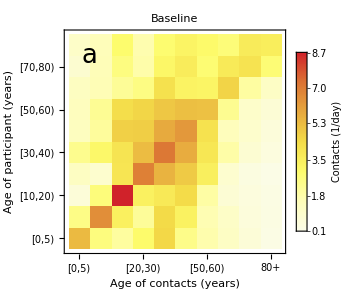

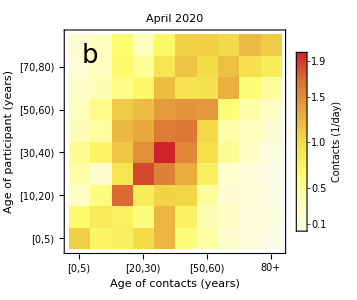

```mathematica
Print[Style["Imported demography PT 10 age groups",18,Blue,"Text"]]
DemographyData10=Flatten[Import["Data//DEMOGRAPHY PT 10.xlsx"]];
DemographyData10//MatrixForm

NumAgeGroups = 10;
AgeGroups= Table[k, {k, 1, NumAgeGroups}];
Demography:=Table[Subscript[NN,k]-> DemographyData10⟦k⟧,{k,AgeGroups}];
AgeLabel={"[0,5) y.o.","[5,10) y.o.","[10,20) y.o.","[20,30) y.o.","[30,40) y.o.","[40,50) y.o.", "[50,60) y.o.","[60,70) y.o.","[70,80) y.o.","80+ y.o."};

AgeLabelShort={"[0,5)","[5,10)","[10,20)","[20,30)","[30,40)","[40,50)","[50,60)","[60,70)","[70,80)","80+"};

Print[Style["Imported demography PT 17 age groups",18,Blue,"Text"]];
DemographyData17=Flatten[Import["Data//DEMOGRAPHY PT 17.xlsx"]];
DemographyData17//MatrixForm

Print[Style["Imported demography NL 10 age groups",18,Blue,"Text"]]
DemographyData10NL=Flatten[Import["Data//DEMOGRAPHY NL 10.xlsx"]];
DemographyData10NL//MatrixForm

Print[Style["Imported demography NL 17 age groups",18,Blue,"Text"]];
DemographyData17NL=Flatten[Import["Data//DEMOGRAPHY NL 17.xlsx"]];
DemographyData17NL//MatrixForm

Print[Style["Imported contact matrix PT before the lockdown 16 age groups",18,Blue,"Text"]];
ContactDataPTBefore16=Import["Data//CONTACT MATRIX PT BEFORE 16.xlsx"]⟦1⟧;
ContactDataPTBefore16//MatrixForm

Print[Style["Imported school contact matrix PT before the lockdown 16 age groups",18,Blue,"Text"]];
SchoolContactDataPTBefore16=Import["Data//SCHOOL CONTACT MATRIX PT BEFORE 16.xlsx"]⟦1⟧;
SchoolContactDataPTBefore16//MatrixForm

(*Print[Style["Function transforming a contact matrix with 16 age groups into a matrix with 10 age groups",18,Blue,"Text"]];*)
MatrixTransform16to10[ContactMatrix16_]:=Block[{ContactMatrix10},
ContactMatrix10=ContactMatrix16;
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10]; 

ContactMatrix10=Join[ContactMatrix10,{ContactMatrix10⟦16,All⟧}];
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10];

ContactMatrix10=Join[ContactMatrix10,List/@(ContactMatrix10⟦All,16⟧ DemographyData17⟦17⟧/DemographyData17⟦16⟧),2] ;
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10];

ContactMatrix10=Transpose[{ContactMatrix10⟦All,1⟧,ContactMatrix10⟦All,2⟧,ContactMatrix10⟦All,3⟧+ContactMatrix10⟦All,4⟧,ContactMatrix10⟦All,5⟧+ContactMatrix10⟦All,6⟧,ContactMatrix10⟦All,7⟧+ContactMatrix10⟦All,8⟧,ContactMatrix10⟦All,9⟧+ContactMatrix10⟦All,10⟧,ContactMatrix10⟦All,11⟧+ContactMatrix10⟦All,12⟧,ContactMatrix10⟦All,13⟧+ContactMatrix10⟦All,14⟧,ContactMatrix10⟦All,15⟧+ContactMatrix10⟦All,16⟧,ContactMatrix10⟦All,17⟧}];
ContactMatrix10//MatrixForm;
Dimensions[ContactMatrix10];

ContactMatrix10={ContactMatrix10⟦1,All⟧,ContactMatrix10⟦2,All⟧,(ContactMatrix10⟦3,All⟧ DemographyData17⟦3⟧+ContactMatrix10⟦4,All⟧ DemographyData17⟦4⟧)/(DemographyData17⟦3⟧+DemographyData17⟦4⟧),(ContactMatrix10⟦5,All⟧ DemographyData17⟦5⟧+ContactMatrix10⟦6,All⟧ DemographyData17⟦6⟧)/(DemographyData17⟦5⟧+DemographyData17⟦6⟧),
(ContactMatrix10⟦7,All⟧ DemographyData17⟦7⟧+ContactMatrix10⟦8,All⟧ DemographyData17⟦8⟧)/(DemographyData17⟦7⟧+DemographyData17⟦8⟧),
(ContactMatrix10⟦9,All⟧ DemographyData17⟦9⟧+ContactMatrix10⟦10,All⟧ DemographyData17⟦10⟧)/(DemographyData17⟦9⟧+DemographyData17⟦10⟧),
(ContactMatrix10⟦11,All⟧ DemographyData17⟦11⟧+ContactMatrix10⟦12,All⟧ DemographyData17⟦12⟧)/(DemographyData17⟦11⟧+DemographyData17⟦12⟧),
(ContactMatrix10⟦13,All⟧ DemographyData17⟦13⟧+ContactMatrix10⟦14,All⟧ DemographyData17⟦14⟧)/(DemographyData17⟦13⟧+DemographyData17⟦14⟧),
(ContactMatrix10⟦15,All⟧ DemographyData17⟦15⟧+ContactMatrix10⟦16,All⟧ DemographyData17⟦16⟧)/(DemographyData17⟦15⟧+DemographyData17⟦16⟧),ContactMatrix10⟦17,All⟧};

Dimensions[ContactMatrix10];
ContactMatrix10//MatrixForm;
ContactMatrix10
];

Print[Style["Contact matrix PT before the lockdown 10 age groups",18,Green,"Text"]];
ContactDataPTBefore10=MatrixTransform16to10[ContactDataPTBefore16];
ContactDataPTBefore10//MatrixForm
(*Export["Data//CONTACT MATRIX PT BEFORE 10.csv",ContactDataPTBefore10,"Table"]*)

Print[Style["School contact matrix PT before the lockdown 10 age groups",18,Green,"Text"]];
SchoolContactDataPTBefore10=MatrixTransform16to10[SchoolContactDataPTBefore16];
SchoolContactDataPTBefore10//MatrixForm
(*Export["Data//SCHOOL CONTACT MATRIX PT BEFORE 10.csv",SchoolContactDataPTBefore10,"Table"]*)

Print[Style["Imported contact matrix NL before the lockdown 10 age groups",18,Blue,"Text"]];
ContactDataNLBefore10=Import["Data//CONTACT MATRIX NL BEFORE 10.csv"];
ContactDataNLBefore10//MatrixForm

Print[Style["Imported contact matrix NL after the lockdown 10 age groups",18,Blue,"Text"]];
ContactDataNLAfter10=Import["Data//CONTACT MATRIX NL AFTER 10.csv"];
ContactDataNLAfter10//MatrixForm

Print[Style["Ratio of contacts after and before the lockdown NL 10 age groups",18,Blue,"Text"]];
RatioContactsAfterAndBeforeNL10=ContactDataNLAfter10/ContactDataNLBefore10;
RatioContactsAfterAndBeforeNL10//MatrixForm

Print[Style["Contact matrix PT after the lockdown 10 age groups",18,Green,"Text"]];
ContactDataPTAfter10=ContactDataPTBefore10 RatioContactsAfterAndBeforeNL10 ;
ContactDataPTAfter10//MatrixForm
(*Export["Data//CONTACT MATRIX PT AFTER 10.csv",ContactDataPTAfter10,"Table"]*)

ImSize=300;

Print[Style["Plotting contact matrices",18,Blue,"Text"]]

PlotContactMatrix[matrix_,label_,panel_]:=Show[MatrixPlot[matrix,FrameStyle->Opacity[0],FrameLabel->{Style["Age of participant (years)",Black,17,Opacity[1]],Style["Age of contacts (years)",Black,17,Opacity[1]]}, PlotLabel->Style[Row[{label}],Black,17],ClippingStyle->Automatic,DataReversed->{True,False},(*Mesh->True,*)Frame->True,PlotTheme-> "Web",FrameTicks->{{{1,"[0,5)",0},{2,"[5,10)",0},{3,"[10,20)",0},{4,"[20,30)",0},{5,"[30,40)",0},{6,"[40,50)",0},{7,"[50,60)",0},{8,"[60,70)",0},{9,"[70,80)",0},{10,"80+",0}},{{1,Rotate["[0,5)",Pi/2],0},{2,Rotate["[5,10)",Pi/2],0},{3,Rotate["[10,20)",Pi/2],0},{4,Rotate["[20,30)",Pi/2],0},{5,Rotate["[30,40)",Pi/2],0},{6,Rotate["[40,50)",Pi/2],0},{7,Rotate["[50,60)",Pi/2],0},{8,Rotate["[60,70)",Pi/2],0},{9,Rotate["[70,80)",Pi/2],0},{10,Rotate["80+",Pi/2],0}}},FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImageSize->ImSize,ColorFunction->"TemperatureMap",PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["Contacts\n(1/day)",Black,17],LabelStyle->Directive[Black,14(*,Opacity[1],"Helvetica"*)]],{After,Top}]],Graphics[Text[StyleForm[panel,FontSize->26],{10*0.1,10*0.9}]]]

FigContactMatrixBefore=PlotContactMatrix[ContactDataPTBefore10,"Baseline","a"]
FigContactMatrixAfter=PlotContactMatrix[ContactDataPTAfter10,"April 2020","b"]

format={".pdf",".eps"};
FigNames={"SFig1A","SFig1B"};
Figures={FigContactMatrixBefore,FigContactMatrixAfter};
(*Table[Export[StringJoin["Figures//",FigNames⟦j⟧,format⟦i⟧],Figures⟦j⟧],{i,1,Length[format]},{j,1,Length[FigNames]}]*)
```

## Comparison of contact matrices for PT and NL

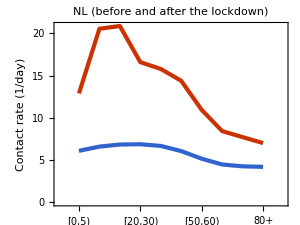

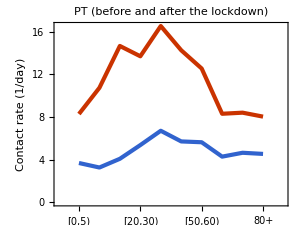

Contact rate before, after and the ratio of the two, PT

{12.1555,5.0685,0.416973}

Contact rate before, after and the ratio of the two, NL

{13.7007,5.79766,0.423164}

```mathematica
CalculateContactsAgeGroups[Matrix10_]:=Table[Total[Matrix10⟦k,All⟧],{k,AgeGroups}];

ContactsAgeGroupsNLBefore=CalculateContactsAgeGroups[ContactDataNLBefore10];
ContactsAgeGroupsPTBefore=CalculateContactsAgeGroups[ContactDataPTBefore10];

ContactsAgeGroupsNLAfter=CalculateContactsAgeGroups[ContactDataNLAfter10];
ContactsAgeGroupsPTAfter=CalculateContactsAgeGroups[ContactDataPTAfter10];

PrintContacts[Before_,After_,Country_]:=ListLinePlot[{Before,After},AspectRatio->0.75,ImageSize->ImSize,PlotRange-> {{0,11},{0,Automatic}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Contact rate (1/day)",None},{None,None}},PlotRange->All,PlotRangePadding->None,PlotTheme-> "Web",PlotLabel->Style[Row[{Country}],Black,17],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},FrameTicks->{{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}},Automatic}]

PrintContacts[ContactsAgeGroupsNLBefore,ContactsAgeGroupsNLAfter,"NL (before and after the lockdown)"]
PrintContacts[ContactsAgeGroupsPTBefore,ContactsAgeGroupsPTAfter,"PT (before and after the lockdown)"]

CalculateAverageContactRate[Demography_,ContactsAgeGroups_]:=Sum[ContactsAgeGroups⟦k⟧ Demography⟦k⟧/Total[Demography],{k,AgeGroups}];

ContactsPTBeforeTotal=CalculateAverageContactRate[DemographyData10,ContactsAgeGroupsPTBefore];
ContactsPTAfterTotal=CalculateAverageContactRate[DemographyData10,ContactsAgeGroupsPTAfter];

ContactsNLBeforeTotal=CalculateAverageContactRate[DemographyData10NL,ContactsAgeGroupsNLBefore];
ContactsNLAfterTotal=CalculateAverageContactRate[DemographyData10NL,ContactsAgeGroupsNLAfter];

Print[Style["Contact rate before, after and the ratio of the two, PT",18,Blue,"Text"]];
{ContactsPTBeforeTotal,ContactsPTAfterTotal,ContactsPTAfterTotal/ContactsPTBeforeTotal}

Print[Style["Contact rate before, after and the ratio of the two, NL",18,Blue,"Text"]];
{ContactsNLBeforeTotal,ContactsNLAfterTotal,ContactsNLAfterTotal/ContactsNLBeforeTotal}
```

## PT contact matrix by Vespignani et al 85 x 85

Imported demography PT 85 age groups

1.02863×10^7

9.554777×10^6

Imported contact matrix PT before the lockdown 85 age groups

Imported school contact matrix PT before the lockdown 85 age groups

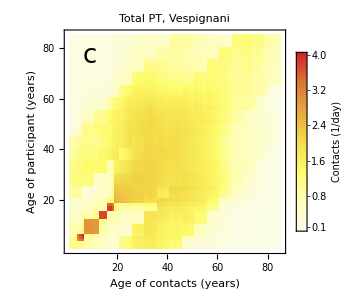

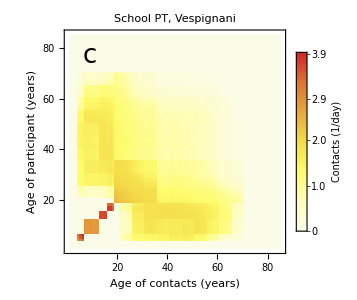

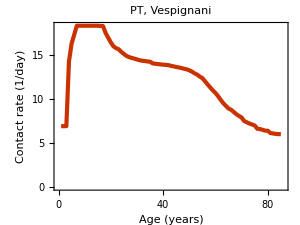

```mathematica
Print[Style["Imported demography PT 85 age groups",18,Blue,"Text"]];
DemographyData85=Import["Data//Portugal_country_level_age_distribution_85.csv"]⟦All,2⟧;
DemographyData85//MatrixForm;

Total[DemographyData10]
Total[DemographyData85]

Print[Style["Imported contact matrix PT before the lockdown 85 age groups",18,Blue,"Text"]];
ContactDataPTBefore85=Import["Data//Portugal_country_level_M_overall_contact_matrix_85.csv"];
ContactDataPTBefore85//MatrixForm;

Print[Style["Imported school contact matrix PT before the lockdown 85 age groups",18,Blue,"Text"]];
SchoolContactDataPTBefore85= 11.41 Import["Data//Portugal_country_level_F_school_setting_85.csv"];
SchoolContactDataPTBefore85//MatrixForm;

Show[MatrixPlot[ContactDataPTBefore85,FrameStyle->Opacity[0],FrameLabel->{Style["Age of participant (years)",Black,17,Opacity[1]],Style["Age of contacts (years)",Black,17,Opacity[1]]}, PlotLabel->Style[Row[{"Total PT, Vespignani"}],Black,17],ClippingStyle->Automatic,DataReversed->{True,False},Mesh->None,Frame->True,PlotTheme-> "Web"(*,FrameTicks->{{{1,"[0,5)"},{2,"[5,10)"},{3,"[10,20)"},{4,"[20,30)"},{5,"[30,40)"},{6,"[40,50)"},{7,"[50,60)"},{8,"[60,70)"},{9,"[70,80)"},{10,"80+"}},{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}}}*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImageSize->ImSize,ColorFunction->"TemperatureMap",PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["Contacts\n(1/day)",Black,17],LabelStyle->Directive[Black,14,Opacity[1]]],{After,Top}]],Graphics[Text[StyleForm["c",FontSize->26],{85*0.1,85*0.9}]]]

Show[MatrixPlot[SchoolContactDataPTBefore85,FrameStyle->Opacity[0],FrameLabel->{Style["Age of participant (years)",Black,17,Opacity[1]],Style["Age of contacts (years)",Black,17,Opacity[1]]}, PlotLabel->Style[Row[{"School PT, Vespignani"}],Black,17],ClippingStyle->Automatic,DataReversed->{True,False},Mesh->None,Frame->True,PlotTheme-> "Web"(*,FrameTicks->{{{1,"[0,5)"},{2,"[5,10)"},{3,"[10,20)"},{4,"[20,30)"},{5,"[30,40)"},{6,"[40,50)"},{7,"[50,60)"},{8,"[60,70)"},{9,"[70,80)"},{10,"80+"}},{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}}}*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImageSize->ImSize,ColorFunction->"TemperatureMap",PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->250,LegendLabel->Style["Contacts\n(1/day)",Black,17],LabelStyle->Directive[Black,14,Opacity[1]]],{After,Top}]],Graphics[Text[StyleForm["c",FontSize->26],{85*0.1,85*0.9}]]]

CalculateContactsAgeGroups2=Table[Total[ContactDataPTBefore85⟦k,All⟧],{k,85}];

ListLinePlot[CalculateContactsAgeGroups2,AspectRatio->0.75,ImageSize->ImSize,PlotRange-> {{0,86},{0,Automatic}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],PlotTheme-> "Web",FrameLabel-> {{"Contact rate (1/day)",None},{"Age (years)",None}},PlotRange->All,PlotRangePadding->None,PlotLabel->Style[Row[{"PT, Vespignani"}],Black,17],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}}]
```

## PT contact matrix by Vespignani et al 10 x 10

Contact matrix PT before the lockdown 10 age groups Vespignani

(2.54599 | 1.79557 | 0.597741 | 1.58124 | 1.88037 | 0.976327 | 0.37358 | 0.285957 | 0.228345 | 0.158905
1.66701 | 7.00627 | 3.50534 | 1.12103 | 2.02307 | 1.60218 | 0.570874 | 0.30405 | 0.228345 | 0.158905
0.277096 | 1.7503 | 7.92572 | 1.77052 | 2.18543 | 2.00318 | 1.28105 | 0.368414 | 0.243935 | 0.163057
0.591971 | 0.45205 | 1.42984 | 3.86932 | 2.78535 | 2.57546 | 1.94659 | 0.985505 | 0.3383 | 0.187177
0.60404 | 0.699997 | 1.5144 | 2.39 | 2.96178 | 2.49673 | 1.84907 | 1.00521 | 0.525449 | 0.191036
0.341158 | 0.603025 | 1.50995 | 2.40387 | 2.71588 | 2.50389 | 1.81707 | 0.969533 | 0.549773 | 0.408321
0.155063 | 0.255228 | 1.14703 | 2.15821 | 2.38921 | 2.15841 | 1.8196 | 1.19895 | 0.620215 | 0.333587
0.145453 | 0.166582 | 0.404239 | 1.33899 | 1.59168 | 1.41131 | 1.46925 | 1.21007 | 1.00448 | 0.523675
0.144409 | 0.155546 | 0.332783 | 0.571482 | 1.03446 | 0.995011 | 0.944983 | 1.24889 | 1.10364 | 0.869867
0.144409 | 0.155546 | 0.319654 | 0.454369 | 0.540446 | 1.06194 | 0.730372 | 0.935621 | 1.24999 | 0.979677)

Contact matrix PT after the lockdown 10 age groups Vespignani

(0.66379 | 0.896331 | 0.549225 | 1.09857 | 0.813849 | 0.443574 | 0.173255 | 0.108539 | 0.0911416 | 0.0511191
0.836786 | 0.788293 | 1.35811 | 0.648049 | 0.913181 | 0.626547 | 0.271936 | 0.134109 | 0.0969225 | 0.0658767
0.253713 | 0.672021 | 1.31878 | 0.775213 | 1.11967 | 0.760043 | 0.555326 | 0.187472 | 0.129283 | 0.070255
0.399902 | 0.252689 | 0.610879 | 1.25055 | 1.20687 | 1.04786 | 0.802298 | 0.477108 | 0.184186 | 0.0627074
0.252438 | 0.303404 | 0.751813 | 1.02836 | 1.04986 | 0.948123 | 0.833753 | 0.50376 | 0.321531 | 0.0852948
0.160378 | 0.242657 | 0.594879 | 1.04078 | 1.10517 | 0.81283 | 0.818297 | 0.552429 | 0.38795 | 0.268786
0.0703978 | 0.118356 | 0.488453 | 0.895535 | 1.09218 | 0.919597 | 0.76732 | 0.672245 | 0.498172 | 0.247894
0.0546569 | 0.0723389 | 0.204364 | 0.660016 | 0.817845 | 0.769406 | 0.833138 | 0.533537 | 0.656613 | 0.430808
0.0518747 | 0.0590889 | 0.159288 | 0.287988 | 0.589993 | 0.610699 | 0.697817 | 0.74212 | 0.481003 | 0.520121
0.044131 | 0.0609153 | 0.131289 | 0.148709 | 0.23738 | 0.641748 | 0.526675 | 0.738514 | 0.788875 | 0.571973)

School contact matrix PT before the lockdown 10 age groups Vespignani

(1.94146 | 1.29028 | 0. | 0.0253809 | 0.0592522 | 0.0914605 | 0.0256729 | 0.00205149 | 0. | 0.
1.1979 | 6.37547 | 2.70494 | 0.104617 | 0.287726 | 0.286894 | 0.22302 | 0.0201486 | 0. | 0.
0. | 1.35064 | 6.80854 | 0.924351 | 0.487979 | 0.356924 | 0.222397 | 0.0313604 | 0. | 0.
0.00950192 | 0.0421863 | 0.746488 | 1.42563 | 0.246543 | 0.0608675 | 0.0355611 | 0.0120944 | 0. | 0.
0.0190338 | 0.0995556 | 0.338147 | 0.211549 | 0.0497481 | 0.0220656 | 0.0135955 | 0.00271788 | 0. | 0.
0.0319591 | 0.107981 | 0.269041 | 0.0568123 | 0.0240024 | 0.0167527 | 0.0104474 | 0.0014702 | 0. | 0.
0.0106561 | 0.0997085 | 0.199129 | 0.0394271 | 0.0175669 | 0.01241 | 0.00829965 | 0.00111587 | 0. | 0.
0.00104349 | 0.011039 | 0.0344099 | 0.0164324 | 0.00430357 | 0.00214012 | 0.00136745 | 0.00023978 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

Plotting contact matrices

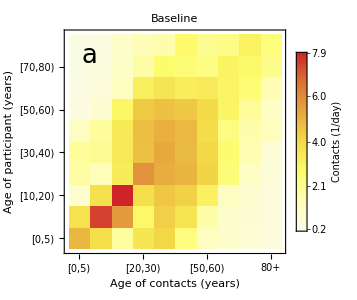
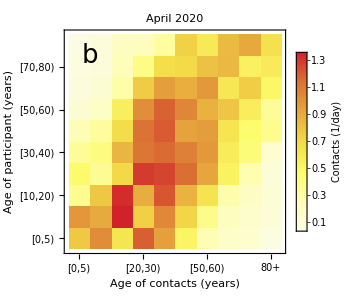
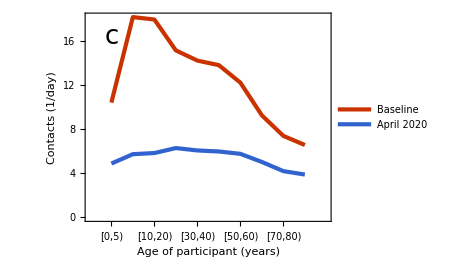
-Graphics- | -Graphics-
-Graphics- |

{12.6132,5.50154,0.436173}

```mathematica
ListTransform86to10[list85_]:=Total/@Join[Partition[list85,5]⟦1;;2⟧,Partition[list85,10]⟦2;;⟧,{list85⟦81;;⟧}];
(*Demography10Test= Join[Partition[Range[0,85],5]⟦1;;2⟧,Partition[Range[0,85],10]⟦2;;⟧,{Range[0,85]⟦81;;⟧}];*)

(* https://www.pordata.pt/Portugal/Popula%C3%A7%C3%A3o+residente++m%C3%A9dia+anual+total+e+por+grupo+et%C3%A1rio-10 *)
DemographyData86=Append[DemographyData85,316442];
DemographyData10Vespignani=ListTransform86to10[DemographyData86];

(*Export["Data//DEMOGRAPHY PT 86 V.csv",DemographyData86,"Table"]

Export["Data//DEMOGRAPHY PT 10 V.csv",DemographyData10Vespignani,"Table"]*)

(* Join[{v},m]//MatrixForm - join a row v to matrix m
Join[List/@v,m,2]//MatrixForm - join a column v to matrix m *)

ContactDataPTBefore86x85=Join[ContactDataPTBefore85,{ContactDataPTBefore85⟦85⟧}];
(*ContactDataPTBefore86x85//Dimensions
ContactDataPTBefore86x85//MatrixForm*)
ContactDataPTBefore86x86=Join[ContactDataPTBefore86x85,List/@(ContactDataPTBefore86x85⟦All,85⟧ DemographyData86⟦86⟧/DemographyData86⟦85⟧), 2];
(*ContactDataPTBefore86x86//Dimensions
ContactDataPTBefore86x86//MatrixForm*)
(*Export["Data//CONTACT MATRIX PT BEFORE 86 V.csv",ContactDataPTBefore86x86,"Table"]*)


Print[Style["Contact matrix PT before the lockdown 10 age groups Vespignani",18,Red,"Text"]];
ContactDataPTBefore10Vespignani=ListTransform86to10[ Transpose[ListTransform86to10[Transpose[ContactDataPTBefore86x86]]] DemographyData86]/DemographyData10Vespignani;
ContactDataPTBefore10Vespignani//MatrixForm
(*Export["Data//CONTACT MATRIX PT BEFORE 10 V.csv",ContactDataPTBefore10Vespignani,"Table"]*)

Print[Style["Contact matrix PT after the lockdown 10 age groups Vespignani",18,Red,"Text"]];
ContactDataPTAfter10Vespignani=ContactDataPTBefore10Vespignani RatioContactsAfterAndBeforeNL10 ;
ContactDataPTAfter10Vespignani//MatrixForm
(*Export["Data//CONTACT MATRIX PT AFTER 10 V.csv",ContactDataPTAfter10Vespignani,"Table"]*)

Print[Style["School contact matrix PT before the lockdown 10 age groups Vespignani",18,Red,"Text"]];

SchoolContactDataPTBefore86x85=Join[SchoolContactDataPTBefore85,{SchoolContactDataPTBefore85⟦85⟧}];
(*SchoolContactDataPTBefore86x85//Dimensions
SchoolContactDataPTBefore86x85//MatrixForm*)
SchoolContactDataPTBefore86x86=Join[SchoolContactDataPTBefore86x85,List/@(SchoolContactDataPTBefore86x85⟦All,85⟧ DemographyData86⟦86⟧/DemographyData86⟦85⟧), 2];
(*ContactDataPTBefore86x86//Dimensions
ContactDataPTBefore86x86//MatrixForm*)
(*Export["Data//SCHOOL CONTACT MATRIX PT BEFORE 86 V.csv",SchoolContactDataPTBefore86x86,"Table"]*)

SchoolContactDataPTBefore10Vespignani=ListTransform86to10[ Transpose[ListTransform86to10[Transpose[SchoolContactDataPTBefore86x86]]] DemographyData86]/DemographyData10Vespignani;
SchoolContactDataPTBefore10Vespignani//MatrixForm
(*Export["Data//SCHOOL CONTACT MATRIX PT BEFORE 10 V.csv",SchoolContactDataPTBefore10Vespignani,"Table"]*)

Print[Style["Plotting contact matrices",18,Blue,"Text"]]

FigContactMatrixBeforeV=PlotContactMatrix[ContactDataPTBefore10Vespignani,"Baseline","a"];
FigContactMatrixAfterV=PlotContactMatrix[ContactDataPTAfter10Vespignani,"April 2020","b"];
FigSchoolContactMatrixBeforeV=PlotContactMatrix[SchoolContactDataPTBefore10Vespignani,"Baseline: school contacts","b"];

format={".pdf",".eps"};
FigNames={"SFig1A","SFig1B","SFig1C"};
Figures={FigContactMatrixBeforeV,FigSchoolContactMatrixBeforeV,FigContactMatrixAfterV};
(*Table[Export[StringJoin["Figures//",FigNames⟦j⟧,format⟦i⟧],Figures⟦j⟧],{i,1,Length[format]},{j,1,Length[FigNames]}]*)

BeforeAfterLegends=Style[#,Black]&/@{"Baseline","April 2020"};

PrintContactsPaper[Before_,After_]:=Show[ListLinePlot[{Before,After},AspectRatio->0.75,ImageSize->350,PlotRange-> {{0,11},{0,Automatic}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Contacts (1/day)",None},{"Age of participant (years)",None}},PlotRange->All,PlotRangePadding->None,PlotTheme-> "Web"(*,PlotLabel->Style[Row[{Country}],Black,17]*),FrameTicks->{{{1,Rotate["[0,5)",Pi/2]},{2,Rotate["[5,10)",Pi/2]},{3,Rotate["[10,20)",Pi/2]},{4,Rotate["[20,30)",Pi/2]},{5,Rotate["[30,40)",Pi/2]},{6,Rotate["[40,50)",Pi/2]},{7,Rotate["[50,60)",Pi/2]},{8,Rotate["[60,70)",Pi/2]},{9,Rotate["[70,80)",Pi/2]},{10,Rotate["80+",Pi/2]}},Automatic},PlotLegends->Placed[BeforeAfterLegends,Scaled[{{1,1}, {1,1 }}]],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{Automatic,20},{Automatic,30}}],Graphics[Text[StyleForm["c",FontSize->26],{10*0.1,Max[Before]*0.9}]]]


ContactsAgeGroupsPTBeforeV=CalculateContactsAgeGroups[ContactDataPTBefore10Vespignani];
ContactsAgeGroupsPTAfterV=CalculateContactsAgeGroups[ContactDataPTAfter10Vespignani];

FigBeforeAfter=PrintContactsPaper[ContactsAgeGroupsPTBeforeV,ContactsAgeGroupsPTAfterV];

(*SFig2=Grid[{{FigContactMatrixBeforeV,FigSchoolContactMatrixBeforeV}}]
Table[Export[StringJoin["Figures//SFig2",format⟦i⟧],SFig2],{i,1,Length[format]}]

SFig3=Grid[{{FigBeforeAfter,FigContactMatrixAfterV}}]
Table[Export[StringJoin["Figures//SFig3",format⟦i⟧],SFig3],{i,1,Length[format]}]*)

SFig2=Grid[{{FigContactMatrixBeforeV,FigContactMatrixAfterV},{FigBeforeAfter,SpanFromLeft}}]
(*Table[Export[StringJoin["Figures//SFig2",format⟦i⟧],SFig2],{i,1,Length[format]}]*)

(*ContactsPTBeforeTotalV=CalculateAverageContactRate[DemographyData10Vespignani,ContactsAgeGroupsPTBeforeV];
ContactsPTAfterTotalV=CalculateAverageContactRate[DemographyData10Vespignani,ContactsAgeGroupsPTAfterV];
{ContactsPTBeforeTotalV,ContactsPTAfterTotalV,ContactsPTAfterTotalV/ContactsPTBeforeTotalV}*)

ContactsPTBeforeTotalV=CalculateAverageContactRate[DemographyData10,ContactsAgeGroupsPTBeforeV];
ContactsPTAfterTotalV=CalculateAverageContactRate[DemographyData10,ContactsAgeGroupsPTAfterV];
{ContactsPTBeforeTotalV,ContactsPTAfterTotalV,ContactsPTAfterTotalV/ContactsPTBeforeTotalV}
```

## Serological data

```mathematica
(* 
Grupo etário (anos)
1-9 
10-19 
20-39
40-59
≥60 
*)
```

```mathematica
TotalSamples5={404,377,377,479,664};

Total[TotalSamples5]

PositivePecentage5={2.9,2.2,2.9,3.2,2.9}/100;

Round[TotalSamples5 PositivePecentage5]

SamplesTransform5to10[Variable5_]:=Round[{Variable5⟦1⟧ DemographyData17⟦1⟧/(DemographyData17⟦1⟧+DemographyData17⟦2⟧),Variable5⟦1⟧ DemographyData17⟦2⟧/(DemographyData17⟦1⟧+DemographyData17⟦2⟧),Variable5⟦2⟧,Variable5⟦3⟧ DemographyData10⟦4⟧/(DemographyData10⟦4⟧+DemographyData10⟦5⟧),Variable5⟦3⟧ DemographyData10⟦5⟧/(DemographyData10⟦4⟧+DemographyData10⟦5⟧),Variable5⟦4⟧ DemographyData10⟦6⟧/(DemographyData10⟦6⟧+DemographyData10⟦7⟧),Variable5⟦4⟧ DemographyData10⟦7⟧/(DemographyData10⟦6⟧+DemographyData10⟦7⟧),Variable5⟦5⟧ DemographyData10⟦8⟧/(DemographyData10⟦8⟧+DemographyData10⟦9⟧+DemographyData10⟦10⟧),Variable5⟦5⟧ DemographyData10⟦9⟧/(DemographyData10⟦8⟧+DemographyData10⟦9⟧+DemographyData10⟦10⟧),Variable5⟦5⟧ DemographyData10⟦10⟧/(DemographyData10⟦8⟧+DemographyData10⟦9⟧+DemographyData10⟦10⟧)}];

SamplesTransform5to10[TotalSamples5]

SamplesTransform5to10[TotalSamples5 PositivePecentage5]
```

2301

{12,8,11,15,19}

{196,208,377,176,201,247,232,293,220,151}

{6,6,8,5,6,8,7,8,6,4}

## Important dates

```mathematica
Print[Style["Important dates",18,Blue,"Text"]]
Print[Style["Date of starting simulations",18,Blue,"Text"]]
DateObject[{2020, 02, 25}]
t0=0

Print[Style["Date of the start of the pandemic",18,Blue,"Text"]]
DateObject[{2020, 02, 26}]

Print[Style["Date of starting vaccination",18,Blue,"Text"]]
(*tstartvac=255;*)
DateObject[{2020, 12, 27}]
tstartvac=Differences[{DateObject[{2020, 02, 26}],DateObject[{2020, 12, 27}]}]⟦1,1⟧+1

Print[Style["Date of ending vaccination",18,Blue,"Text"]]
(*DateObject[{2021, 07, 31}]*)
DateObject[{2021, 12, 31}]
tendvac=Differences[{DateObject[{2020, 02, 26}],DateObject[{2021,12,31}](*DateObject[{2021, 07, 31}]*)}]⟦1,1⟧+1+10(*days extra*) (* DateObject[{2021, 12, 31}] *)

Print[Style["Last hospitalization date",18,Blue,"Text"]]

tenddata=Differences[{DateObject[{2020, 02, 26}],DateObject[{2021,01,15}]}]⟦1,1⟧+1+1 (* Jan 15 but starting with t=1 *)
```

Important dates

Date of starting simulations

Tue 25 Feb 2020

0

Date of the start of the pandemic

Wed 26 Feb 2020

Date of starting vaccination

Sun 27 Dec 2020

306

Date of ending vaccination

Fri 31 Dec 2021

685

Last hospitalization date

326

## Vaccination plan

```mathematica
Categories={{"Profissionais de saúde","Profissionais e residentes em ERPI e RNCCI","50+ com insuficiência cardíaca","50+ com doença coronária","50+ com insuficiência renal","50+ com DPOC ou doença respiratória crónica","Profissionais das forças de segurança e da Proteção Civil"},{"65+ com ou sem patologias","Entre os 50 e os 64 anos com diabetes","Entre os 50 e os 64 anos com neoplasia maligna ativa","Entre os 50 e os 64 anos com insuficiência hepática","Entre os 50 e os 64 anos com doença renal crónica","Entre os 50 e os 64 anos com obesidade","Entre os 50 e os 64 anos com hipertensão arterial"},{"Restante população"}};

Fase1=1;
Fase2=2;
Fase3=3;

Print[Style["Categories: phase 1",18,Blue,"Text"]];
Categories⟦Fase1⟧
Print[Style["Categories: phase 2",18,Blue,"Text"]];
Categories⟦Fase2⟧
Print[Style["Categories: phase 3",18,Blue,"Text"]];
Categories⟦Fase3⟧

NumberOfCategories={Length[Categories⟦Fase1⟧],Length[Categories⟦Fase2⟧],Length[Categories⟦Fase3⟧]};

Print[Style["Number of categories: phase 1",18,Blue,"Text"]];
NumberOfCategories⟦Fase1⟧
Print[Style["Number of categories: phase 2",18,Blue,"Text"]];
NumberOfCategories⟦Fase2⟧
Print[Style["Number of categories: phase 3",18,Blue,"Text"]];
NumberOfCategories⟦Fase3⟧

PersonsToVaccinate={{199708,148119,207571,169265,8201,128597,75900},{1873349,222864,114246,93004,4222,392959,632547},{6529448}};

Print[Style["Persons to vaccinate per category: phase 1",18,Blue,"Text"]];
PersonsToVaccinate⟦Fase1⟧
Print[Style["Persons to vaccinate per category: phase 2",18,Blue,"Text"]];
PersonsToVaccinate⟦Fase2⟧
Print[Style["Persons to vaccinate per category: phase 3",18,Blue,"Text"]];
PersonsToVaccinate⟦Fase3⟧


Print[Style["Total: phase 1",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase1⟧]
Print[Style["Total: phase 2",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase2⟧]
Print[Style["Total: phase 3",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase3⟧]
Print[Style["Total: phase 1 and phase 2",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase1⟧]+Total[PersonsToVaccinate⟦Fase2⟧]
Print[Style["Total: all phases",18,Blue,"Text"]];
Total[PersonsToVaccinate⟦Fase1⟧]+Total[PersonsToVaccinate⟦Fase2⟧]+Total[PersonsToVaccinate⟦Fase3⟧]

Print[Style["Start and end vaccination dates: all phases",18,Blue,"Text"]];
StartAndEndVaccinationDates={{
{DateObject[{2020, 12, 27}],DateObject[{2021, 02, 28}]},
{DateObject[{2021, 01, 01}],DateObject[{2021, 02, 28}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]},
{DateObject[{2021, 02, 01}],DateObject[{2021, 04, 30}]}},

{{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]},
{DateObject[{2021, 05, 01}],DateObject[{2021, 07, 31}]}},

{DateObject[{2021, 08, 01}],DateObject[{2021, 12, 31}]}};

Print[Style["Start and end vaccination dates: phase 1",18,Blue,"Text"]];
StartAndEndVaccinationDates⟦Fase1⟧
Print[Style["Start and end vaccination dates: phase 2",18,Blue,"Text"]];
StartAndEndVaccinationDates⟦Fase2⟧
Print[Style["Start and end vaccination dates: phase 3",18,Blue,"Text"]];
StartAndEndVaccinationDates⟦Fase3⟧

Print[Style["Duration of vaccination per category (days): phase 1",18,Blue,"Text"]];
Duration1=Flatten[Map[Differences,StartAndEndVaccinationDates⟦Fase1⟧]]⟦All,1⟧
Print[Style["Duration of vaccination per category (days): phase 2",18,Blue,"Text"]];
Duration2=Flatten[Map[Differences,StartAndEndVaccinationDates⟦Fase2⟧]]⟦All,1⟧
Print[Style["Duration of vaccination per category (days): phase 3",18,Blue,"Text"]];
Duration3=Differences[StartAndEndVaccinationDates⟦Fase3⟧]⟦All,1⟧

Print[Style["Duration of vaccination per category (days): all phases",18,Blue,"Text"]];
DurationVaccination={Duration1,Duration2,Duration3}

Print[Style["Start vaccination dates: phase 1",18,Blue,"Text"]];
StartVaccinationDates1=Subscript[t, vaccination]+ Prepend[Flatten[Map[Differences,Table[{StartAndEndVaccinationDates⟦Fase1⟧⟦1,1⟧,StartAndEndVaccinationDates⟦Fase1⟧⟦cat,1⟧},{cat,2,Length[StartAndEndVaccinationDates⟦Fase1⟧]}]]]⟦All,1⟧,0]


Print[Style["Start vaccination dates: phase 2",18,Blue,"Text"]];
StartVaccinationDates2=Subscript[t, vaccination]+ Flatten[Map[Differences,Table[{StartAndEndVaccinationDates⟦Fase1⟧⟦1,1⟧,StartAndEndVaccinationDates⟦Fase2⟧⟦cat,1⟧},{cat,1,Length[StartAndEndVaccinationDates⟦Fase2⟧]}]]]⟦All,1⟧


Print[Style["Start vaccination dates: phase 3",18,Blue,"Text"]];
StartVaccinationDates3=Subscript[t, vaccination]+Differences[{StartAndEndVaccinationDates⟦Fase1⟧⟦1,1⟧,StartAndEndVaccinationDates⟦Fase3⟧⟦1⟧}]⟦All,1⟧

Print[Style["Start vaccination dates: all phases",18,Blue,"Text"]];
StartVaccinationDates={StartVaccinationDates1,StartVaccinationDates2,StartVaccinationDates3}

Print[Style["End vaccination dates: all phases",18,Blue,"Text"]];
EndVaccinationDates=StartVaccinationDates+DurationVaccination

Print[Style["Total vaccination rate r = ∑ r_k",18,Blue,"Text"]];
Print[Style["Persons to vaccinate per day for each category and phase",18,Blue,"Text"]];
TotalVacRate=PersonsToVaccinate/DurationVaccination//N
```

Categories: phase 1

{Profissionais de saúde,Profissionais e residentes em ERPI e RNCCI,50+ com insuficiência cardíaca,50+ com doença coronária,50+ com insuficiência renal,50+ com DPOC ou doença respiratória crónica,Profissionais das forças de segurança e da Proteção Civil}

Categories: phase 2

{65+ com ou sem patologias,Entre os 50 e os 64 anos com diabetes,Entre os 50 e os 64 anos com neoplasia maligna ativa,Entre os 50 e os 64 anos com insuficiência hepática,Entre os 50 e os 64 anos com doença renal crónica,Entre os 50 e os 64 anos com obesidade,Entre os 50 e os 64 anos com hipertensão arterial}

Categories: phase 3

{Restante população}

Number of categories: phase 1

7

Number of categories: phase 2

7

Number of categories: phase 3

1

Persons to vaccinate per category: phase 1

{199708,148119,207571,169265,8201,128597,75900}

Persons to vaccinate per category: phase 2

{1873349,222864,114246,93004,4222,392959,632547}

Persons to vaccinate per category: phase 3

{6529448}

Total: phase 1

937361

Total: phase 2

3333191

Total: phase 3

6529448

Total: phase 1 and phase 2

4270552

Total: all phases

10800000

Start and end vaccination dates: all phases

Start and end vaccination dates: phase 1

{{Sun 27 Dec 2020,Sun 28 Feb 2021},{Fri 1 Jan 2021,Sun 28 Feb 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021},{Mon 1 Feb 2021,Fri 30 Apr 2021}}

Start and end vaccination dates: phase 2

{{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021},{Sat 1 May 2021,Sat 31 Jul 2021}}

Start and end vaccination dates: phase 3

{Sun 1 Aug 2021,Fri 31 Dec 2021}

Duration of vaccination per category (days): phase 1

{63,58,88,88,88,88,88}

Duration of vaccination per category (days): phase 2

{91,91,91,91,91,91,91}

Duration of vaccination per category (days): phase 3

{152}

Duration of vaccination per category (days): all phases

{{63,58,88,88,88,88,88},{91,91,91,91,91,91,91},{152}}

Start vaccination dates: phase 1

{t_vaccination,5+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination}

Start vaccination dates: phase 2

{125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination}

Start vaccination dates: phase 3

{217+t_vaccination}

Start vaccination dates: all phases

{{t_vaccination,5+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination,36+t_vaccination},{125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination,125+t_vaccination},{217+t_vaccination}}

End vaccination dates: all phases

{{63+t_vaccination,63+t_vaccination,124+t_vaccination,124+t_vaccination,124+t_vaccination,124+t_vaccination,124+t_vaccination},{216+t_vaccination,216+t_vaccination,216+t_vaccination,216+t_vaccination,216+t_vaccination,216+t_vaccination,216+t_vaccination},{369+t_vaccination}}

Total vaccination rate r = ∑ r_k

Persons to vaccinate per day for each category and phase

{{3169.97,2553.78,2358.76,1923.47,93.1932,1461.33,862.5},{20586.3,2449.05,1255.45,1022.02,46.3956,4318.23,6951.07},{42956.9}}

## Vaccination rates

Binary vector of vaccination ages per category
{0-4,5-9,10-19,20-29,30-39,40-49,50-59,60-69,70-79,80+}
Format:1-yes,vaccinate this age group,0-no,do not vaccinate this age group
NB! To vaccinate e.g.60-64 age group,include a correction

```mathematica
Print[Style["Vaccination rates r_k",18,Blue,"Text"]];
Print[Style["Persons to vaccinate per day in each age group",18,Blue,"Text"]];

VacRate[Category_,VaccinationAges_,Correction_,Demography_,TotalVacRate_]:=Block[{PersonsToVaccinate,AgeDistributionVaccination},

Print[Style[Category,18,Red,"Text"]];

(* Persons to vaccinate in different age groups *)

PersonsToVaccinate=VaccinationAges Correction Demography;

(* Age distribution for vaccinations *)

AgeDistributionVaccination=PersonsToVaccinate/Total[PersonsToVaccinate];

TotalVacRate AgeDistributionVaccination
]

R11=VacRate[Categories⟦1,1⟧,{0,0,0,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,DemographyData17⟦13⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦1,1⟧]

R12a=VacRate["Profissionais em ERPI e RNCCI",{0,0,0,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,DemographyData17⟦13⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦1,2⟧ 0.8 (60991+15431)/PersonsToVaccinate⟦Fase1⟧⟦2⟧]

R12b=VacRate["Residentes em ERPI e RNCCI",{0,0,0,0,0,0,0,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,27500 DemographyData17⟦14⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧+DemographyData17⟦16⟧),27500 (DemographyData17⟦15⟧+DemographyData17⟦16⟧)/(DemographyData17⟦14⟧+DemographyData17⟦15⟧+DemographyData17⟦16⟧),82500},TotalVacRate⟦1,2⟧ 0.8 (99234+9493)/PersonsToVaccinate⟦Fase1⟧⟦2⟧]

Print[Style["Profissionais e residentes em ERPI e RNCCI",18,Red,"Text"]];
R12=R12a+R12b

ImportPersonsToVaccinate[column_]:=Reverse[Import["Data//VaccinationAgeDistribution.xlsx"]⟦1⟧⟦5;;15,column⟧];
PersonsToVaccinate11to10[Vector_]:={0,0,0,0,0,0,Vector⟦1⟧+Vector⟦2⟧,Vector⟦3⟧+Vector⟦4⟧,Vector⟦5⟧+Vector⟦6⟧,Total[Vector⟦7;;11⟧]};

InsuficienciaCardiaca=PersonsToVaccinate11to10[ImportPersonsToVaccinate[5]];
R13=VacRate[Categories⟦1,3⟧,{0,0,0,0,0,0,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},InsuficienciaCardiaca,TotalVacRate⟦1,3⟧]
(*Total[InsuficienciaCardiaca] 
PersonsToVaccinate⟦Fase1⟧⟦3⟧*)

DoencaCoronaria=PersonsToVaccinate11to10[ImportPersonsToVaccinate[8]];
R14=VacRate[Categories⟦1,4⟧,{0,0,0,0,0,0,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},DoencaCoronaria,TotalVacRate⟦1,4⟧]

(* 65-75: 3361
75+:4840 *)

InsuficienciaRenal={0,0,0,0,0,0,0,3361 DemographyData17⟦14⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧),3361 DemographyData17⟦15⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧)+4840 DemographyData17⟦16⟧/(DemographyData17⟦16⟧+DemographyData17⟦17⟧),4840 DemographyData17⟦17⟧/(DemographyData17⟦16⟧+DemographyData17⟦17⟧)};

R15=VacRate[Categories⟦1,5⟧,{0,0,0,0,0,0,0,1,1,1},{1,1,1,1,1,1,1,1,1,1},InsuficienciaRenal,TotalVacRate⟦1,5⟧]

DoencaRespiratoriaCronica=PersonsToVaccinate11to10[ImportPersonsToVaccinate[14]];
R16=VacRate[Categories⟦1,6⟧,{0,0,0,0,0,0,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},DoencaRespiratoriaCronica,TotalVacRate⟦1,6⟧]

R17=VacRate[Categories⟦1,7⟧,{0,0,0,1,1,1,1,1,0,0},{1,1,1,1,1,1,1,DemographyData17⟦13⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦1,7⟧]

Print[Style["Vector of vaccination rates: phase 1",18,Blue,"Text"]];
VacRatesVector1={R11,R12,R13,R14,R15,R16, R17}

R21=VacRate[Categories⟦2,1⟧,{0,0,0,0,0,0,0,1,1,1},{1,1,1,1,1,1,1, DemographyData17⟦14⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦2,1⟧]

ImportPersonsToVaccinate50to65[column_]:=Reverse[Import["Data//VaccinationAgeDistribution.xlsx"]⟦1⟧⟦13;;15,column⟧];
PersonsToVaccinate3to10[Vector_]:={0,0,0,0,0,0,Vector⟦1⟧+Vector⟦2⟧,Vector⟦3⟧,0,0};

Diabetes=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[11]];
R22=VacRate[Categories⟦2,2⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},Diabetes,TotalVacRate⟦2,2⟧]

NeoplasiaMaligna=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[23]];
R23=VacRate[Categories⟦2,3⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},NeoplasiaMaligna,TotalVacRate⟦2,3⟧]

InsuficienciaHepatica=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[29]];
R24=VacRate[Categories⟦2,4⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},InsuficienciaHepatica,TotalVacRate⟦2,4⟧]

DoencaRenalCronica={0,0,0,0,0,0,4222 (DemographyData17⟦11⟧+DemographyData17⟦12⟧)/(DemographyData17⟦11⟧+DemographyData17⟦12⟧+DemographyData17⟦13⟧),4222 DemographyData17⟦13⟧/(DemographyData17⟦11⟧+DemographyData17⟦12⟧+DemographyData17⟦13⟧),0,0};
R25=VacRate[Categories⟦2,5⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},DoencaRenalCronica,TotalVacRate⟦2,5⟧]

Obesidade=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[20]];
R26=VacRate[Categories⟦2,6⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},Obesidade,TotalVacRate⟦2,6⟧]

HipertensaoArterial=PersonsToVaccinate3to10[ImportPersonsToVaccinate50to65[17]];
R27=VacRate[Categories⟦2,7⟧,{0,0,0,0,0,0,1,1,0,0},{1,1,1,1,1,1,1,1,1,1},HipertensaoArterial,TotalVacRate⟦2,7⟧]

Print[Style["Vector of vaccination rates: phase 2",18,Blue,"Text"]];
VacRatesVector2={R21,R22,R23,R24,R25,R26,R27}

Print[Style["Restante população",18,Red,"Text"]];
R31=VacRate[Categories⟦3,1⟧,{0,0,0,1 ,1 ,1 ,1 ,0 ,0,0},{1,1,1,1,1,1,1,DemographyData17⟦13⟧/DemographyData10⟦8⟧,1,1},DemographyData10,TotalVacRate⟦3,1⟧]

(*R31⟦4;;7⟧=R31⟦4;;7⟧ {0.8,0.9,1,0.5}*)

(*R31={0,0,0,0,0,0,0,0,0,0}*)

Print[Style["Vector of vaccination rates: phase 3",18,Blue,"Text"]];
VacRatesVector3={R31}

Print[Style["Vector of vaccination rates: all phases",18,Blue,"Text"]];
VacRatesVector={VacRatesVector1,VacRatesVector2,VacRatesVector3}
```

Vaccination rates r_k

Persons to vaccinate per day in each age group

Profissionais de saúde

{0.,0.,0.,570.076,652.745,822.282,773.68,351.186,0.,0.}

Profissionais em ERPI e RNCCI

{0.,0.,0.,189.565,217.055,273.43,257.269,116.778,0.,0.}

Residentes em ERPI e RNCCI

{0.,0.,0.,0.,0.,0.,0.,145.987,228.934,1124.76}

Profissionais e residentes em ERPI e RNCCI

{0.,0.,0.,189.565,217.055,273.43,257.269,262.765,228.934,1124.76}

50+ com insuficiência cardíaca

{0.,0.,0.,0.,0.,0.,209.693,428.341,665.148,1055.58}

50+ com doença coronária

{0.,0.,0.,0.,0.,0.,199.875,469.852,649.284,604.455}

50+ com insuficiência renal

{0.,0.,0.,0.,0.,0.,0.,20.3515,39.3407,33.501}

50+ com DPOC ou doença respiratória crónica

{0.,0.,0.,0.,0.,0.,224.909,415.761,457.727,362.932}

Profissionais das forças de segurança e da Proteção Civil

{0.,0.,0.,155.109,177.602,223.73,210.507,95.5523,0.,0.}

Vector of vaccination rates: phase 1

{{0.,0.,0.,570.076,652.745,822.282,773.68,351.186,0.,0.},{0.,0.,0.,189.565,217.055,273.43,257.269,262.765,228.934,1124.76},{0.,0.,0.,0.,0.,0.,209.693,428.341,665.148,1055.58},{0.,0.,0.,0.,0.,0.,199.875,469.852,649.284,604.455},{0.,0.,0.,0.,0.,0.,0.,20.3515,39.3407,33.501},{0.,0.,0.,0.,0.,0.,224.909,415.761,457.727,362.932},{0.,0.,0.,155.109,177.602,223.73,210.507,95.5523,0.,0.}}

65+ com ou sem patologias

{0.,0.,0.,0.,0.,0.,0.,5646.69,8855.03,6084.54}

Entre os 50 e os 64 anos com diabetes

{0.,0.,0.,0.,0.,0.,1312.23,1136.82,0.,0.}

Entre os 50 e os 64 anos com neoplasia maligna ativa

{0.,0.,0.,0.,0.,0.,736.275,519.176,0.,0.}

Entre os 50 e os 64 anos com insuficiência hepática

{0.,0.,0.,0.,0.,0.,656.066,365.956,0.,0.}

Entre os 50 e os 64 anos com doença renal crónica

{0.,0.,0.,0.,0.,0.,31.9108,14.4848,0.,0.}

Entre os 50 e os 64 anos com obesidade

{0.,0.,0.,0.,0.,0.,2803.63,1514.6,0.,0.}

Entre os 50 e os 64 anos com hipertensão arterial

{0.,0.,0.,0.,0.,0.,3978.76,2972.31,0.,0.}

Vector of vaccination rates: phase 2

{{0.,0.,0.,0.,0.,0.,0.,5646.69,8855.03,6084.54},{0.,0.,0.,0.,0.,0.,1312.23,1136.82,0.,0.},{0.,0.,0.,0.,0.,0.,736.275,519.176,0.,0.},{0.,0.,0.,0.,0.,0.,656.066,365.956,0.,0.},{0.,0.,0.,0.,0.,0.,31.9108,14.4848,0.,0.},{0.,0.,0.,0.,0.,0.,2803.63,1514.6,0.,0.},{0.,0.,0.,0.,0.,0.,3978.76,2972.31,0.,0.}}

Restante população

Restante população

{0.,0.,0.,8687.68,9947.52,12531.2,11790.5,0.,0.,0.}

Vector of vaccination rates: phase 3

{{0.,0.,0.,8687.68,9947.52,12531.2,11790.5,0.,0.,0.}}

Vector of vaccination rates: all phases

{{{0.,0.,0.,570.076,652.745,822.282,773.68,351.186,0.,0.},{0.,0.,0.,189.565,217.055,273.43,257.269,262.765,228.934,1124.76},{0.,0.,0.,0.,0.,0.,209.693,428.341,665.148,1055.58},{0.,0.,0.,0.,0.,0.,199.875,469.852,649.284,604.455},{0.,0.,0.,0.,0.,0.,0.,20.3515,39.3407,33.501},{0.,0.,0.,0.,0.,0.,224.909,415.761,457.727,362.932},{0.,0.,0.,155.109,177.602,223.73,210.507,95.5523,0.,0.}},{{0.,0.,0.,0.,0.,0.,0.,5646.69,8855.03,6084.54},{0.,0.,0.,0.,0.,0.,1312.23,1136.82,0.,0.},{0.,0.,0.,0.,0.,0.,736.275,519.176,0.,0.},{0.,0.,0.,0.,0.,0.,656.066,365.956,0.,0.},{0.,0.,0.,0.,0.,0.,31.9108,14.4848,0.,0.},{0.,0.,0.,0.,0.,0.,2803.63,1514.6,0.,0.},{0.,0.,0.,0.,0.,0.,3978.76,2972.31,0.,0.}},{{0.,0.,0.,8687.68,9947.52,12531.2,11790.5,0.,0.,0.}}}

## Age distribution of vaccination categories

The coordinates of Scaled are :
{{Position on graphic in x, Position on graphic in y}, {Part of plot legend that should be at the assigned position on graphic}}
{{0.9, 0.9}, {1, 1}} assigns a location on my graphic 90 % up the graphic and 90 % to the right, and puts the upper right corner of my plot legend at this point
{{0.5, 0.5}, {0.5, 0.5}} puts the middle of my plot legend in the middle of my graphic

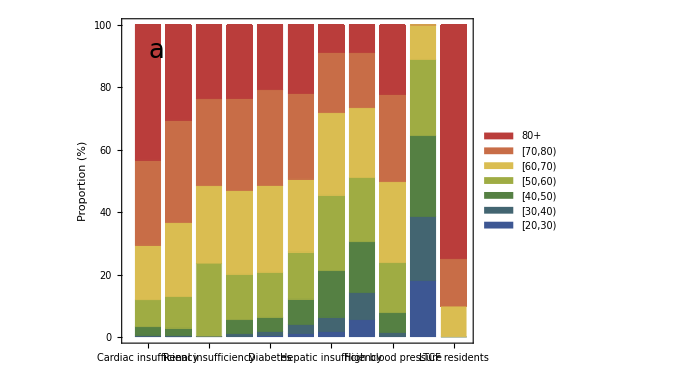
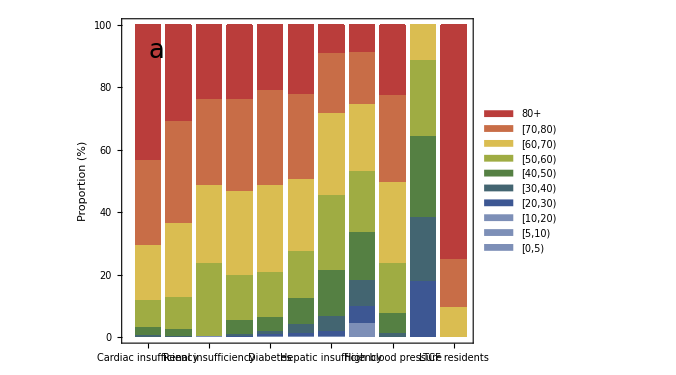

```mathematica
CategoriesAgeDistribution=Import["Data//VaccinationAgeDistribution.xlsx"]⟦1⟧;
ImportCategoriesAgeDistribution[i_]:=Join[{Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦1⟧+Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦2⟧,Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦3⟧},Total/@Partition[Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦4;;17⟧,2],{Total[Reverse[CategoriesAgeDistribution⟦5;;26,i⟧]⟦18;;22⟧]}];

A11=Join[{0,0,0},DemographyData10⟦4;;7⟧,{DemographyData17⟦13⟧,0,0}];
A12a=Join[{0,0,0},DemographyData10⟦4;;7⟧,{DemographyData17⟦13⟧,0,0}];
(*A12b=Join[{0,0,0,0,0,0,0,DemographyData17⟦14⟧},DemographyData10⟦9;;10⟧];*)

A12b={0,0,0,0,0,0,0,27500 DemographyData17⟦14⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧+DemographyData17⟦16⟧),27500 (DemographyData17⟦15⟧+DemographyData17⟦16⟧)/(DemographyData17⟦14⟧+DemographyData17⟦15⟧+DemographyData17⟦16⟧),82500};

A13=ImportCategoriesAgeDistribution[5];
A14=ImportCategoriesAgeDistribution[8];
A15={72 DemographyData17⟦1⟧/Sum[DemographyData17⟦i⟧,{i,1,5}],72 DemographyData17⟦2⟧/Sum[DemographyData17⟦i⟧,{i,1,5}],72 (DemographyData17⟦3⟧+DemographyData17⟦4⟧)/Sum[DemographyData17⟦i⟧,{i,1,5}],72 DemographyData17⟦5⟧/Sum[DemographyData17⟦i⟧,{i,1,5}],0,0,4222 (DemographyData17⟦11⟧+DemographyData17⟦12⟧)/Sum[DemographyData17⟦i⟧,{i,11,13}],4222 DemographyData17⟦13⟧/Sum[DemographyData17⟦i⟧,{i,11,13}]+3361 DemographyData17⟦14⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧),3361 DemographyData17⟦15⟧/(DemographyData17⟦14⟧+DemographyData17⟦15⟧)+4840 DemographyData17⟦16⟧/(DemographyData17⟦16⟧+DemographyData17⟦17⟧),4840 DemographyData17⟦17⟧/(DemographyData17⟦16⟧+DemographyData17⟦17⟧)};
(*Manuel said that the 20-65 are all in the 50-65 age groups*)
A16=ImportCategoriesAgeDistribution[14];
A17=Join[{0,0,0},DemographyData10⟦4;;7⟧,{DemographyData17⟦13⟧,0,0}];

A22=ImportCategoriesAgeDistribution[11];
A23=ImportCategoriesAgeDistribution[23];
A24=ImportCategoriesAgeDistribution[29];
(* A25 Same disease as A15 so I grouped them *)
A26=ImportCategoriesAgeDistribution[20];
A27=ImportCategoriesAgeDistribution[17];

BarChartFormat[x_]:=100 x/Total[x];

AgeDistributionChartLabel={"Cardiac insufficiency","Coronary heart disease","Renal insufficiency", "Chronic respiratory disease","Diabetes","Neoplasm","Hepatic insufficiency","Obesity","High blood pressure","HCW, LTCF staff, Police","LTCF residents"};

BarChartLegends=Style[#,Black]&/@{"[0,5)","[5,10)","[10,20)","[20,30)","[30,40)","[40,50)","[50,60)","[60,70)","[70,80)","80+"};

ChartStyleColors=Join[{Lighter[ColorData["DarkRainbow"][0]],Lighter[ColorData["DarkRainbow"][0]],Lighter[ColorData["DarkRainbow"][0]](*ColorData["DarkRainbow"][0],ColorData["DarkRainbow"][0],ColorData["DarkRainbow"][0]*)},ColorData["DarkRainbow"]/@Rescale[AgeGroups⟦1;;7⟧]];

AspRat=0.75;

PlotBarChart[StartAgeGroup_,colors_]:=Show[BarChart[BarChartFormat/@(#⟦StartAgeGroup;;⟧&/@{A13,A14,A15,A16,A22,A23,A24,A26,A27,A11,A12b}),ChartLayout->"Stacked",ImageSize->500,ChartLabels->{Rotate[Style[#,Black,14],Pi/2]&/@AgeDistributionChartLabel,None},ChartLegends->Placed[BarChartLegends⟦StartAgeGroup;;⟧,(*{After,Top}*){Scaled[ {{1.1, 0.5}, {0.5,0.5 }}]}], PlotTheme->"Web",Joined->False,BarSpacing->0.2,AspectRatio->AspRat,Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],ChartStyle->colors,FrameLabel-> {{"Proportion (%)",None},{None,None}},PlotRange->{All,{0,100}},PlotRangePadding->None,FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}}],Graphics[Text[StyleForm["a",FontSize->26],Scaled[{0.1,0.9}]]]]

{PlotBarChart[4,"DarkRainbow"],fig1A=PlotBarChart[1,ChartStyleColors]}

format={".pdf",".eps"};

(*Table[Export[StringJoin["Figures//Fig1A",format⟦i⟧],fig1A],{i,1,Length[format]}];*)
```

## Vaccination rates as piece-wise functions

```mathematica
Clear[CreatePiecewiseRate,Rates,UnconstrainedRates,OrderIntervals]

CreatePiecewiseRate[Rate_,StartVaccinationDate_,EndVaccinationDate_]:=
Piecewise[{{0,t<0},{0,Subscript[t, start]≤t<StartVaccinationDate},{Rate,StartVaccinationDate≤t≤EndVaccinationDate},{0,t> EndVaccinationDate}}]/.{Subscript[t, vaccination]->tstartvac,Subscript[t, start]-> t0}

UnconstrainedRates=Table[ PiecewiseExpand[Sum[Sum[CreatePiecewiseRate[VacRatesVector⟦Fase⟧⟦Category⟧⟦k⟧,StartVaccinationDates⟦Fase⟧⟦Category⟧,EndVaccinationDates⟦Fase⟧⟦Category⟧],{Category,1,NumberOfCategories⟦Fase⟧}],
{Fase,{Fase1,Fase2,Fase3}}]],{k,AgeGroups}];
Print[Style["Vaccination rates with unordered intervals and without constraints on the number of vaccines",18,Blue,"Text"]]
Rates=UnconstrainedRates

PiecewiseDomains[HoldPattern[Piecewise[cases_,default_]]]:=Module[{dl=Last/@cases},Append[dl,Not[Or@@dl]]]
OrderIntervals=Table[Quiet@Maximize[{t,#},t]&/@PiecewiseDomains[UnconstrainedRates⟦k⟧]//N//Ordering,{k,AgeGroups}];
Table[Rates⟦k⟧⟦1⟧=Table[UnconstrainedRates⟦k⟧⟦1⟧⟦PosInt⟧,{PosInt,OrderIntervals⟦k⟧⟦1;;Length[OrderIntervals⟦k⟧]-1⟧}],{k,AgeGroups}];

Print[Style["Vaccination rates with ordered intervals but without constraints on the number of vaccines",18,Blue,"Text"]];
Rates

Table[Rates⟦k⟧⟦1⟧=Table[{Rates⟦k⟧⟦1⟧⟦PosInt⟧⟦1⟧,Rates⟦k⟧⟦1⟧⟦PosInt⟧⟦2⟧&&Sum[Rates⟦k⟧⟦1⟧⟦PosIntSum⟧⟦1⟧ (Rates⟦k⟧⟦1⟧⟦PosIntSum⟧⟦2⟧⟦5⟧-Rates⟦k⟧⟦1⟧⟦PosIntSum⟧⟦2⟧⟦1⟧),{PosIntSum,1,PosInt-1}]+Rates⟦k⟧⟦1⟧⟦PosInt⟧⟦1⟧ (t-Rates⟦k⟧⟦1⟧⟦PosInt⟧⟦2⟧⟦1⟧)≤(*If[k==3,2/10,1]*)0.9 Subscript[NN, k]/.Demography//Simplify},{PosInt,1,Length[Rates⟦k⟧⟦1⟧]}],{k,AgeGroups}];

Print[Style["Vaccination rates with constraints on the number of vaccines",18,Blue,"Text"]];
Table[Rates⟦k⟧=Subscript[r,k]->Rates⟦k⟧,{k,AgeGroups}]
```

Vaccination rates with unordered intervals and without constraints on the number of vaccines

{Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 431≤t≤522}, {155.109, 369<t≤430}, {570.076, 306≤t<311}, {759.64, 311≤t<342}, {914.749, 342≤t≤369}, {8687.68, 523≤t≤675}, {0, True}}],Piecewise[{{0., 431≤t≤522}, {177.602, 369<t≤430}, {652.745, 306≤t<311}, {869.8, 311≤t<342}, {1047.4, 342≤t≤369}, {9947.52, 523≤t≤675}, {0, True}}],Piecewise[{{0., 431≤t≤522}, {223.73, 369<t≤430}, {822.282, 306≤t<311}, {1095.71, 311≤t<342}, {1319.44, 342≤t≤369}, {12531.2, 523≤t≤675}, {0, True}}],Piecewise[{{773.68, 306≤t<311}, {844.984, 369<t≤430}, {1030.95, 311≤t<342}, {1875.93, 342≤t≤369}, {9518.87, 431≤t≤522}, {11790.5, 523≤t≤675}, {0, True}}],Piecewise[{{0., 523≤t≤675}, {351.186, 306≤t<311}, {613.951, 311≤t<342}, {1429.86, 369<t≤430}, {2043.81, 342≤t≤369}, {12170., 431≤t≤522}, {0, True}}],Piecewise[{{0., 306≤t<311||523≤t≤675}, {228.934, 311≤t<342}, {1811.5, 369<t≤430}, {2040.43, 342≤t≤369}, {8855.03, 431≤t≤522}, {0, True}}],Piecewise[{{0., 306≤t<311||523≤t≤675}, {1124.76, 311≤t<342}, {2056.47, 369<t≤430}, {3181.23, 342≤t≤369}, {6084.54, 431≤t≤522}, {0, True}}]}

Vaccination rates with ordered intervals but without constraints on the number of vaccines

{Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],Piecewise[{{570.076, 306≤t<311}, {759.64, 311≤t<342}, {914.749, 342≤t≤369}, {155.109, 369<t≤430}, {0., 431≤t≤522}, {8687.68, 523≤t≤675}, {0, True}}],Piecewise[{{652.745, 306≤t<311}, {869.8, 311≤t<342}, {1047.4, 342≤t≤369}, {177.602, 369<t≤430}, {0., 431≤t≤522}, {9947.52, 523≤t≤675}, {0, True}}],Piecewise[{{822.282, 306≤t<311}, {1095.71, 311≤t<342}, {1319.44, 342≤t≤369}, {223.73, 369<t≤430}, {0., 431≤t≤522}, {12531.2, 523≤t≤675}, {0, True}}],Piecewise[{{773.68, 306≤t<311}, {1030.95, 311≤t<342}, {1875.93, 342≤t≤369}, {844.984, 369<t≤430}, {9518.87, 431≤t≤522}, {11790.5, 523≤t≤675}, {0, True}}],Piecewise[{{351.186, 306≤t<311}, {613.951, 311≤t<342}, {2043.81, 342≤t≤369}, {1429.86, 369<t≤430}, {12170., 431≤t≤522}, {0., 523≤t≤675}, {0, True}}],Piecewise[{{228.934, 311≤t<342}, {2040.43, 342≤t≤369}, {1811.5, 369<t≤430}, {8855.03, 431≤t≤522}, {0., 306≤t<311||523≤t≤675}, {0, True}}],Piecewise[{{1124.76, 311≤t<342}, {3181.23, 342≤t≤369}, {2056.47, 369<t≤430}, {6084.54, 431≤t≤522}, {0., 306≤t<311||523≤t≤675}, {0, True}}]}

Vaccination rates with constraints on the number of vaccines

{r_1→Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],r_2→Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],r_3→Piecewise[{{0., 306≤t≤430||431≤t≤522||523≤t≤675}, {0, True}}],r_4→Piecewise[{{570.076, 306.≤t<311.}, {759.64, 311.≤t<342.}, {914.749, 342.≤t≤369.}, {155.109, 369.<t≤430.}, {0., 431≤t≤522}, {8687.68, 523.≤t≤629.163}, {0, True}}],r_5→Piecewise[{{652.745, 306.≤t<311.}, {869.8, 311.≤t<342.}, {1047.4, 342.≤t≤369.}, {177.602, 369.<t≤430.}, {0., 431≤t≤522}, {9947.52, 523.≤t≤629.163}, {0, True}}],r_6→Piecewise[{{822.282, 306.≤t<311.}, {1095.71, 311.≤t<342.}, {1319.44, 342.≤t≤369.}, {223.73, 369.<t≤430.}, {0., 431≤t≤522}, {12531.2, 523.≤t≤629.163}, {0, True}}],r_7→Piecewise[{{773.68, 306.≤t<311.}, {1030.95, 311.≤t<342.}, {1875.93, 342.≤t≤369.}, {844.984, 369.<t≤430.}, {9518.87, 431.≤t≤522.}, {11790.5, 523.≤t≤550.961}, {0, True}}],r_8→Piecewise[{{351.186, 306.≤t<311.}, {613.951, 311.≤t<342.}, {2043.81, 342.≤t≤369.}, {1429.86, 369.<t≤430.}, {12170., 431.≤t≤513.233}, {0, True}}],r_9→Piecewise[{{228.934, 311.≤t<342.}, {2040.43, 342.≤t≤369.}, {1811.5, 369.<t≤430.}, {8855.03, 431.≤t≤510.404}, {0, True}}],r_10→Piecewise[{{1124.76, 311.≤t<342.}, {3181.23, 342.≤t≤369.}, {2056.47, 369.<t≤430.}, {6084.54, 431.≤t≤489.441}, {0, True}}]}

## Plotting vaccination rates

Vaccination rate (persons per day) for each age group

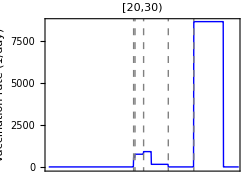
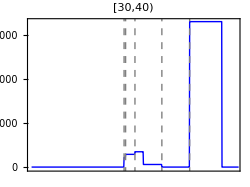
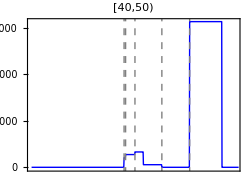
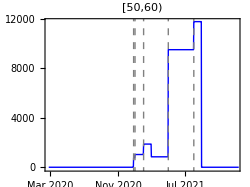
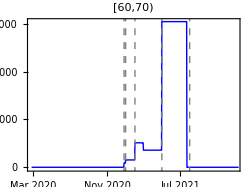
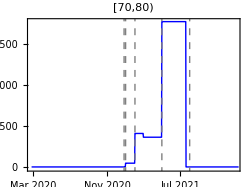
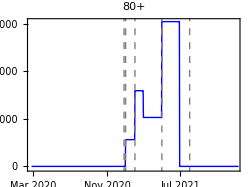
-Graphics- | -Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-

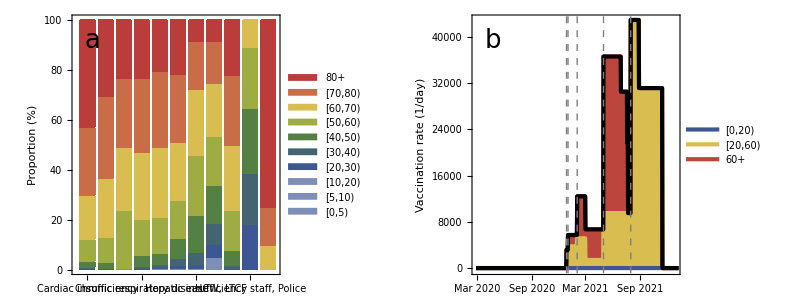

```mathematica
Subscript[t, start]=t0;
Subscript[t, end]=tendvac;

AspRat=0.75; ImSize=350;

FigNames={"A","B","C","D","E","F","G","H","I","J"};
PanelLetter[AgeGroup_]:=Graphics[Text[StyleForm[FigNames⟦AgeGroup⟧,FontSize->26],Scaled[{0.9,0.9}]]];

UniqueStartVaccinationDatesAll=DeleteDuplicates[Join[StartAndEndVaccinationDates⟦1⟧⟦All,1⟧,StartAndEndVaccinationDates⟦2⟧⟦All,1⟧,{StartAndEndVaccinationDates⟦3⟧⟦1⟧}]];

UniqueStartVaccinationDates=UniqueStartVaccinationDatesAll⟦1⟧+UniqueStartVaccinationDatesAll⟦4⟧+UniqueStartVaccinationDatesAll⟦5⟧;

UniqueStartVaccinationDays=DeleteDuplicates[Flatten[StartVaccinationDates]]/.Subscript[t, vaccination]->tstartvac;

VaccinationLines:=Table[DateListPlot[{{UniqueStartVaccinationDates⟦i⟧,0},{UniqueStartVaccinationDates⟦i⟧,10000}},PlotStyle->{Dashed,Gray},DateTicksFormat->{"MonthShort","/","YearShort"}],{i,1,Length[UniqueStartVaccinationDates]}];

Print[Style["Vaccination rate (persons per day) for each age group",24,Blue,"Text"]];

tickValues=DateRange[{2020,3,1},{2022,1,1},{4,"Month"}][[All,{1,2}]];
ticks={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;

SFig4=Table[Show[DateListPlot[Table[Rates⟦k,2⟧,{t,Subscript[t, start],Subscript[t, end]}],"February 25, 2020",PlotRange->{{"February 25, 2020","January 01, 2022"},{-75,All}},ImageSize->250,PlotRangePadding->None,
PlotTheme->"Web",AspectRatio->AspRat,FrameStyle->Directive[Black,14],Frame-> {{True,False},{True,False}},FrameTicks->{{Automatic,None},{If[k≥ 7,ticks,None],None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)FrameLabel-> {{If[k==4||k==7,"Vaccination rate (1/day)",None],None},{None,None}},Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],Filling->None,PlotStyle->{Blue,Thick},PlotLabel->Style[Row[{AgeLabelShort⟦k⟧}],Black,14],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{If[k==4||k== 7,65,42], Automatic}, {Automatic, Automatic}}](*,Graphics[Text[StyleForm[FigNames⟦k⟧,FontSize->26],Scaled[{0.9,0.9}]]]*)],{k,Range[4,10]}];
SFig4all=Grid[{SFig4⟦1;;3⟧,SFig4⟦4;;7⟧}]

(*Table[Export[StringJoin["Figures//SFig3",format⟦i⟧],SFig4all],{i,1,Length[format]}];*)

VaccinationRatesPlot=Table[Table[Rates⟦k,2⟧,{t,Subscript[t, start],Subscript[t, end]}],{k,AgeGroups}];
VaccinationRatesLegends=Style[#,Black]&/@{"[0,20)","[20,60)","60+"};
lineColors=Part[(ColorData["DarkRainbow"]/@Rescale[{1,2,3,4,5,6,7,8,9,10}]),{1,7,9}];

(*lineColors=ColorData["DarkRainbow"]/@Rescale[{1,2,3}];*)
lineWidths={Thickness[0.01],Thickness[0.01],Thickness[0.01]};

ListLinePlot[{Total[VaccinationRatesPlot⟦1;;3⟧],Total[VaccinationRatesPlot⟦1;;7⟧],Total[VaccinationRatesPlot⟦1;;10⟧]},PlotRange->All,ImageSize->ImSize,PlotLegends->VaccinationRatesLegends,Filling->{3-> {2},2-> {1},1-> Axis},PlotTheme->"Web",AspectRatio->AspRat,FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},FrameLabel-> {{"Vaccination rate\n(1/day)",None},{"Days",None}},PlotStyle->Transpose[{lineColors,lineWidths}],AxesOrigin->{0,0},PlotRangePadding->None];

tickValues=DateRange[{2020,3,1},{2022,1,1},{2,"Month"}][[All,{1,2}]];
ticks={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;

fig1B=Show[DateListPlot[{Total[VaccinationRatesPlot⟦1;;3⟧],Total[VaccinationRatesPlot⟦1;;7⟧],Total[VaccinationRatesPlot⟦1;;10⟧]},"February 25, 2020",PlotRange->{{"February 25, 2020","January 01, 2022"},{-250,All}},ImageSize->500,PlotLegends->Placed[VaccinationRatesLegends,Scaled[{{0.1, 0.7}, {0,1 }}]],Filling->{3-> {{2},lineColors⟦3⟧},2-> {{1},lineColors⟦2⟧},1-> Axis},PlotTheme->"Web",AspectRatio->AspRat,FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},FrameTicks->{{Automatic,None},{ticks,None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)FrameLabel-> {{"Vaccination rate (1/day)",None},{None,None}},Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],PlotStyle->lineColors(*Transpose[{lineColors,lineWidths}]*),AxesOrigin->{"February 25, 2020",0},PlotRangePadding->None,FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{80, Automatic}, {140, Automatic}}],DateListPlot[Total[VaccinationRatesPlot⟦1;;10⟧],"February 25, 2020",PlotStyle->{Black},PlotTheme->"Web"],Graphics[Text[StyleForm["b",FontSize->26],Scaled[{0.1,0.9}]]]];

(*Table[Export[StringJoin["Figures//Fig1B",format⟦i⟧],fig1B],{i,1,Length[format]}];*)

DateListPlot[Table[Total[VaccinationRatesPlot⟦1;;k⟧],{k,AgeGroups}],"February 25, 2020",DateTicksFormat->{"MonthShort","/","YearShort"},PlotRange->All,ImageSize->500,PlotLegends->(Style[#,Black,17]&/@AgeLabel)(*,Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]]*),Filling->Table[If[k≤ 9,(k+1)-> {k}],{k,AgeGroups}],PlotTheme->"Web",AspectRatio->AspRat,FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},FrameLabel-> {{"Vaccination rate (1/day)",None},{None,None}},PlotStyle->"CMYKColors",AxesOrigin->{"February 25, 2020",0},PlotRangePadding->None];

(*fig1=Grid[{{fig1A},{fig1B}}]*)
fig1=Grid[{{fig1A,fig1B}}]

(*Table[Export[StringJoin["Figures//Fig1",format⟦i⟧],fig1],{i,1,Length[format]}];*)
```

## Importing hospitalization data and parameter estimates

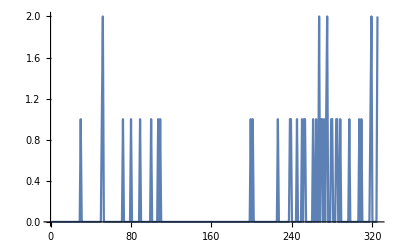
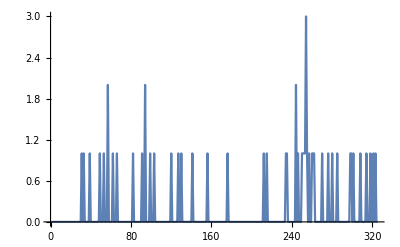
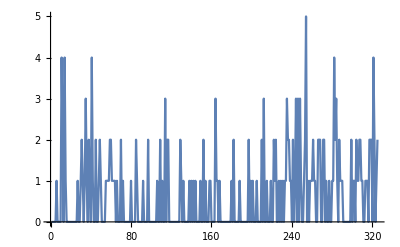
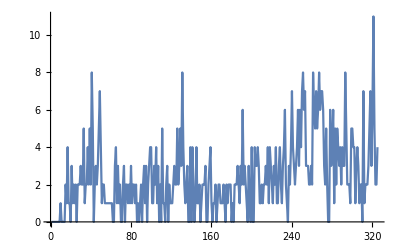
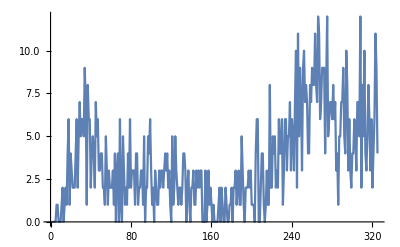
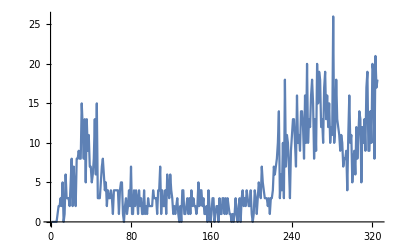
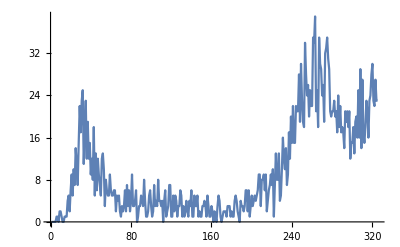
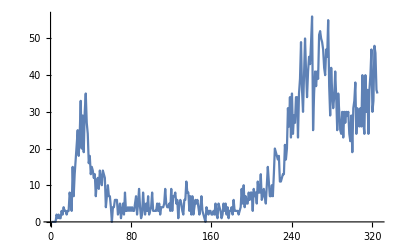

28482

```mathematica
HospitalisationsData=Import["Data//hospitalisations_selected PT 15 Jan 2021 3.csv"];
HospitalisationsData=Drop[HospitalisationsData,1];
Total[Total[HospitalisationsData]];
Dimensions[HospitalisationsData];
TableForm[HospitalisationsData];

Table[ListLinePlot[{HospitalisationsData⟦All,k⟧},PlotRange-> All],{k,AgeGroups}]

Total[Total[HospitalisationsData]]
```

```mathematica
(*Transpose[Insert[Transpose[a],column,2]]*)

HospitalisationsData=Import["Data//hospitalisations_selected PT 15 Jan 2021 3.csv"](*⟦1;;255,All⟧*);
HospitalisationsData=Drop[HospitalisationsData,1];
Dimensions[HospitalisationsData];
TableForm[HospitalisationsData];

ContactRates:=
Flatten[Table[{Subscript[c,{k,l}]->ContactDataPTBefore10Vespignani⟦k,l⟧,Subscript[d,{k,l}]->ContactDataPTAfter10Vespignani⟦k,l⟧(*,Subscript[s,{k,l}]->SchoolContactDataPTBefore10Vespignani⟦k,l⟧*)},{k,1,NumAgeGroups},{l,1,NumAgeGroups}]];

Print[Style["Imported estimated parameters",18,Blue,"Text"]]
(*EstimatesData=Import["Data//fit_19012021_PT.csv"];*)
(*EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1.csv"];*)
(*EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1_187days.csv"];*)
(*EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1_school_opening_254days.csv"];*)
(*EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1_school_opening_254days_2.csv"];*)
(*EstimatesData=Import["Data//fit_19012021_PT_10_hosp_classes_prior_trans_points_updated_data_new_prior_k1_school_opening_254days_corrected_prior_omegaV_beta_std_02_constant_alpha_gamma_sero_classes.csv"];*)
(*EstimatesData=Import["Data//tempU4.csv"];*)

EstimatesData=Import["Data//fullU4_daily_Joao.csv"];

(*Pos=Dimensions[EstimatesData]⟦2⟧;

EstimatesData=Transpose[Insert[Transpose[EstimatesData],Table[alpha,{i,1,Dimensions[EstimatesData]⟦1⟧}],Pos+1]];
EstimatesData=Transpose[Insert[Transpose[EstimatesData],Table[gamma,{i,1,Dimensions[EstimatesData]⟦1⟧}],Pos+2]];*)

Print[Style["Dimensions of the imported data",18,Blue,"Text"]]
Dimensions[EstimatesData]

Print[Style["Header of the imported data",18,Blue,"Text"]]
HeaderParameters=EstimatesData⟦1⟧

EstimatesData=Drop[EstimatesData,1];

(*DischargeRate:=δ->1/5;*)

(*https://bmcmedicine.biomedcentral.com/articles/10.1186/s12916-020-01726-3*)

ProbTransm[sample_]:=ϵ->EstimatesData⟦sample,1⟧(1+0.5 1/(1+Exp[-EstimatesData⟦sample,21⟧(t-tenddata)]));
zeta[sample_]:=ζ-> EstimatesData⟦sample,2⟧;

(* hosp_classes=c(1,2,3,4,5,6,7,8,9,10) *)
(* susc_classes=c(1,1,1,2,2,2,2,3,3,3) *)

nu[sample_]:=Table[Subscript[ν,k]->EstimatesData⟦sample,2+k⟧,{k,1,10}];

Inoculum[sample_]:=Flatten[Table[{Subscript[S0,k]-> 1-EstimatesData⟦sample,13⟧,Subscript[EE0,k]-> 0.5 EstimatesData⟦sample,13⟧,Subscript[II0,k]-> 0.5 EstimatesData⟦sample,13⟧,Subscript[R0,k]-> 0,Subscript[H0,k]-> 0},{k,AgeGroups}]];

Susceptibility[sample_]:=Flatten[Join[Table[Subscript[β,k]->EstimatesData⟦sample,14⟧ ,{k,1,3}],Table[Subscript[β,k]->EstimatesData⟦sample,15⟧ ,{k,4,7}],Table[Subscript[β,k]->EstimatesData⟦sample,16⟧ ,{k,8,10}]]];

rOverDisp[sample_]:=EstimatesData⟦sample,17⟧;

LogFunction[sample_]:={Subscript[x, 0]-> EstimatesData⟦sample,20⟧,Subscript[K, 0]-> EstimatesData⟦sample,21⟧,Subscript[x, 1]-> EstimatesData⟦sample,22⟧,Subscript[K, 1]-> EstimatesData⟦sample,23⟧,Subscript[x, 2]-> EstimatesData⟦sample,24⟧,Subscript[K, 2]-> EstimatesData⟦sample,25⟧,Subscript[x, 3]-> EstimatesData⟦sample,26⟧,Subscript[K, 3]-> EstimatesData⟦sample,27⟧,Subscript[x, 4]-> EstimatesData⟦sample,28⟧,Subscript[K, 4]-> EstimatesData⟦sample,29⟧};

RelaxationFraction[sample_]:={Subscript[u, 1]-> EstimatesData⟦sample,30⟧,Subscript[u, 2]-> EstimatesData⟦sample,31⟧,Subscript[u, 3]-> EstimatesData⟦sample,32⟧,Subscript[u, 4]-> EstimatesData⟦sample,33⟧} ;

LatRate[sample_]:=α->EstimatesData⟦sample,18⟧;
RecRate[sample_]:=γ->EstimatesData⟦sample,19⟧;

x6=(tenddata+12);
x7=(tenddata+58+17);

Parameters[sample_]:=
Flatten[{(*DischargeRate,*)ContactRates,Demography,ProbTransm[sample],zeta[sample],nu[sample],Inoculum[sample],Susceptibility[sample],LogFunction[sample],RelaxationFraction[sample],LatRate[sample],RecRate[sample],TransBritishVariant->1.5,Subscript[x, 5]-> tenddata,Subscript[K, 5]->EstimatesData⟦sample,21⟧(*Median[EstimatesData⟦All,21⟧]*),Subscript[x, 6]->x6,Subscript[K, 6]->EstimatesData⟦sample,21⟧,Subscript[x, 7]->x7,Subscript[K, 7]->  EstimatesData⟦sample,23⟧}];

(*VaccineEfficacy[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]:={Subscript[ω, 1]->x1,Subscript[ω, 2]->x2,Subscript[ω, 3]->x3,Subscript[ω, 4]->x4,Subscript[ω, 5]->x5,Subscript[ω, 6]->x6,Subscript[ω, 7]->x7,Subscript[ω, 8]->x8,Subscript[ω, 9]->x9,Subscript[ω, 10]->x10};

VacEffHigh=VaccineEfficacy[0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95,0.95];
VacEffLow=VaccineEfficacy[0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5];*)

Ef1:=Subscript[ω, 1]-> 0.94
Ef2:=(Solve[0.94==Subscript[ω, 1]+(1–Subscript[ω, 1]) Subscript[ω, 2],Subscript[ω, 2]]/.Ef1)⟦1,1⟧
Ef3:=(Solve[0.98==Subscript[ω, 1]+(1-Subscript[ω, 1]) Subscript[ω, 2] + (1-Subscript[ω, 1]) (1-Subscript[ω, 2]) Subscript[ω, 3],Subscript[ω, 3]]/.{Ef1,Ef2})⟦1,1⟧

DayPlus[{2020,02,25},tenddata]
DayPlus[{2020,02,25},x6]
DayPlus[{2020,02,25},x7]
```

Imported estimated parameters

Dimensions of the imported data

{2001,33}

Header of the imported data

{epsilon,zeta,nu_short[1],nu_short[2],nu_short[3],nu_short[4],nu_short[5],nu_short[6],nu_short[7],nu_short[8],nu_short[9],nu_short[10],inoculum,beta_short[1],beta_short[2],beta_short[3],r,alpha,gamma,x0,k0,x1,k1,x2,k2,x3,k3,x4,k4,u1,u2,u3,u4}

Sat 16 Jan 2021

Thu 28 Jan 2021

Thu 1 Apr 2021

## Parameters vector

```mathematica
ParametersMAP=Parameters[200];

NumSamples=Dimensions[EstimatesData]⟦1⟧;

ParametersMAPNoVaccination=Join[ParametersMAP,Table[Subscript[r,k]-> 0,{k,AgeGroups}],{Subscript[ω, 1]->0,Subscript[ω, 2]->0,Subscript[ω, 3]->0}];
ParametersMAPVaccination=Join[ParametersMAP,Rates,{Ef1,Ef2,Ef3}];

ParametersNoVaccination[sample_]:=Join[Parameters[sample],Table[Subscript[r,k]-> 0,{k,AgeGroups}],{Subscript[ω, 1]->0,Subscript[ω, 2]->0,Subscript[ω, 3]->0}];
ParametersVaccination[sample_]:=Join[Parameters[sample],Rates,{Ef1,Ef2,Ef3}];

ParametersSteadyState[sample_]:=Join[Parameters[sample],Table[Subscript[r,k]-> 0,{k,AgeGroups}],{Ef1,Ef2,Ef3}];
```

## Plotting parameter estimates

{{Probability of transmission per contact, ϵ,5.33392,4.41206,6.46578},{Reduction in probability of
transmission per contact, (1-ζ),0.760647,0.657127,0.90004},{Initial number of infected persons, θ,1233.63,793.951,1883.12},{Susceptibility of [0,20) y.o. relative to 60+ y.o., β_([0, 20)),0.465196,0.282891,0.681486},{Susceptibility of [20,60) y.o. relative to 60+ y.o., β_([20, 60)),0.970469,0.860667,0.998717},{Overdispersion parameter, r,54.3192,37.8274,82.8148},{t_0 (days),28.3654,27.0824,29.3314},{K_0 (1/day),0.922711,0.337737,3.35654},{t_1 (days),63.511,61.3808,66.3885},{K_1 (1/day),1.37613,0.486118,3.71743},{t_2 (days),179.351,176.611,182.028},{K_2 (1/day),0.980365,0.260503,4.4875},{t_3 (days),260.868,257.856,263.952},{K_3 (1/day),0.606277,0.253897,3.5898},{t_4 (days),297.405,293.785,301.131},{K_4 (1/day),0.950969,0.284184,4.45353},{u_1,0.209178,0.182946,0.232351},{u_2,0.41312,0.371173,0.454224},{u_3,0.232933,0.192761,0.280397},{u_4,0.4672,0.389248,0.55519}}

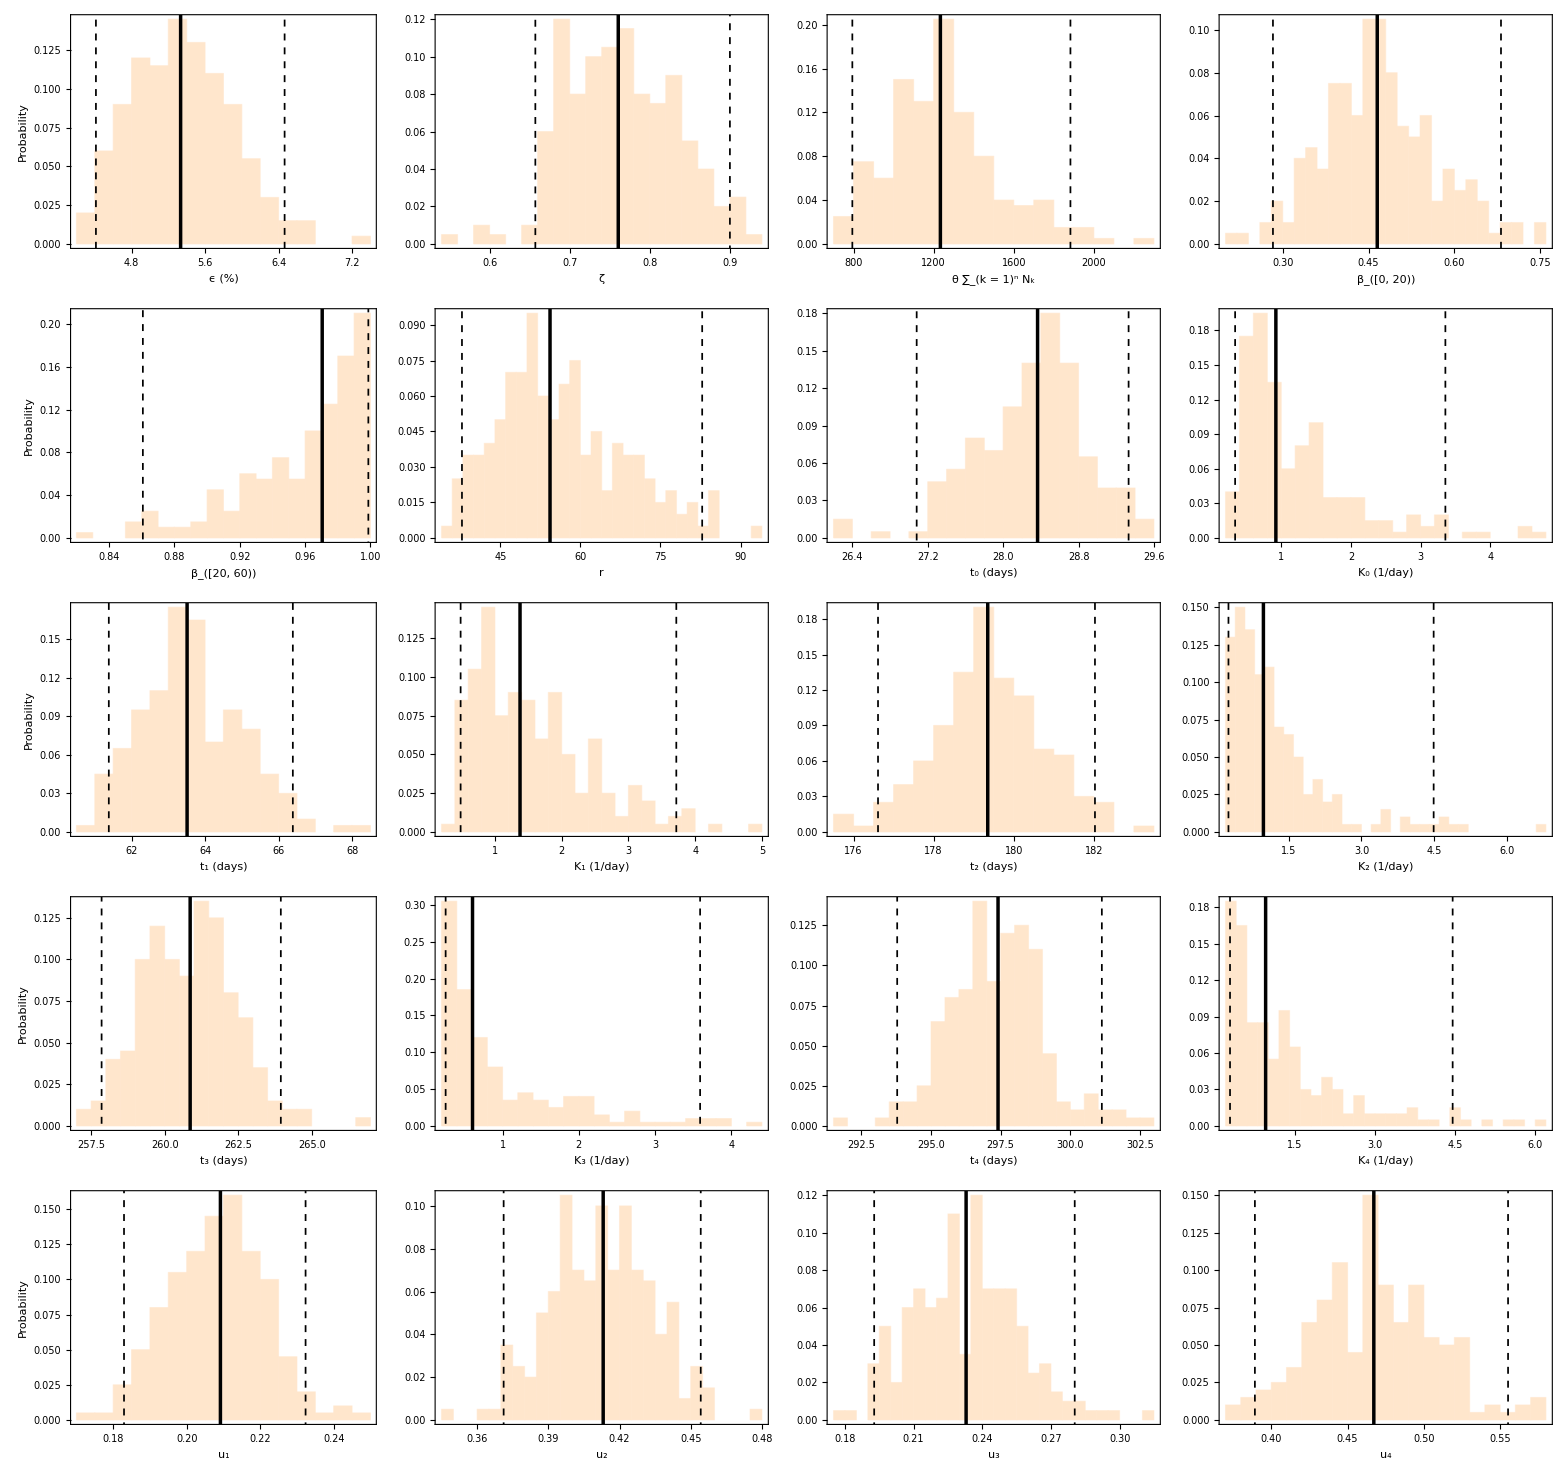

```mathematica
AspRat=0.75; ImSize=400;

HistPlot[vals_,xlab_,panel_,panelindex_]:=Show[Histogram[vals,20,"Probability",AspectRatio->0.75,ImageSize->250,AxesOrigin->{0,0},PlotRange->{Automatic,{0,All}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,14],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},PlotTheme->"Web",FrameLabel-> {{If[panelindex==1||panelindex==5||panelindex==9||panelindex==13||panelindex==17,"Probability",None],None},{xlab,None}},ChartStyle->LightOrange,FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{If[panelindex==1||panelindex==5||panelindex==9||panelindex==13||panelindex==17,52.5,52.5], Automatic}, {Automatic, Automatic}}],Graphics[{Thickness[0.01],Black,InfiniteLine[{{Median[vals],0},{Median[vals],1}}]}],Graphics[{Thickness[0.005],Black,Dashed,InfiniteLine[{{Quantile[vals,0.025],0},{Quantile[vals,0.025],1}}]}],Graphics[{Thickness[0.005],Black,Dashed,InfiniteLine[{{Quantile[vals,0.975],0},{Quantile[vals,0.975],1}}]}](*,Graphics[Text[StyleForm[panel,FontSize->26],Scaled[{0.9,0.9}]]]*)]

(*ImagePadding->{{If[panelindex==1||panelindex==5||panelindex==9||panelindex==13||panelindex==17,60,60], Automatic}, {Automatic, 0}}*)

(*InfiniteLine[{StartVaccinationDates⟦i⟧,0},{0,1}]*)

vals={EstimatesData⟦All,1⟧ 100,EstimatesData⟦All,2⟧,EstimatesData⟦All,13⟧ Total[DemographyData10],EstimatesData⟦All,14⟧,EstimatesData⟦All,15⟧,EstimatesData⟦All,17⟧,EstimatesData⟦All,20⟧,EstimatesData⟦All,21⟧,EstimatesData⟦All,22⟧,EstimatesData⟦All,23⟧,EstimatesData⟦All,24⟧,EstimatesData⟦All,25⟧,EstimatesData⟦All,26⟧,EstimatesData⟦All,27⟧,EstimatesData⟦All,28⟧,EstimatesData⟦All,29⟧,EstimatesData⟦All,30⟧,EstimatesData⟦All,31⟧,EstimatesData⟦All,32⟧,EstimatesData⟦All,33⟧(*,1/EstimatesData⟦All,18⟧,1/EstimatesData⟦All,19⟧*)};

xlabshort={"ϵ (%)","ζ","θ ∑_(k = 1)^n N_k","β_([0, 20))",
"β_([20, 60))","r","t_0 (days)","K_0 (1/day)","t_1 (days)","K_1 (1/day)","t_2 (days)","K_2 (1/day)","t_3 (days)","K_3 (1/day)","t_4 (days)","K_4 (1/day)","u_1","u_2","u_3","u_4"(*,"Latent period (days), 1/α","Infectious period (days), 1/γ"*)};

xlab={"Probability of transmission per contact, ϵ","Reduction in probability of\ntransmission per contact, (1-ζ)","Initial number of infected persons, θ","Susceptibility of [0,20) y.o. relative to 60+ y.o., β_([0, 20))",
"Susceptibility of [20,60) y.o. relative to 60+ y.o., β_([20, 60))","Overdispersion parameter, r","t_0 (days)","K_0 (1/day)","t_1 (days)","K_1 (1/day)","t_2 (days)","K_2 (1/day)","t_3 (days)","K_3 (1/day)","t_4 (days)","K_4 (1/day)","u_1","u_2","u_3","u_4"(*,"Latent period (days), 1/α","Infectious period (days), 1/γ"*)};

(*"Midpoint value of the logistic function (days), t_1","Logistic growth rate (1/day), K_1","Proportion of contacts during relaxation, u"*)

FigNames={"A","B","C","D","E","F","G","H","I","J","K","L","M","N","O","P","Q","R", "S","T","U","V"};

Table[{xlab⟦i⟧,Median[vals⟦i⟧],Quantile[vals⟦i⟧,0.025],Quantile[vals⟦i⟧,0.975]},{i,1,Length[vals]}]

fig=Grid[Partition[Table[(*fig3[i]=*)HistPlot[vals⟦i⟧,xlabshort⟦i⟧,FigNames⟦i⟧,i],{i,1,Length[vals]}],4]]

(*Table[Export[StringJoin["Figures//SFig4",format⟦i⟧],fig],{i,1,Length[format]}]*)
```

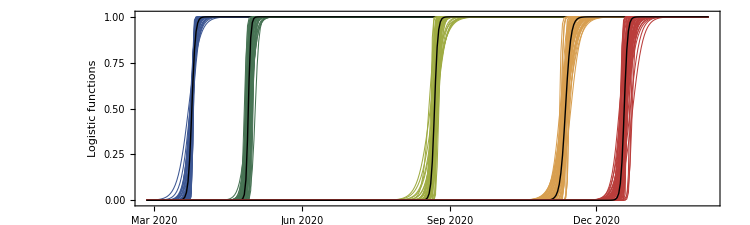

```mathematica
(* PlotLogisticTransition[midpointindex_,slopeindex_,tend_,ylabel_]:=Show[Plot[Table[(1/(1+Exp[-KK (t-xx)]))/.{xx-> EstimatesData⟦sample,midpointindex⟧,KK->EstimatesData⟦sample,slopeindex⟧},{sample,1,NumSamples,25}],{t,0,tend},AxesOrigin->{0,0},PlotTheme->"Web",PlotRange->{{0,tend},{-0.01,1.01}},PlotStyle->{Gray,Thickness[0.001]},AspectRatio->0.2,ImageSize->1000,Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{ylabel,None},{"t (days)",None}}],Plot[(1/(1+Exp[-KK (t-xx)]))/.{xx-> Median[EstimatesData⟦All,midpointindex⟧],KK->Median[EstimatesData⟦All,slopeindex⟧]},{t,0,tend},PlotStyle->{Red,Thick},PlotTheme->"Web",PlotRange->All],Graphics[{Thickness[0.001],Black,Dashed,Line[{{Median[EstimatesData⟦All,midpointindex⟧],0},{Median[EstimatesData⟦All,midpointindex⟧],1}}]}],Graphics[{Thickness[0.001],Black,Dashed,Line[{{0,0.5},{tend,0.5}}]}]]
(*Graphics[Text[StyleForm["t_1",FontSize->17],{31,0.05}]],Graphics[Text[StyleForm["K_1",FontSize->17],{34,0.7}]]*)

Show[PlotLogisticTransition[20,21,350,"Contribution"],PlotLogisticTransition[22,23,350,"Contribution"],PlotLogisticTransition[24,25,350,"Contribution"],PlotLogisticTransition[26,27,350,"Contribution"],PlotLogisticTransition[28,29,350,"Contribution"]]; *)


tickValues=DateRange[{2020,3,1},{2022,1,1},{1,"Month"}][[All,{1,2}]];
ticks={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;
lineColors=ColorData["DarkRainbow"]/@Rescale[{1,2,3,4,5}];

(* plot about 50 samples *)

PlotLogisticTransition[midpointindex_,slopeindex_,color_]:=Show[Join[Table[DateListPlot[Table[(1/(1+Exp[-KK (t-xx)]))/.{xx-> EstimatesData⟦sample,midpointindex⟧,KK->EstimatesData⟦sample,slopeindex⟧},{t,Subscript[t, start],350}],"February 25, 2020",AxesOrigin->{"February 25, 2020",0},PlotTheme->"Web",PlotRange->{{"February 25, 2020",Automatic},{-0.01,1.01}},PlotStyle->{color,Thickness[0.001]},AspectRatio->0.3,ImageSize->750,Frame-> {{True,False},{True,False}},FrameLabel-> {{"Logistic functions",None},{None,None}},FrameTicks->{{Automatic,None},{ticks,None}},FrameStyle->Directive[Black,17],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}}],{sample,1,NumSamples,4} ],
{DateListPlot[Table[(1/(1+Exp[-KK (t-xx)]))/.{xx-> Median[EstimatesData⟦All,midpointindex⟧],KK->Median[EstimatesData⟦All,slopeindex⟧]},{t,Subscript[t, start],350}],"February 25, 2020",PlotStyle->{Black,Thick},PlotTheme->"Web",PlotRange->All](*,
Graphics[{Thickness[0.001],Black,Dashed,Line[{{Median[EstimatesData⟦All,midpointindex⟧],0},{Median[EstimatesData⟦All,midpointindex⟧],1}}]}],Graphics[{Thickness[0.001],Black,Dashed,Line[{{0,0.5},{tend,0.5}}]}]*)}]]
(*Graphics[Text[StyleForm["t_1",FontSize->17],{31,0.05}]],Graphics[Text[StyleForm["K_1",FontSize->17],{34,0.7}]]*)

fig6=Show[PlotLogisticTransition[20,21,lineColors⟦1⟧],PlotLogisticTransition[22,23,lineColors⟦2⟧],PlotLogisticTransition[24,25,lineColors⟦3⟧],PlotLogisticTransition[26,27,lineColors⟦4⟧],PlotLogisticTransition[28,29,lineColors⟦5⟧]]

(*Table[Export[StringJoin["Figures//SFig6",format⟦i⟧],fig6],{i,1,Length[format]}]*)
```

## Plotting probabilities of hospitalization

{{[0,5),0.0349322,0.0192216,0.0652402},{[5,10),0.0296506,0.016025,0.0583687},{[10,20),0.0480727,0.0266327,0.0848257},{[20,30),0.0826262,0.0598235,0.116561},{[30,40),0.11409,0.0819689,0.167997},{[40,50),0.153497,0.110427,0.215463},{[50,60),0.28491,0.200586,0.407364},{[60,70),0.592528,0.425892,0.802193},{[70,80),1.28861,0.911026,1.81341},{80+,4.047,2.75937,5.62973}}

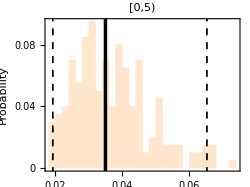
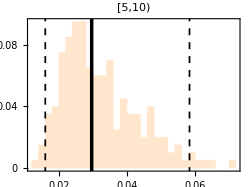
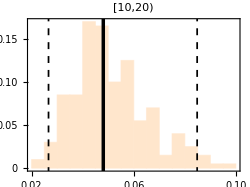
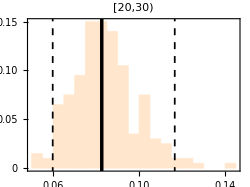
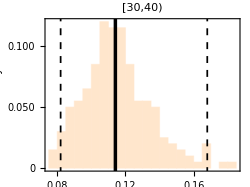
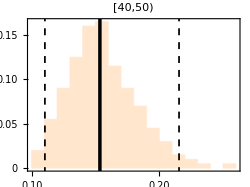
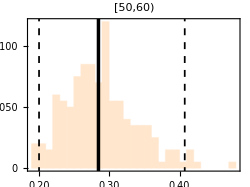
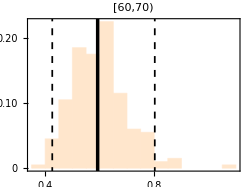
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |  |

```mathematica
HistPlotLabel[vals_,xlab_,label_]:=Show[Histogram[vals,20,"Probability",AspectRatio->0.75,ImageSize->400,AxesOrigin->{0,0},PlotRange->{Automatic,{0,All}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,17],FrameLabel-> {{"Probability",None},{xlab,None}},ChartStyle->LightGray,PlotLabel->Style[Row[{label}],Black,14],PlotTheme->"Web",FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}}],Graphics[{Thickness[0.01],Red,InfiniteLine[{{Median[vals],0},{Median[vals],1}}]}],Graphics[{Thickness[0.005],Red,Dashed,InfiniteLine[{{Quantile[vals,0.025],0},{Quantile[vals,0.025],1}}]}],Graphics[{Thickness[0.005],Red,Dashed,InfiniteLine[{{Quantile[vals,0.975],0},{Quantile[vals,0.975],1}}]}]]

HistPlotLabelPanel[vals_,xlab_,label_,panel_,panelindex_]:=Show[Histogram[vals,20,"Probability",AspectRatio->0.75,ImageSize->250,AxesOrigin->{0,0},PlotRange->{Automatic,{0,All}},Frame-> {{True,False},{True,False}},FrameStyle->Directive[Black,14],FrameLabel-> {{If[panelindex==1||panelindex==5||panelindex==9,"Probability",None],None},{If[panelindex≥ 9,xlab,None],None}},ChartStyle->LightOrange,PlotLabel->Style[Row[{label}],Black,14],PlotTheme->"Web",FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{If[panelindex==1||panelindex==5||panelindex==9||panelindex==13||panelindex==17,60,60], Automatic}, {Automatic, Automatic}}],Graphics[{Thickness[0.01],Black,InfiniteLine[{{Median[vals],0},{Median[vals],1}}]}],Graphics[{Thickness[0.005],Black,Dashed,InfiniteLine[{{Quantile[vals,0.025],0},{Quantile[vals,0.025],1}}]}],Graphics[{Thickness[0.005],Black,Dashed,InfiniteLine[{{Quantile[vals,0.975],0},{Quantile[vals,0.975],1}}]}](*,Graphics[Text[StyleForm[panel,FontSize->26],Scaled[{0.9,0.9}]]]*)]

vals=Table[100 EstimatesData⟦All,2+i⟧,{i,1,10}];
xlab="Hosp. rate (1/100 days)";

Table[{AgeLabelShort⟦i⟧,Median[vals⟦i⟧],Quantile[vals⟦i⟧,0.025],Quantile[vals⟦i⟧,0.975]},{i,1,Length[vals]}]

FigNames={"A","B","C","D","E","F","G","H","I","J"};

fig7=Grid[Partition[Table[HistPlotLabelPanel[vals⟦i⟧,xlab,AgeLabelShort⟦i⟧,FigNames⟦i⟧,i],{i,1,Length[vals]}],4,4,1,{}]]

(*Table[Export[StringJoin["Figures//SFig7",format⟦i⟧],fig7],{i,1,Length[format]}]*)
```

## Contact matrix Analytical form

```mathematica
ContactMatrix[t_]:=
Subscript[c,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[x, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[x, 0])]) ζ Subscript[d,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[x, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[x, 1])]) (Subscript[u, 1] Subscript[c,{k,l}]+(1-Subscript[u, 1])ζ Subscript[d,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[x, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[x, 2])]) (Subscript[u, 2] Subscript[c,{k,l}]+(1-Subscript[u, 2])ζ Subscript[d,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[x, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[x, 3])]) (Subscript[u, 3] Subscript[c,{k,l}]+(1-Subscript[u, 3])ζ Subscript[d,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[x, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[x, 4])]) (Subscript[u, 4] Subscript[c,{k,l}]+(1-Subscript[u, 4])ζ Subscript[d,{k,l}])(1-1/(1+Exp[-Subscript[K, 6](t-Subscript[x, 6])]))+
1/(1+Exp[-Subscript[K, 6](t-Subscript[x, 6])]) ζ Subscript[d,{k,l}] (1-1/(1+Exp[-Subscript[K, 7](t-Subscript[x, 7])]))+
1/(1+Exp[-Subscript[K, 7](t-Subscript[x, 7])])(Subscript[u, 2] Subscript[c,{k,l}]+(1-Subscript[u, 2])ζ Subscript[d,{k,l}]);


ContactMatrixV[t_]:=
Subscript[c,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[x, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[x, 0])]) ζ Subscript[d,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[x, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[x, 1])]) (Subscript[u, 1] Subscript[c,{k,l}]+(1-Subscript[u, 1])ζ Subscript[d,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[x, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[x, 2])]) (Subscript[u, 2] Subscript[c,{k,l}]+(1-Subscript[u, 2])ζ Subscript[d,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[x, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[x, 3])]) (Subscript[u, 3] Subscript[c,{k,l}]+(1-Subscript[u, 3])ζ Subscript[d,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[x, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[x, 4])]) (Subscript[u, 4] Subscript[c,{k,l}]+(1-Subscript[u, 4])ζ Subscript[d,{k,l}])(1-1/(1+Exp[-Subscript[K, 6](t-Subscript[x, 6])]))+
1/(1+Exp[-Subscript[K, 6](t-Subscript[x, 6])]) ζ Subscript[d,{k,l}] (1-1/(1+Exp[-Subscript[K, 7](t-Subscript[x, 7])]))+
1/(1+Exp[-Subscript[K, 7](t-Subscript[x, 7])])(Subscript[u, 2] Subscript[c,{k,l}]+(1-Subscript[u, 2])ζ Subscript[d,{k,l}]);
```

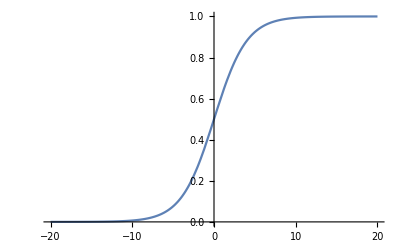

```mathematica
Plot[1/(1+Exp[-0.5 t]),{t,-20,20}]
```

## Model equations

```mathematica
TotNumVariables=11;
VarNumbers= Table[j, {j, 1, TotNumVariables}]
EqNumbers=Table[k,{k,1,NumAgeGroups TotNumVariables}]

Table[{eq[Intervention_][1,k]:=Subscript[S,k]'[t]== - Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t]-Subscript[r,k] Subscript[S,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t]),eq[Intervention_][2,k]:=Subscript[EE,k]'[t]== Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t]-α Subscript[EE,k][t]-Subscript[r,k] Subscript[EE,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t]),
eq[Intervention_][3,k]:=Subscript[II,k]'[t]== α Subscript[EE,k][t]-(γ +Subscript[ν,k]) Subscript[II,k][t],
eq[Intervention_][4,k]:=Subscript[R,k]'[t]==γ Subscript[II,k][t]-Subscript[r,k] Subscript[R,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t])(*+δ Subscript[H,k][t]*),
eq[Intervention_][5,k]:=Subscript[H,k]'[t]==Subscript[ν,k] Subscript[II,k][t]-Subscript[r,k] Subscript[H,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t])(*-δ Subscript[H,k][t]*),
eq[Intervention_][6,k]:=Subscript[SV,k]'[t]==-Subscript[λV,k][Intervention][t]Subscript[β,k](1-Subscript[ω,1])Subscript[SV,k][t]+Subscript[r,k] Subscript[S,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t]),
eq[Intervention_][7,k]:=Subscript[EEV,k]'[t]== Subscript[λV,k][Intervention][t]Subscript[β,k] (1-Subscript[ω,1]) Subscript[SV,k][t]-α Subscript[EEV,k][t]+Subscript[r,k] Subscript[EE,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t]),
eq[Intervention_][8,k]:=Subscript[IIV,k]'[t]== α Subscript[EEV,k][t]-(γ+Subscript[ν,k] (1-Subscript[ω,3])) Subscript[IIV,k][t],
eq[Intervention_][9,k]:=Subscript[RV,k]'[t]== γ Subscript[IIV,k][t]+Subscript[r,k] Subscript[R,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t])(*+δ Subscript[HV,k][t]*),
eq[Intervention_][10,k]:=Subscript[P,k]'[t]== 0,
eq[Intervention_][11,k]:=Subscript[HV,k]'[t]==Subscript[ν,k] (1-Subscript[ω,3]) Subscript[IIV,k][t]+Subscript[r,k] Subscript[H,k][t]/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t])(*-δ Subscript[HV,k][t]*)
(*eq[Intervention_][10,k]:=Subscript[VV,k]'[t]==Subscript[r,k]*)
},{k,AgeGroups}];

(*Table[Subscript[NN,k][t]=(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[II,k][t]+Subscript[R,k][t]+Subscript[H,k][t]+Subscript[SV,k][t]+Subscript[EEV,k][t]+Subscript[IIV,k][t]+Subscript[RV,k][t]+Subscript[P,k][t]+Subscript[HV,k][t]),{k,AgeGroups}];*)

NNtot=Sum[Subscript[NN,k],{k,AgeGroups}];

Table[Subscript[V,k][t]=Subscript[SV,k][t]+Subscript[EEV,k][t]+Subscript[IIV,k][t]+Subscript[RV,k][t]+Subscript[P,k][t]+Subscript[HV,k][t],{k,AgeGroups}];

(* Table[Subscript[λ,k][Intervention_/;Intervention=="Estimation"][t]= ϵ Sum[((1-1/(1+Exp[-K0 (t-x0)])) Subscript[c,{k,l}]+1/(1+Exp[-KK (t-x0)]) ζ Subscript[d,{k,l}]) Subscript[II,l][t]/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}]; *)

Table[Subscript[λ,k][Intervention_/;Intervention=="Estimation"][t]= ϵ Sum[ContactMatrix[t] (Subscript[II,l][t]+(1-Subscript[ω,2]) Subscript[IIV,l][t])/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}]; 

Table[Subscript[λV,k][Intervention_/;Intervention=="Estimation"][t]= ϵ Sum[ContactMatrixV[t] (Subscript[II,l][t]+(1-Subscript[ω,2]) Subscript[IIV,l][t])/Subscript[NN,l],{l,AgeGroups}],{k,AgeGroups}]; 

Eqs[Intervention_]:=Table[eq[Intervention][j,k],{j,TotNumVariables},{k,AgeGroups}]

TableForm[Eqs[Intervention]]

EqsList[Intervention_]:=Flatten[Flatten[Eqs[Intervention]]];

Total[EqsList[Intervention]⟦All,2⟧]//Simplify
```

{1,2,3,4,5,6,7,8,9,10,11}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110}

S_1'[t]==-(r_1 S_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t])-β_1 S_1[t] λ_1[Intervention][t] | S_2'[t]==-(r_2 S_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t])-β_2 S_2[t] λ_2[Intervention][t] | S_3'[t]==-(r_3 S_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t])-β_3 S_3[t] λ_3[Intervention][t] | S_4'[t]==-(r_4 S_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t])-β_4 S_4[t] λ_4[Intervention][t] | S_5'[t]==-(r_5 S_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t])-β_5 S_5[t] λ_5[Intervention][t] | S_6'[t]==-(r_6 S_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t])-β_6 S_6[t] λ_6[Intervention][t] | S_7'[t]==-(r_7 S_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t])-β_7 S_7[t] λ_7[Intervention][t] | S_8'[t]==-(r_8 S_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t])-β_8 S_8[t] λ_8[Intervention][t] | S_9'[t]==-(r_9 S_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t])-β_9 S_9[t] λ_9[Intervention][t] | S_10'[t]==-(r_10 S_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])-β_10 S_10[t] λ_10[Intervention][t]
EE_1'[t]==-α EE_1[t]-(r_1 EE_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t])+β_1 S_1[t] λ_1[Intervention][t] | EE_2'[t]==-α EE_2[t]-(r_2 EE_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t])+β_2 S_2[t] λ_2[Intervention][t] | EE_3'[t]==-α EE_3[t]-(r_3 EE_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t])+β_3 S_3[t] λ_3[Intervention][t] | EE_4'[t]==-α EE_4[t]-(r_4 EE_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t])+β_4 S_4[t] λ_4[Intervention][t] | EE_5'[t]==-α EE_5[t]-(r_5 EE_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t])+β_5 S_5[t] λ_5[Intervention][t] | EE_6'[t]==-α EE_6[t]-(r_6 EE_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t])+β_6 S_6[t] λ_6[Intervention][t] | EE_7'[t]==-α EE_7[t]-(r_7 EE_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t])+β_7 S_7[t] λ_7[Intervention][t] | EE_8'[t]==-α EE_8[t]-(r_8 EE_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t])+β_8 S_8[t] λ_8[Intervention][t] | EE_9'[t]==-α EE_9[t]-(r_9 EE_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t])+β_9 S_9[t] λ_9[Intervention][t] | EE_10'[t]==-α EE_10[t]-(r_10 EE_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])+β_10 S_10[t] λ_10[Intervention][t]
II_1'[t]==α EE_1[t]-(γ+ν_1) II_1[t] | II_2'[t]==α EE_2[t]-(γ+ν_2) II_2[t] | II_3'[t]==α EE_3[t]-(γ+ν_3) II_3[t] | II_4'[t]==α EE_4[t]-(γ+ν_4) II_4[t] | II_5'[t]==α EE_5[t]-(γ+ν_5) II_5[t] | II_6'[t]==α EE_6[t]-(γ+ν_6) II_6[t] | II_7'[t]==α EE_7[t]-(γ+ν_7) II_7[t] | II_8'[t]==α EE_8[t]-(γ+ν_8) II_8[t] | II_9'[t]==α EE_9[t]-(γ+ν_9) II_9[t] | II_10'[t]==α EE_10[t]-(γ+ν_10) II_10[t]
R_1'[t]==γ II_1[t]-(r_1 R_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t]) | R_2'[t]==γ II_2[t]-(r_2 R_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t]) | R_3'[t]==γ II_3[t]-(r_3 R_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t]) | R_4'[t]==γ II_4[t]-(r_4 R_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t]) | R_5'[t]==γ II_5[t]-(r_5 R_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t]) | R_6'[t]==γ II_6[t]-(r_6 R_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t]) | R_7'[t]==γ II_7[t]-(r_7 R_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t]) | R_8'[t]==γ II_8[t]-(r_8 R_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t]) | R_9'[t]==γ II_9[t]-(r_9 R_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t]) | R_10'[t]==γ II_10[t]-(r_10 R_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])
H_1'[t]==ν_1 II_1[t]-(r_1 H_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t]) | H_2'[t]==ν_2 II_2[t]-(r_2 H_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t]) | H_3'[t]==ν_3 II_3[t]-(r_3 H_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t]) | H_4'[t]==ν_4 II_4[t]-(r_4 H_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t]) | H_5'[t]==ν_5 II_5[t]-(r_5 H_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t]) | H_6'[t]==ν_6 II_6[t]-(r_6 H_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t]) | H_7'[t]==ν_7 II_7[t]-(r_7 H_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t]) | H_8'[t]==ν_8 II_8[t]-(r_8 H_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t]) | H_9'[t]==ν_9 II_9[t]-(r_9 H_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t]) | H_10'[t]==ν_10 II_10[t]-(r_10 H_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])
SV_1'[t]==(r_1 S_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t])-β_1 (1-ω_1) SV_1[t] λV_1[Intervention][t] | SV_2'[t]==(r_2 S_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t])-β_2 (1-ω_1) SV_2[t] λV_2[Intervention][t] | SV_3'[t]==(r_3 S_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t])-β_3 (1-ω_1) SV_3[t] λV_3[Intervention][t] | SV_4'[t]==(r_4 S_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t])-β_4 (1-ω_1) SV_4[t] λV_4[Intervention][t] | SV_5'[t]==(r_5 S_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t])-β_5 (1-ω_1) SV_5[t] λV_5[Intervention][t] | SV_6'[t]==(r_6 S_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t])-β_6 (1-ω_1) SV_6[t] λV_6[Intervention][t] | SV_7'[t]==(r_7 S_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t])-β_7 (1-ω_1) SV_7[t] λV_7[Intervention][t] | SV_8'[t]==(r_8 S_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t])-β_8 (1-ω_1) SV_8[t] λV_8[Intervention][t] | SV_9'[t]==(r_9 S_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t])-β_9 (1-ω_1) SV_9[t] λV_9[Intervention][t] | SV_10'[t]==(r_10 S_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])-β_10 (1-ω_1) SV_10[t] λV_10[Intervention][t]
EEV_1'[t]==-α EEV_1[t]+(r_1 EE_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t])+β_1 (1-ω_1) SV_1[t] λV_1[Intervention][t] | EEV_2'[t]==-α EEV_2[t]+(r_2 EE_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t])+β_2 (1-ω_1) SV_2[t] λV_2[Intervention][t] | EEV_3'[t]==-α EEV_3[t]+(r_3 EE_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t])+β_3 (1-ω_1) SV_3[t] λV_3[Intervention][t] | EEV_4'[t]==-α EEV_4[t]+(r_4 EE_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t])+β_4 (1-ω_1) SV_4[t] λV_4[Intervention][t] | EEV_5'[t]==-α EEV_5[t]+(r_5 EE_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t])+β_5 (1-ω_1) SV_5[t] λV_5[Intervention][t] | EEV_6'[t]==-α EEV_6[t]+(r_6 EE_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t])+β_6 (1-ω_1) SV_6[t] λV_6[Intervention][t] | EEV_7'[t]==-α EEV_7[t]+(r_7 EE_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t])+β_7 (1-ω_1) SV_7[t] λV_7[Intervention][t] | EEV_8'[t]==-α EEV_8[t]+(r_8 EE_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t])+β_8 (1-ω_1) SV_8[t] λV_8[Intervention][t] | EEV_9'[t]==-α EEV_9[t]+(r_9 EE_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t])+β_9 (1-ω_1) SV_9[t] λV_9[Intervention][t] | EEV_10'[t]==-α EEV_10[t]+(r_10 EE_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])+β_10 (1-ω_1) SV_10[t] λV_10[Intervention][t]
IIV_1'[t]==α EEV_1[t]-(γ+ν_1 (1-ω_3)) IIV_1[t] | IIV_2'[t]==α EEV_2[t]-(γ+ν_2 (1-ω_3)) IIV_2[t] | IIV_3'[t]==α EEV_3[t]-(γ+ν_3 (1-ω_3)) IIV_3[t] | IIV_4'[t]==α EEV_4[t]-(γ+ν_4 (1-ω_3)) IIV_4[t] | IIV_5'[t]==α EEV_5[t]-(γ+ν_5 (1-ω_3)) IIV_5[t] | IIV_6'[t]==α EEV_6[t]-(γ+ν_6 (1-ω_3)) IIV_6[t] | IIV_7'[t]==α EEV_7[t]-(γ+ν_7 (1-ω_3)) IIV_7[t] | IIV_8'[t]==α EEV_8[t]-(γ+ν_8 (1-ω_3)) IIV_8[t] | IIV_9'[t]==α EEV_9[t]-(γ+ν_9 (1-ω_3)) IIV_9[t] | IIV_10'[t]==α EEV_10[t]-(γ+ν_10 (1-ω_3)) IIV_10[t]
RV_1'[t]==γ IIV_1[t]+(r_1 R_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t]) | RV_2'[t]==γ IIV_2[t]+(r_2 R_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t]) | RV_3'[t]==γ IIV_3[t]+(r_3 R_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t]) | RV_4'[t]==γ IIV_4[t]+(r_4 R_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t]) | RV_5'[t]==γ IIV_5[t]+(r_5 R_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t]) | RV_6'[t]==γ IIV_6[t]+(r_6 R_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t]) | RV_7'[t]==γ IIV_7[t]+(r_7 R_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t]) | RV_8'[t]==γ IIV_8[t]+(r_8 R_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t]) | RV_9'[t]==γ IIV_9[t]+(r_9 R_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t]) | RV_10'[t]==γ IIV_10[t]+(r_10 R_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])
P_1'[t]==0 | P_2'[t]==0 | P_3'[t]==0 | P_4'[t]==0 | P_5'[t]==0 | P_6'[t]==0 | P_7'[t]==0 | P_8'[t]==0 | P_9'[t]==0 | P_10'[t]==0
HV_1'[t]==ν_1 (1-ω_3) IIV_1[t]+(r_1 H_1[t])/(EE_1[t]+H_1[t]+R_1[t]+S_1[t]) | HV_2'[t]==ν_2 (1-ω_3) IIV_2[t]+(r_2 H_2[t])/(EE_2[t]+H_2[t]+R_2[t]+S_2[t]) | HV_3'[t]==ν_3 (1-ω_3) IIV_3[t]+(r_3 H_3[t])/(EE_3[t]+H_3[t]+R_3[t]+S_3[t]) | HV_4'[t]==ν_4 (1-ω_3) IIV_4[t]+(r_4 H_4[t])/(EE_4[t]+H_4[t]+R_4[t]+S_4[t]) | HV_5'[t]==ν_5 (1-ω_3) IIV_5[t]+(r_5 H_5[t])/(EE_5[t]+H_5[t]+R_5[t]+S_5[t]) | HV_6'[t]==ν_6 (1-ω_3) IIV_6[t]+(r_6 H_6[t])/(EE_6[t]+H_6[t]+R_6[t]+S_6[t]) | HV_7'[t]==ν_7 (1-ω_3) IIV_7[t]+(r_7 H_7[t])/(EE_7[t]+H_7[t]+R_7[t]+S_7[t]) | HV_8'[t]==ν_8 (1-ω_3) IIV_8[t]+(r_8 H_8[t])/(EE_8[t]+H_8[t]+R_8[t]+S_8[t]) | HV_9'[t]==ν_9 (1-ω_3) IIV_9[t]+(r_9 H_9[t])/(EE_9[t]+H_9[t]+R_9[t]+S_9[t]) | HV_10'[t]==ν_10 (1-ω_3) IIV_10[t]+(r_10 H_10[t])/(EE_10[t]+H_10[t]+R_10[t]+S_10[t])

0

## Model variables

```mathematica
varsS=Table[Subscript[S,k][t],{k,AgeGroups}];
varsEE=Table[Subscript[EE,k][t],{k,AgeGroups}];
varsII=Table[Subscript[II,k][t],{k,AgeGroups}];
varsR=Table[Subscript[R,k][t],{k,AgeGroups}];
varsH=Table[Subscript[H,k][t],{k,AgeGroups}];

varsSV=Table[Subscript[SV,k][t],{k,AgeGroups}];
varsEEV=Table[Subscript[EEV,k][t],{k,AgeGroups}];
varsIIV=Table[Subscript[IIV,k][t],{k,AgeGroups}];
varsRV=Table[Subscript[RV,k][t],{k,AgeGroups}];
varsP=Table[Subscript[P,k][t],{k,AgeGroups}];
varsHV=Table[Subscript[HV,k][t],{k,AgeGroups}];

totS=Total[Total[varsS]];
totEE=Total[Total[varsEE]];
totII=Total[Total[varsII]];
totR=Total[Total[varsR]];
totH=Total[Total[varsH]];

totSV=Total[Total[varsSV]];
totEEV=Total[Total[varsEEV]];
totIIV=Total[Total[varsIIV]];
totRV=Total[Total[varsRV]];
totP=Total[Total[varsP]];
totHV=Total[Total[varsHV]];

totVars={totS,totEE,totII,totR,totH,totSV,totEEV,totIIV,totRV,totP,totHV};
totVarsYlab={"S(t)","E(t)","I(t)","R(t)","H(t)","S^V(t)","E^V(t)","I^V(t)","R^V(t)","P(t)","H^V(t)"};

ageVars={Subscript[S,k][t],Subscript[EE,k][t],Subscript[II,k][t],Subscript[R,k][t],Subscript[H,k][t],Subscript[SV,k][t],Subscript[EEV,k][t],Subscript[IIV,k][t],Subscript[RV,k][t],Subscript[P,k][t],Subscript[HV,k][t],Subscript[V,k][t]};
ageVarsYlab={"S_k(t)","E_k(t)","I_k(t)","R_k(t)","H_k(t)","(S^V)_k(t)","(E^V)_k(t)","(I^V)_k(t)","(R^V)_k(t)","P_k(t)","(H^V)_k(t)","V_k(t)"};

Vars=Join[varsS,varsEE,varsII,varsR,varsH,varsSV,varsEEV,varsIIV,varsRV,varsP,varsHV];
VarsList=Flatten[Vars];

hospVars=Table[Subscript[ν,k] (Subscript[II,k][t]+Subscript[IIV,k][t]),{k,AgeGroups}];

InfIncidenceVars=Table[α (Subscript[EE,k][t]+Subscript[EEV,k][t]),{k,AgeGroups}];

ProtectedThroughNaturalInfection=Table[α (Subscript[EE,k][t]),{k,AgeGroups}];

ProtectedThroughVaccination=Table[Subscript[r,k] (Subscript[S,k][t]+Subscript[EE,k][t])/(Subscript[S,k][t]+Subscript[EE,k][t]+Subscript[R,k][t]+Subscript[H,k][t]),{k,AgeGroups}];

VacPropVars=Table[Subscript[V,k][t]/Subscript[NN,k],{k,AgeGroups}];
```

## Initial conditions Solving equations with and without vaccination Vaccination stops when all individuals in a given age group get vaccinated Other conditions are possible MAP parameter sample

```mathematica
Subscript[t, start]=t0;
Subscript[t, end]=tendvac;

ICs=Table[ic[j,k],{j,VarNumbers},{k,AgeGroups}];
ICsList=Flatten[Flatten[ICs]];
Dimensions[ICsList];

Table[ic[1,k]=Subscript[S0,k] Subscript[NN,k]==Subscript[S,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[2,k]=Subscript[EE0,k] Subscript[NN,k]==Subscript[EE,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[3,k]=Subscript[II0,k] Subscript[NN,k]==Subscript[II,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[4,k]=Subscript[R0,k] Subscript[NN,k]==Subscript[R,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[5,k]=Subscript[H0,k] Subscript[NN,k]==Subscript[H,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[6,k]=0==Subscript[SV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[7,k]=0==Subscript[EEV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[8,k]=0==Subscript[IIV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[9,k]=0==Subscript[RV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[10,k]=0==Subscript[P,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];
Table[ic[11,k]=0==Subscript[HV,k][t]/.{t->Subscript[t, start]},{k,AgeGroups}];

intList={"Estimation"};

solution[Intervention_,pars_]:=NDSolve[Join[EqsList[Intervention],ICsList]/.pars,VarsList,{t,Subscript[t, start],Subscript[t, end]}, Method->"StiffnessSwitching"];

Table[sol[it]=solution[intList⟦it⟧,ParametersMAPNoVaccination],{it,1,Length[intList]}];
Table[solVac[it]=solution[intList⟦it⟧,ParametersMAPVaccination],{it,1,Length[intList]}];

AspRat=0.75;
ImSize=250;

PlottotVars[sol_]:=Grid[Table[Table[Plot[Evaluate[(totVars⟦i⟧/NNtot/.Demography)/.sol[it]],{t,Subscript[t, start],Subscript[t, end]},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,All}},PlotStyle->{Thick,Darker[Blue]},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},PlotTheme-> "Web",FrameStyle->Directive[Black,17],PlotLabel->Style[Row[{intList⟦it⟧}],Black,17],FrameLabel-> {{totVarsYlab⟦i⟧,None},{"Days",None}}],{i,1,Length[totVars]}],{it,1,Length[intList]}]];

PlotageVars[sol_]:=Grid[Table[Table[Plot[
Evaluate[Table[(ageVars⟦i⟧/Subscript[NN,k]/.Demography)/.sol[it],{k,AgeGroups}]],{t,Subscript[t, start],Subscript[t, end]},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,All}},PlotStyle->"DarkRainbow",AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},PlotTheme-> "Web",FrameStyle->Directive[Black,17],PlotLabel->Style[Row[{intList⟦it⟧}],Black,17],FrameLabel-> {{ageVarsYlab⟦i⟧,None},{"Days",None}},PlotLegends->Placed[AgeLabelShort,Right]],{i,1,Length[ageVars]}],{it,1,Length[intList]}]];

PlottotVarsComparison=Grid[Table[Table[Plot[{Evaluate[(totVars⟦i⟧/NNtot/.Demography)/.sol[it]],Evaluate[(totVars⟦i⟧/NNtot/.Demography)/.solVac[it]]},{t,Subscript[t, start],Subscript[t, end]},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{0,Subscript[t, end]},{0,All}},PlotStyle->{{Thick,Darker[Blue]},{Thick,Darker[Red]}},AxesOrigin->{0,0},Frame-> {{True,False},{True,False}},PlotTheme-> "Web",FrameStyle->Directive[Black,17],PlotLabel->Style[Row[{intList⟦it⟧}],Black,17],FrameLabel-> {{totVarsYlab⟦i⟧,None},{"Days",None}}],{i,1,Length[totVars]}],{it,1,Length[intList]}]];
```

## Prevalence of individuals in different classes Prevalence of individuals in different classes per age group

Solutions without vaccination

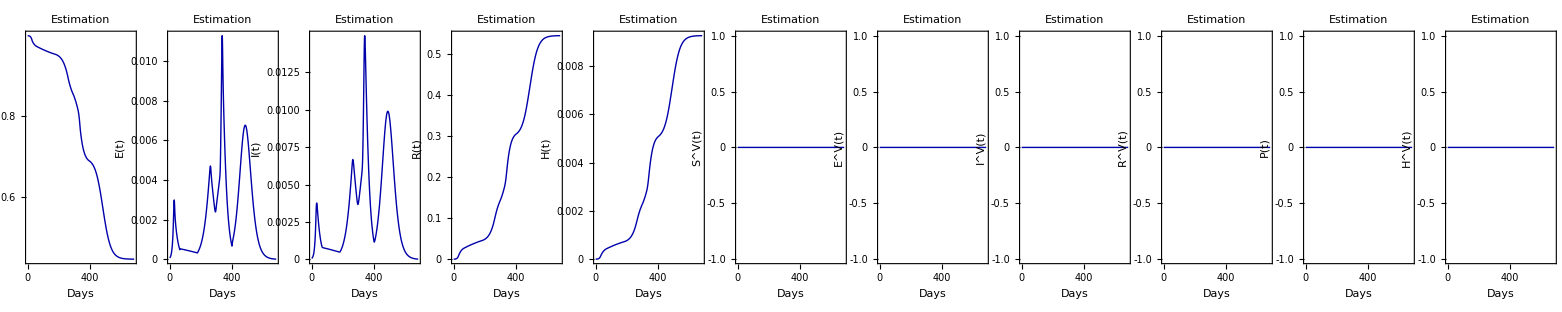

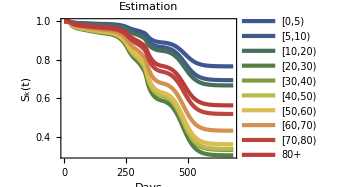
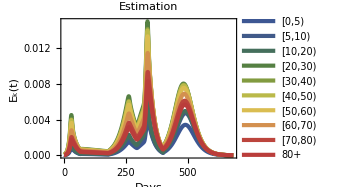
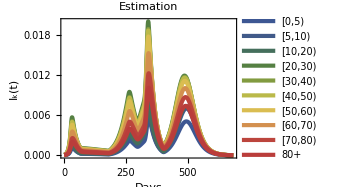
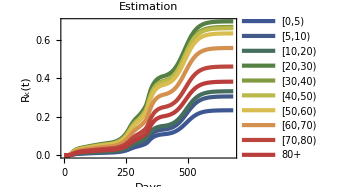
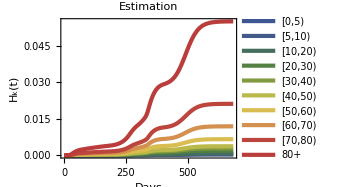
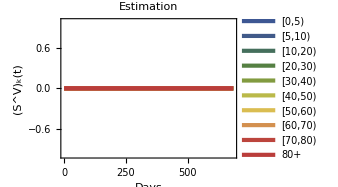
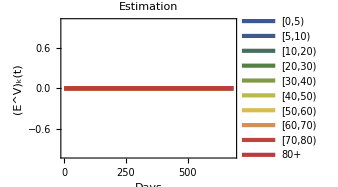
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Solutions with vaccination

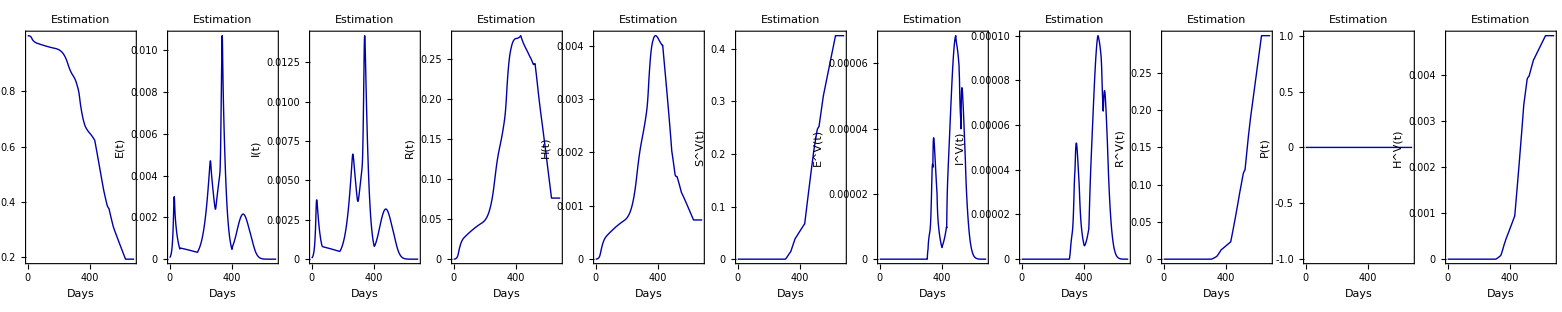

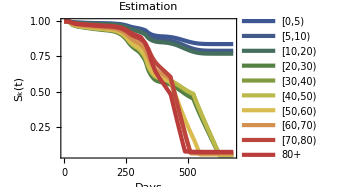
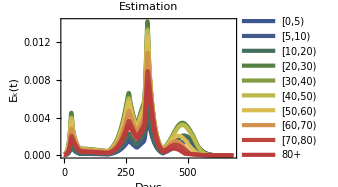
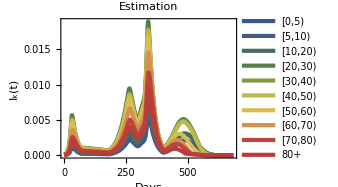
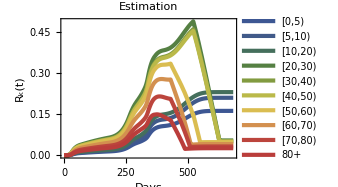
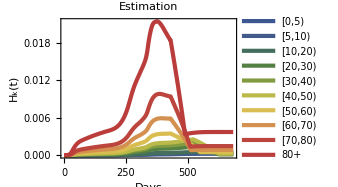
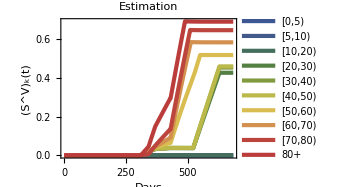
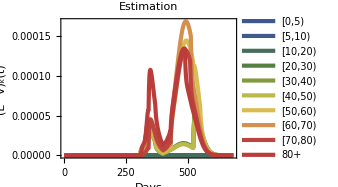
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Comparison solutions without and with vaccination

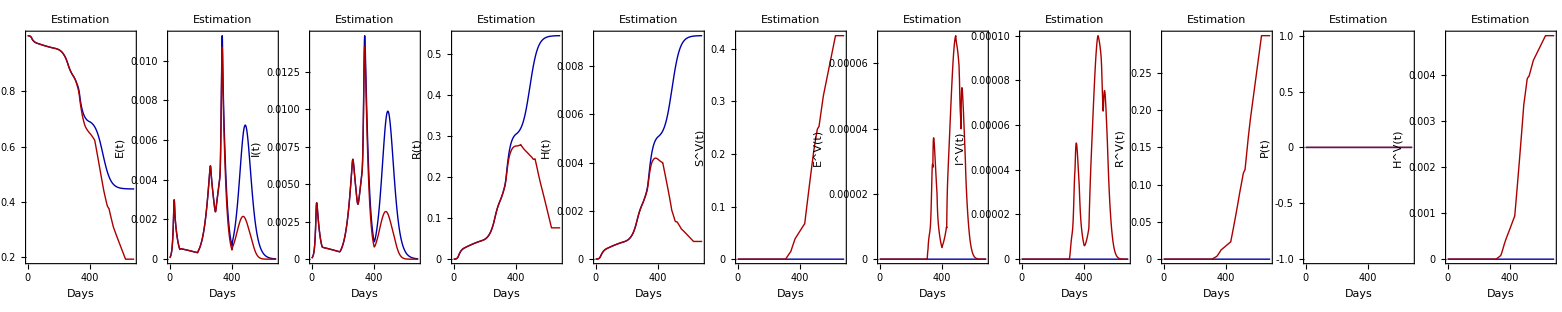

Comparison solutions without and with vaccination

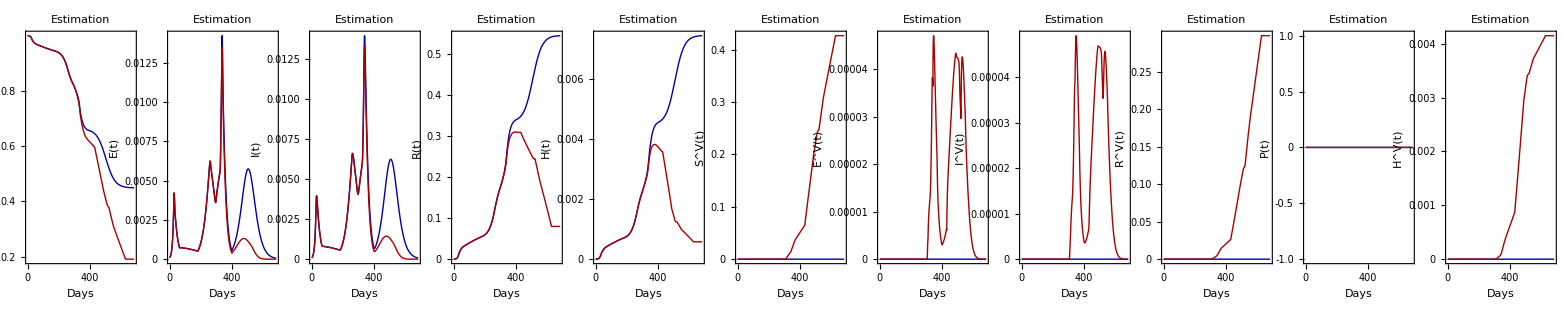

```mathematica
Print[Style["Solutions without vaccination",18,Blue,"Text"]]
PlottotVars[sol]
PlotageVars[sol]

Print[Style["Solutions with vaccination",18,Blue,"Text"]]
PlottotVars[solVac]
PlotageVars[solVac]

Print[Style["Comparison solutions without and with vaccination",18,Blue,"Text"]]
PlottotVarsComparison
```

# Execution

## Choose times and samples

```mathematica
Subscript[t, step]=1;
Subscript[t, end]=tendvac;

nSamples=Dimensions[EstimatesData]⟦1⟧;
stepSamples=40;
ListSamples=Table[i,{i,1,nSamples,stepSamples}];

NBDReparameterized[m_,f_]:=NegativeBinomialDistribution[f,f/(f+m)];

HospSimulated[var_]:=Table[If[var⟦k⟧⟦sample⟧⟦t⟧>0,RandomVariate[NBDReparameterized[var⟦k⟧⟦sample⟧⟦t⟧,rOverDisp[ListSamples⟦sample⟧]]],0],{k,AgeGroups},{sample,1,Length[ListSamples]},{t,1,Dimensions[var]⟦3⟧}];

ExportData[var_,filename_]:=Table[Export[StringJoin["MathematicaFiles//Scenario2//",filename,ToString[k],".txt"],var⟦k⟧,"Table"],{k,AgeGroups}];
```

## Solutions with credible intervals

## No vaccination

```mathematica
(**********************************************************)


ParametersAllNoVaccination=Table[ParametersNoVaccination[i],{i,1,nSamples,stepSamples}];

(*solAll=Table[NDSolve[Join[EqsList["Estimation"],ICsList]/.ParametersAllNoVaccination⟦i⟧,VarsList,{t,Subscript[t, start],Subscript[t, end]} ,Method->"StiffnessSwitching"],{i,1,Length[ListSamples]}];

Trajectories[var_]:=Table[Table[Table[Evaluate[(var⟦k⟧/.ParametersAllNoVaccination⟦i⟧)/.First@solAll⟦i⟧],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{i,1,Length[ListSamples]}],{k,AgeGroups}];

HospIncidence=Trajectories[hospVars];
ExportData[HospIncidence,"HospIncidence"];

InfIncidence=Trajectories[InfIncidenceVars];
ExportData[InfIncidence,"InfIncidence"];

HospIncidenceSimulated=HospSimulated[HospIncidence];
ExportData[HospIncidenceSimulated,"HospIncidenceSimulated"];

Memory*)
```

Memory Used:661.361 MB

## Solutions with credible intervals

## Vaccination

```mathematica
Clear[solAll,Trajectories]

ParametersAllVaccination=Table[ParametersVaccination[i],{i,1,nSamples,stepSamples}];

solAll=Table[NDSolve[Join[EqsList["Estimation"],ICsList]/.ParametersAllVaccination⟦i⟧,VarsList,{t,Subscript[t, start],Subscript[t, end]} ,Method->"StiffnessSwitching"],{i,1,Length[ListSamples]}];

Trajectories[var_]:=Table[Table[Table[Evaluate[(var⟦k⟧/.ParametersAllVaccination⟦i⟧)/.First@solAll⟦i⟧],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{i,1,Length[ListSamples]}],{k,AgeGroups}];

HospIncidenceVac=Trajectories[hospVars];
ExportData[HospIncidenceVac,"HospIncidenceVac"];

InfIncidenceVac=Trajectories[InfIncidenceVars];
ExportData[InfIncidenceVac,"InfIncidenceVac"];

HospIncidenceSimulatedVac=HospSimulated[HospIncidenceVac];
ExportData[HospIncidenceSimulatedVac,"HospIncidenceSimulatedVac"];

VaccinatedProportion=Trajectories[VacPropVars];
ExportData[VaccinatedProportion,"VaccinatedProportion"];

Susceptible=Trajectories[varsS];
ExportData[Susceptible,"Susceptible"];

SusceptibleVaccinated=Trajectories[varsSV];
ExportData[SusceptibleVaccinated,"SusceptibleVaccinated"];

ProtectedVaccine=Trajectories[ProtectedThroughVaccination];
ExportData[ProtectedVaccine,"ProtectedVaccine"];

ProtectedNaturalInfection=Trajectories[ProtectedThroughNaturalInfection];
ExportData[ProtectedNaturalInfection,"ProtectedNaturalInfection"];

Memory
```

Memory Used:371.188 MB

# Plotting

## Preliminaries

```mathematica
(*HospIncidence=Table[Import[StringJoin["MathematicaFiles//ModelFit//HospIncidence",ToString[k],".txt"],"Table"],{k,AgeGroups}];
InfIncidence=Table[Import[StringJoin["MathematicaFiles//ModelFit//InfIncidence",ToString[k],".txt"],"Table"],{k,AgeGroups}];
HospIncidenceSimulated=Table[Import[StringJoin["MathematicaFiles//ModelFit//HospIncidenceSimulated",ToString[k],".txt"],"Table"],{k,AgeGroups}];*)

HospIncidenceVac=Table[Import[StringJoin["MathematicaFiles//Scenario2//HospIncidenceVac",ToString[k],".txt"],"Table"],{k,AgeGroups}];
InfIncidenceVac=Table[Import[StringJoin["MathematicaFiles//Scenario2//InfIncidenceVac",ToString[k],".txt"],"Table"],{k,AgeGroups}];
HospIncidenceSimulatedVac=Table[Import[StringJoin["MathematicaFiles//Scenario2//HospIncidenceSimulatedVac",ToString[k],".txt"],"Table"],{k,AgeGroups}];
VaccinatedProportion=Table[Import[StringJoin["MathematicaFiles//Scenario2//VaccinatedProportion",ToString[k],".txt"],"Table"],{k,AgeGroups}];

Susceptible=Table[Import[StringJoin["MathematicaFiles//Scenario2//Susceptible",ToString[k],".txt"],"Table"],{k,AgeGroups}];
SusceptibleVaccinated=Table[Import[StringJoin["MathematicaFiles//Scenario2//SusceptibleVaccinated",ToString[k],".txt"],"Table"],{k,AgeGroups}];

ProtectedVaccine=Table[Import[StringJoin["MathematicaFiles//Scenario2//ProtectedVaccine",ToString[k],".txt"],"Table"],{k,AgeGroups}];
ProtectedNaturalInfection=Table[Import[StringJoin["MathematicaFiles//Scenario2//ProtectedNaturalInfection",ToString[k],".txt"],"Table"],{k,AgeGroups}];
```

## Plot vaccination coverage

Vaccinated proportion (%) in each age group

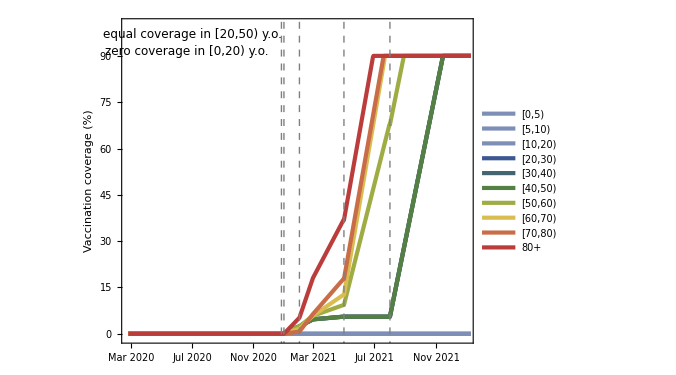

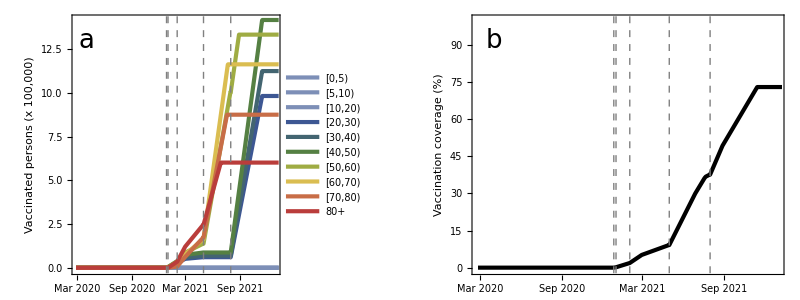

```mathematica
Print[Style["Vaccinated proportion (%) in each age group",24,Blue,"Text"]];

AspRat=0.75; ImSize=500;

tickValues=DateRange[{2020,3,1},{2022,1,1},{2,"Month"}][[All,{1,2}]];
ticks={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;

BarChartLegends=Style[#,Black]&/@{"[0,5)","[5,10)","[10,20)","[20,30)","[30,40)","[40,50)","[50,60)","[60,70)","[70,80)","80+"};

ChartStyleColors=Join[{Lighter[ColorData["DarkRainbow"][0]],Lighter[ColorData["DarkRainbow"][0]],Lighter[ColorData["DarkRainbow"][0]](*ColorData["DarkRainbow"][0],ColorData["DarkRainbow"][0],ColorData["DarkRainbow"][0]*)},ColorData["DarkRainbow"]/@Rescale[AgeGroups⟦1;;7⟧]];

LineWidthsAll=Table[Thickness[0.005],{k,AgeGroups}];

(*SFig5=Show[
DateListPlot[Table[VaccinatedProportion⟦k,1⟧ 100,{k,AgeGroups}],"February 25, 2020",PlotRange->{{"February 25, 2020","January 1, 2022"},{-1,100}},AspectRatio->AspRat,ImageSize->ImSize,PlotTheme->"Web",FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},
PlotRangePadding->None,AxesOrigin->{"February 25, 2020",0},FrameLabel-> {{"Vaccination coverage (%)",None},{None,None}},Filling->None,
FrameTicks->{{Automatic,None},{ticks,None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],PlotLegends->Placed[BarChartLegends,Scaled[{{0.25, 0.450}, {0.5,0.5 }}](*{After,Top}*)],PlotStyle->ChartStyleColors(*Transpose[{ChartStyleColors,LineWidthsAll}]*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}}],Graphics[Text[StyleForm["equal coverage in [20,50) y.o.",FontSize->12],Scaled[{0.2,0.95}]]],Graphics[Text[StyleForm["zero coverage in [0,20) y.o.",FontSize->12],Scaled[{0.185,0.9}]]]]

(*Table[Export[StringJoin["Figures//SFig5",format⟦i⟧],SFig5],{i,1,Length[format]}];*)

(*Labeled[Style[Text["curves coincide"],FontFamily->"Arial",FontSize->12],Alignment->{Top,Center}(*Close Labeled*)]*)

fig2A=Show[
DateListPlot[Table[VaccinatedProportion⟦k,1⟧ DemographyData10⟦k⟧,{k,AgeGroups}]/100000,"February 25, 2020",PlotRange->{{"February 25, 2020","January 1, 2022"},{-0.1,All}},AspectRatio->AspRat,ImageSize->ImSize,PlotTheme->"Web",FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},
PlotRangePadding->None,AxesOrigin->{"February 25, 2020",0},FrameLabel-> {{"Vaccinated persons (x 100,000)",None},{None,None}},Filling->None,
FrameTicks->{{Automatic,None},{ticks,None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],PlotLegends->Placed[BarChartLegends,Scaled[{{0.25, 0.50}, {0.5,0.5 }}](*{After,Top}*)],PlotStyle->ChartStyleColors(*Transpose[{ChartStyleColors,LineWidthsAll}]*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{Automatic,20},{Automatic,Automatic}}],Graphics[Text[StyleForm["a",FontSize->26],Scaled[{0.07,0.9}]]]];

(*Table[Export[StringJoin["Figures//Fig2A",format⟦i⟧],fig2A],{i,1,Length[format]}];*)

fig2B=Show[
DateListPlot[Sum[VaccinatedProportion⟦k,1⟧ DemographyData10⟦k⟧,{k,AgeGroups}] 100/Total[DemographyData10],"February 25, 2020",PlotRange->{{"February 25, 2020","January 1, 2022"},{-0.75,100}},AspectRatio->AspRat,ImageSize->ImSize,PlotTheme->"Web",FrameStyle->Directive[Black,17],Frame-> {{True,False},{True,False}},
PlotRangePadding->None,AxesOrigin->{"February 25, 2020",0},FrameLabel-> {{"Vaccination coverage (%)",None},{None,None}},Filling->None,
FrameTicks->{{Automatic,None},{ticks,None}},(*DateTicksFormat->(*{"DayShort","/","MonthShort","/","YearShort"}*){"MonthNameShort"," ","YearShort"},*)Prolog->Join[{Directive[{Dashed,Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],PlotStyle->{Black}(*,PlotLegends->Placed[Style[#,Black]&/@{"[20,80+) y.o."},Scaled[{{0.25, 0.50}, {0.5,0.5 }}](*{After,Top}*)],PlotStyle->Transpose[{ChartStyleColors,LineWidthsAll}]*),FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},ImagePadding->{{Automatic,20},{Automatic,Automatic}}],Graphics[Text[StyleForm["b",FontSize->26],Scaled[{0.07,0.9}]]]];


fig2=Grid[{{fig2A,fig2B}}]

(*Table[Export[StringJoin["Figures//Fig2",format⟦i⟧],fig2],{i,1,Length[format]}];*)*)
```

## Plotting functions

## Figures

New hospitalizations (per day) total

Median trajectories and credible intervals

({2020,2,25} | {2020,2,26} | {2020,2,27} | {2020,2,28} | {2020,2,29} | {2020,3,1} | {2020,3,2} | {2020,3,3} | {2020,3,4} | {2020,3,5} | {2020,3,6} | {2020,3,7} | {2020,3,8} | {2020,3,9} | {2020,3,10} | {2020,3,11} | {2020,3,12} | {2020,3,13} | {2020,3,14} | {2020,3,15} | {2020,3,16} | {2020,3,17} | {2020,3,18} | {2020,3,19} | {2020,3,20} | {2020,3,21} | {2020,3,22} | {2020,3,23} | {2020,3,24} | {2020,3,25} | {2020,3,26} | {2020,3,27} | {2020,3,28} | {2020,3,29} | {2020,3,30} | {2020,3,31} | {2020,4,1} | {2020,4,2} | {2020,4,3} | {2020,4,4} | {2020,4,5} | {2020,4,6} | {2020,4,7} | {2020,4,8} | {2020,4,9} | {2020,4,10} | {2020,4,11} | {2020,4,12} | {2020,4,13} | {2020,4,14} | {2020,4,15} | {2020,4,16} | {2020,4,17} | {2020,4,18} | {2020,4,19} | {2020,4,20} | {2020,4,21} | {2020,4,22} | {2020,4,23} | {2020,4,24} | {2020,4,25} | {2020,4,26} | {2020,4,27} | {2020,4,28} | {2020,4,29} | {2020,4,30} | {2020,5,1} | {2020,5,2} | {2020,5,3} | {2020,5,4} | {2020,5,5} | {2020,5,6} | {2020,5,7} | {2020,5,8} | {2020,5,9} | {2020,5,10} | {2020,5,11} | {2020,5,12} | {2020,5,13} | {2020,5,14} | {2020,5,15} | {2020,5,16} | {2020,5,17} | {2020,5,18} | {2020,5,19} | {2020,5,20} | {2020,5,21} | {2020,5,22} | {2020,5,23} | {2020,5,24} | {2020,5,25} | {2020,5,26} | {2020,5,27} | {2020,5,28} | {2020,5,29} | {2020,5,30} | {2020,5,31} | {2020,6,1} | {2020,6,2} | {2020,6,3} | {2020,6,4} | {2020,6,5} | {2020,6,6} | {2020,6,7} | {2020,6,8} | {2020,6,9} | {2020,6,10} | {2020,6,11} | {2020,6,12} | {2020,6,13} | {2020,6,14} | {2020,6,15} | {2020,6,16} | {2020,6,17} | {2020,6,18} | {2020,6,19} | {2020,6,20} | {2020,6,21} | {2020,6,22} | {2020,6,23} | {2020,6,24} | {2020,6,25} | {2020,6,26} | {2020,6,27} | {2020,6,28} | {2020,6,29} | {2020,6,30} | {2020,7,1} | {2020,7,2} | {2020,7,3} | {2020,7,4} | {2020,7,5} | {2020,7,6} | {2020,7,7} | {2020,7,8} | {2020,7,9} | {2020,7,10} | {2020,7,11} | {2020,7,12} | {2020,7,13} | {2020,7,14} | {2020,7,15} | {2020,7,16} | {2020,7,17} | {2020,7,18} | {2020,7,19} | {2020,7,20} | {2020,7,21} | {2020,7,22} | {2020,7,23} | {2020,7,24} | {2020,7,25} | {2020,7,26} | {2020,7,27} | {2020,7,28} | {2020,7,29} | {2020,7,30} | {2020,7,31} | {2020,8,1} | {2020,8,2} | {2020,8,3} | {2020,8,4} | {2020,8,5} | {2020,8,6} | {2020,8,7} | {2020,8,8} | {2020,8,9} | {2020,8,10} | {2020,8,11} | {2020,8,12} | {2020,8,13} | {2020,8,14} | {2020,8,15} | {2020,8,16} | {2020,8,17} | {2020,8,18} | {2020,8,19} | {2020,8,20} | {2020,8,21} | {2020,8,22} | {2020,8,23} | {2020,8,24} | {2020,8,25} | {2020,8,26} | {2020,8,27} | {2020,8,28} | {2020,8,29} | {2020,8,30} | {2020,8,31} | {2020,9,1} | {2020,9,2} | {2020,9,3} | {2020,9,4} | {2020,9,5} | {2020,9,6} | {2020,9,7} | {2020,9,8} | {2020,9,9} | {2020,9,10} | {2020,9,11} | {2020,9,12} | {2020,9,13} | {2020,9,14} | {2020,9,15} | {2020,9,16} | {2020,9,17} | {2020,9,18} | {2020,9,19} | {2020,9,20} | {2020,9,21} | {2020,9,22} | {2020,9,23} | {2020,9,24} | {2020,9,25} | {2020,9,26} | {2020,9,27} | {2020,9,28} | {2020,9,29} | {2020,9,30} | {2020,10,1} | {2020,10,2} | {2020,10,3} | {2020,10,4} | {2020,10,5} | {2020,10,6} | {2020,10,7} | {2020,10,8} | {2020,10,9} | {2020,10,10} | {2020,10,11} | {2020,10,12} | {2020,10,13} | {2020,10,14} | {2020,10,15} | {2020,10,16} | {2020,10,17} | {2020,10,18} | {2020,10,19} | {2020,10,20} | {2020,10,21} | {2020,10,22} | {2020,10,23} | {2020,10,24} | {2020,10,25} | {2020,10,26} | {2020,10,27} | {2020,10,28} | {2020,10,29} | {2020,10,30} | {2020,10,31} | {2020,11,1} | {2020,11,2} | {2020,11,3} | {2020,11,4} | {2020,11,5} | {2020,11,6} | {2020,11,7} | {2020,11,8} | {2020,11,9} | {2020,11,10} | {2020,11,11} | {2020,11,12} | {2020,11,13} | {2020,11,14} | {2020,11,15} | {2020,11,16} | {2020,11,17} | {2020,11,18} | {2020,11,19} | {2020,11,20} | {2020,11,21} | {2020,11,22} | {2020,11,23} | {2020,11,24} | {2020,11,25} | {2020,11,26} | {2020,11,27} | {2020,11,28} | {2020,11,29} | {2020,11,30} | {2020,12,1} | {2020,12,2} | {2020,12,3} | {2020,12,4} | {2020,12,5} | {2020,12,6} | {2020,12,7} | {2020,12,8} | {2020,12,9} | {2020,12,10} | {2020,12,11} | {2020,12,12} | {2020,12,13} | {2020,12,14} | {2020,12,15} | {2020,12,16} | {2020,12,17} | {2020,12,18} | {2020,12,19} | {2020,12,20} | {2020,12,21} | {2020,12,22} | {2020,12,23} | {2020,12,24} | {2020,12,25} | {2020,12,26} | {2020,12,27} | {2020,12,28} | {2020,12,29} | {2020,12,30} | {2020,12,31} | {2021,1,1} | {2021,1,2} | {2021,1,3} | {2021,1,4} | {2021,1,5} | {2021,1,6} | {2021,1,7} | {2021,1,8} | {2021,1,9} | {2021,1,10} | {2021,1,11} | {2021,1,12} | {2021,1,13} | {2021,1,14} | {2021,1,15} | {2021,1,16} | {2021,1,17} | {2021,1,18} | {2021,1,19} | {2021,1,20} | {2021,1,21} | {2021,1,22} | {2021,1,23} | {2021,1,24} | {2021,1,25} | {2021,1,26} | {2021,1,27} | {2021,1,28} | {2021,1,29} | {2021,1,30} | {2021,1,31} | {2021,2,1} | {2021,2,2} | {2021,2,3} | {2021,2,4} | {2021,2,5} | {2021,2,6} | {2021,2,7} | {2021,2,8} | {2021,2,9} | {2021,2,10} | {2021,2,11} | {2021,2,12} | {2021,2,13} | {2021,2,14} | {2021,2,15} | {2021,2,16} | {2021,2,17} | {2021,2,18} | {2021,2,19} | {2021,2,20} | {2021,2,21} | {2021,2,22} | {2021,2,23} | {2021,2,24} | {2021,2,25} | {2021,2,26} | {2021,2,27} | {2021,2,28} | {2021,3,1} | {2021,3,2} | {2021,3,3} | {2021,3,4} | {2021,3,5} | {2021,3,6} | {2021,3,7} | {2021,3,8} | {2021,3,9} | {2021,3,10} | {2021,3,11} | {2021,3,12} | {2021,3,13} | {2021,3,14} | {2021,3,15} | {2021,3,16} | {2021,3,17} | {2021,3,18} | {2021,3,19} | {2021,3,20} | {2021,3,21} | {2021,3,22} | {2021,3,23} | {2021,3,24} | {2021,3,25} | {2021,3,26} | {2021,3,27} | {2021,3,28} | {2021,3,29} | {2021,3,30} | {2021,3,31} | {2021,4,1} | {2021,4,2} | {2021,4,3} | {2021,4,4} | {2021,4,5} | {2021,4,6} | {2021,4,7} | {2021,4,8} | {2021,4,9} | {2021,4,10} | {2021,4,11} | {2021,4,12} | {2021,4,13} | {2021,4,14} | {2021,4,15} | {2021,4,16} | {2021,4,17} | {2021,4,18} | {2021,4,19} | {2021,4,20} | {2021,4,21} | {2021,4,22} | {2021,4,23} | {2021,4,24} | {2021,4,25} | {2021,4,26} | {2021,4,27} | {2021,4,28} | {2021,4,29} | {2021,4,30} | {2021,5,1} | {2021,5,2} | {2021,5,3} | {2021,5,4} | {2021,5,5} | {2021,5,6} | {2021,5,7} | {2021,5,8} | {2021,5,9} | {2021,5,10} | {2021,5,11} | {2021,5,12} | {2021,5,13} | {2021,5,14} | {2021,5,15} | {2021,5,16} | {2021,5,17} | {2021,5,18} | {2021,5,19} | {2021,5,20} | {2021,5,21} | {2021,5,22} | {2021,5,23} | {2021,5,24} | {2021,5,25} | {2021,5,26} | {2021,5,27} | {2021,5,28} | {2021,5,29} | {2021,5,30} | {2021,5,31} | {2021,6,1} | {2021,6,2} | {2021,6,3} | {2021,6,4} | {2021,6,5} | {2021,6,6} | {2021,6,7} | {2021,6,8} | {2021,6,9} | {2021,6,10} | {2021,6,11} | {2021,6,12} | {2021,6,13} | {2021,6,14} | {2021,6,15} | {2021,6,16} | {2021,6,17} | {2021,6,18} | {2021,6,19} | {2021,6,20} | {2021,6,21} | {2021,6,22} | {2021,6,23} | {2021,6,24} | {2021,6,25} | {2021,6,26} | {2021,6,27} | {2021,6,28} | {2021,6,29} | {2021,6,30} | {2021,7,1} | {2021,7,2} | {2021,7,3} | {2021,7,4} | {2021,7,5} | {2021,7,6} | {2021,7,7} | {2021,7,8} | {2021,7,9} | {2021,7,10} | {2021,7,11} | {2021,7,12} | {2021,7,13} | {2021,7,14} | {2021,7,15} | {2021,7,16} | {2021,7,17} | {2021,7,18} | {2021,7,19} | {2021,7,20} | {2021,7,21} | {2021,7,22} | {2021,7,23} | {2021,7,24} | {2021,7,25} | {2021,7,26} | {2021,7,27} | {2021,7,28} | {2021,7,29} | {2021,7,30} | {2021,7,31} | {2021,8,1} | {2021,8,2} | {2021,8,3} | {2021,8,4} | {2021,8,5} | {2021,8,6} | {2021,8,7} | {2021,8,8} | {2021,8,9} | {2021,8,10} | {2021,8,11} | {2021,8,12} | {2021,8,13} | {2021,8,14} | {2021,8,15} | {2021,8,16} | {2021,8,17} | {2021,8,18} | {2021,8,19} | {2021,8,20} | {2021,8,21} | {2021,8,22} | {2021,8,23} | {2021,8,24} | {2021,8,25} | {2021,8,26} | {2021,8,27} | {2021,8,28} | {2021,8,29} | {2021,8,30} | {2021,8,31} | {2021,9,1} | {2021,9,2} | {2021,9,3} | {2021,9,4} | {2021,9,5} | {2021,9,6} | {2021,9,7} | {2021,9,8} | {2021,9,9} | {2021,9,10} | {2021,9,11} | {2021,9,12} | {2021,9,13} | {2021,9,14} | {2021,9,15} | {2021,9,16} | {2021,9,17} | {2021,9,18} | {2021,9,19} | {2021,9,20} | {2021,9,21} | {2021,9,22} | {2021,9,23} | {2021,9,24} | {2021,9,25} | {2021,9,26} | {2021,9,27} | {2021,9,28} | {2021,9,29} | {2021,9,30} | {2021,10,1} | {2021,10,2} | {2021,10,3} | {2021,10,4} | {2021,10,5} | {2021,10,6} | {2021,10,7} | {2021,10,8} | {2021,10,9} | {2021,10,10} | {2021,10,11} | {2021,10,12} | {2021,10,13} | {2021,10,14} | {2021,10,15} | {2021,10,16} | {2021,10,17} | {2021,10,18} | {2021,10,19} | {2021,10,20} | {2021,10,21} | {2021,10,22} | {2021,10,23} | {2021,10,24} | {2021,10,25} | {2021,10,26} | {2021,10,27} | {2021,10,28} | {2021,10,29} | {2021,10,30} | {2021,10,31} | {2021,11,1} | {2021,11,2} | {2021,11,3} | {2021,11,4} | {2021,11,5} | {2021,11,6} | {2021,11,7} | {2021,11,8} | {2021,11,9} | {2021,11,10} | {2021,11,11} | {2021,11,12} | {2021,11,13} | {2021,11,14} | {2021,11,15} | {2021,11,16} | {2021,11,17} | {2021,11,18} | {2021,11,19} | {2021,11,20} | {2021,11,21} | {2021,11,22} | {2021,11,23} | {2021,11,24} | {2021,11,25} | {2021,11,26} | {2021,11,27} | {2021,11,28} | {2021,11,29} | {2021,11,30} | {2021,12,1} | {2021,12,2} | {2021,12,3} | {2021,12,4} | {2021,12,5} | {2021,12,6} | {2021,12,7} | {2021,12,8} | {2021,12,9} | {2021,12,10} | {2021,12,11} | {2021,12,12} | {2021,12,13} | {2021,12,14} | {2021,12,15} | {2021,12,16} | {2021,12,17} | {2021,12,18} | {2021,12,19} | {2021,12,20} | {2021,12,21} | {2021,12,22} | {2021,12,23} | {2021,12,24} | {2021,12,25} | {2021,12,26} | {2021,12,27} | {2021,12,28} | {2021,12,29} | {2021,12,30} | {2021,12,31} | {2022,1,1} | {2022,1,2} | {2022,1,3} | {2022,1,4} | {2022,1,5} | {2022,1,6} | {2022,1,7} | {2022,1,8} | {2022,1,9} | {2022,1,10}
3.42547 | 3.64 | 3.88415 | 4.16745 | 4.53376 | 5.00192 | 5.56819 | 6.24216 | 7.04722 | 7.99854 | 9.11391 | 10.4253 | 11.9614 | 13.7561 | 15.9073 | 18.3396 | 21.1955 | 24.6075 | 28.4131 | 32.9374 | 38.051 | 44.0304 | 51.1611 | 59.2741 | 68.4115 | 78.7491 | 89.9595 | 102.379 | 114.258 | 124.987 | 133.435 | 138.792 | 141.839 | 142.723 | 141.351 | 138.934 | 135.851 | 132.167 | 128.083 | 123.709 | 119.213 | 114.666 | 110.272 | 105.85 | 101.641 | 97.3799 | 93.221 | 89.2044 | 85.2566 | 81.3137 | 77.5779 | 73.9396 | 70.5433 | 67.3589 | 64.2148 | 61.183 | 58.2642 | 55.458 | 52.7284 | 50.1196 | 47.628 | 45.271 | 43.0371 | 41.2017 | 39.5668 | 37.8498 | 36.7912 | 35.9316 | 35.2279 | 34.6877 | 34.2527 | 33.875 | 33.5417 | 33.2458 | 32.9899 | 32.7667 | 32.5634 | 32.377 | 32.2052 | 32.0457 | 31.8953 | 31.7568 | 31.6258 | 31.501 | 31.3807 | 31.2529 | 31.1276 | 31.0055 | 30.8828 | 30.7604 | 30.6529 | 30.5435 | 30.4386 | 30.3346 | 30.2313 | 30.1211 | 30.0014 | 29.8963 | 29.7904 | 29.6829 | 29.5753 | 29.4658 | 29.3554 | 29.2428 | 29.1223 | 29.0015 | 28.8886 | 28.7874 | 28.6855 | 28.5723 | 28.4587 | 28.3559 | 28.263 | 28.1454 | 28.0276 | 27.9168 | 27.811 | 27.6951 | 27.5913 | 27.4764 | 27.3502 | 27.2359 | 27.1246 | 27.0232 | 26.9213 | 26.8261 | 26.7122 | 26.5882 | 26.4675 | 26.3465 | 26.2308 | 26.1106 | 26.0061 | 25.9013 | 25.7961 | 25.6885 | 25.5723 | 25.4614 | 25.3421 | 25.2205 | 25.0978 | 24.9776 | 24.856 | 24.7343 | 24.6126 | 24.4908 | 24.3691 | 24.2473 | 24.1256 | 24.0038 | 23.8821 | 23.7604 | 23.6387 | 23.5171 | 23.3997 | 23.2848 | 23.1698 | 23.0534 | 22.9368 | 22.8201 | 22.7034 | 22.5866 | 22.4698 | 22.3539 | 22.243 | 22.1299 | 22.0168 | 21.9037 | 21.7892 | 21.6744 | 21.56 | 21.4459 | 21.3328 | 21.2221 | 21.116 | 21.0177 | 20.928 | 20.8511 | 20.8026 | 20.8974 | 20.9776 | 21.2022 | 21.5203 | 22.0183 | 22.5951 | 23.2125 | 23.8851 | 24.6218 | 25.3807 | 26.1956 | 27.0794 | 27.9845 | 28.935 | 29.9143 | 30.9416 | 32.022 | 33.1347 | 34.2897 | 35.4881 | 36.7306 | 38.0182 | 39.3528 | 40.7522 | 42.1895 | 43.6586 | 45.1786 | 46.7368 | 48.3544 | 50.0348 | 51.7824 | 53.5884 | 55.4765 | 57.4397 | 59.4725 | 61.5699 | 63.7112 | 65.9051 | 68.1683 | 70.5294 | 72.9232 | 75.3897 | 77.9125 | 80.5349 | 83.2562 | 86.0678 | 88.9625 | 91.9418 | 95.008 | 98.1297 | 101.339 | 104.638 | 108.026 | 111.502 | 115.048 | 118.681 | 122.402 | 126.175 | 130.022 | 134.091 | 138.24 | 142.523 | 146.791 | 151.146 | 155.589 | 160.118 | 164.781 | 169.625 | 174.576 | 179.684 | 184.965 | 190.091 | 195.267 | 200.509 | 205.917 | 211.549 | 217.083 | 222.376 | 227.518 | 232.674 | 237.243 | 240.739 | 244.483 | 247.16 | 248.69 | 250.606 | 249.857 | 248.938 | 248.157 | 246.566 | 244.584 | 242.314 | 239.967 | 237.411 | 234.568 | 231.724 | 228.907 | 225.822 | 222.501 | 219.327 | 216.019 | 212.725 | 209.628 | 206.672 | 203.307 | 199.92 | 196.503 | 193.276 | 189.982 | 186.556 | 183.244 | 179.696 | 176.103 | 172.944 | 170.036 | 167.126 | 164.581 | 162.021 | 159.778 | 158.367 | 157.442 | 158.543 | 159.85 | 161.213 | 162.889 | 164.731 | 167.25 | 170.073 | 173.003 | 175.975 | 179.162 | 182.287 | 185.41 | 188.661 | 191.854 | 195.068 | 198.639 | 201.953 | 205.11 | 208.323 | 211.858 | 215.333 | 218.7 | 222.329 | 225.587 | 229.684 | 234.706 | 241.369 | 252.035 | 266.612 | 284.498 | 305.132 | 330.014 | 356.777 | 384.442 | 413.775 | 443.783 | 473.469 | 500.898 | 527.953 | 550.019 | 565.118 | 573.6 | 577.561 | 570.686 | 562.124 | 552.542 | 538.631 | 521.192 | 505.167 | 488.17 | 469.604 | 452.036 | 434.531 | 418.061 | 402.615 | 388.428 | 373.51 | 357.61 | 341.389 | 325.6 | 309.377 | 294.531 | 280.186 | 266.357 | 253.05 | 240.262 | 227.989 | 216.538 | 205.589 | 194.98 | 184.789 | 175.062 | 165.789 | 156.96 | 148.587 | 140.767 | 133.328 | 126.254 | 119.531 | 113.142 | 107.074 | 101.312 | 95.8432 | 90.6544 | 85.7322 | 81.0638 | 76.6379 | 72.4431 | 68.4685 | 64.7028 | 61.1358 | 57.7579 | 54.5598 | 51.5324 | 48.6674 | 45.9562 | 43.391 | 40.9649 | 38.671 | 36.5029 | 34.4704 | 32.6433 | 31.3799 | 30.7925 | 30.6419 | 30.7793 | 31.1295 | 31.6088 | 32.1845 | 32.7905 | 33.4211 | 34.119 | 34.8782 | 35.6939 | 36.5624 | 37.4101 | 38.2489 | 39.1276 | 40.0444 | 40.9972 | 41.9848 | 43.0058 | 44.0591 | 45.1436 | 46.2586 | 47.4031 | 48.5765 | 49.778 | 51.0979 | 52.5338 | 54.0081 | 55.5223 | 57.0761 | 58.6453 | 60.2098 | 61.7582 | 63.2832 | 64.7811 | 66.2503 | 67.6892 | 69.0969 | 70.4731 | 71.7316 | 72.6073 | 73.4359 | 74.2179 | 74.9534 | 75.6425 | 76.2852 | 76.8814 | 77.4308 | 77.933 | 78.3878 | 78.7947 | 79.1534 | 79.4634 | 79.7244 | 79.936 | 80.0978 | 80.4345 | 80.899 | 81.3146 | 81.6803 | 81.9951 | 82.2581 | 82.4685 | 82.6257 | 82.7288 | 82.7775 | 82.7712 | 82.7096 | 82.5924 | 82.4195 | 82.1066 | 81.5311 | 80.9036 | 80.2252 | 79.4969 | 78.705 | 77.8033 | 76.859 | 75.8739 | 74.8495 | 73.7876 | 72.705 | 71.8998 | 71.0518 | 70.1624 | 69.233 | 68.2653 | 67.262 | 66.2427 | 65.23 | 64.234 | 63.2579 | 62.2993 | 61.3552 | 60.4217 | 59.4944 | 58.5698 | 57.5664 | 56.2339 | 54.9113 | 53.5978 | 52.2928 | 51.4664 | 50.7587 | 50.0371 | 49.3017 | 48.5526 | 47.7901 | 47.0099 | 45.784 | 44.5814 | 43.4138 | 42.253 | 40.9927 | 39.7919 | 38.6455 | 37.5482 | 36.4941 | 35.4781 | 34.4957 | 33.5442 | 32.6216 | 31.716 | 30.823 | 30.1195 | 29.4111 | 28.6963 | 27.9746 | 27.2465 | 26.513 | 25.7746 | 25.0324 | 24.2875 | 23.5415 | 22.7957 | 22.0517 | 21.3896 | 20.6629 | 19.7934 | 18.9449 | 18.1179 | 17.3127 | 16.5298 | 15.7594 | 14.9814 | 14.3814 | 13.8461 | 13.3474 | 12.7924 | 12.2799 | 11.7789 | 11.2445 | 10.7157 | 10.2683 | 9.78574 | 9.37205 | 8.9712 | 8.58298 | 8.20718 | 7.84358 | 7.49197 | 7.14538 | 6.79594 | 6.45479 | 6.12658 | 5.81108 | 5.48184 | 5.16649 | 4.86635 | 4.58087 | 4.34027 | 4.11142 | 3.87708 | 3.64859 | 3.41707 | 3.19159 | 2.97487 | 2.768 | 2.57398 | 2.39215 | 2.22428 | 2.07772 | 1.93962 | 1.80959 | 1.68673 | 1.56531 | 1.45167 | 1.34539 | 1.24609 | 1.15337 | 1.06714 | 0.992206 | 0.921984 | 0.857778 | 0.797114 | 0.738827 | 0.684394 | 0.634763 | 0.58792 | 0.544242 | 0.503546 | 0.467786 | 0.434367 | 0.403101 | 0.373871 | 0.346566 | 0.321079 | 0.296892 | 0.273878 | 0.252519 | 0.23271 | 0.214349 | 0.197135 | 0.181033 | 0.166161 | 0.152431 | 0.139764 | 0.128086 | 0.11742 | 0.108122 | 0.0995146 | 0.0910423 | 0.0831168 | 0.0758401 | 0.0691621 | 0.0630374 | 0.057379 | 0.0521603 | 0.0474004 | 0.0431128 | 0.0392565 | 0.0357508 | 0.0325667 | 0.0296759 | 0.0270502 | 0.0246644 | 0.0224982 | 0.020532 | 0.0187462 | 0.0171215 | 0.0156429 | 0.0142983 | 0.0130759 | 0.0119637 | 0.0109498 | 0.0100243 | 0.00918031 | 0.00841062 | 0.00774071 | 0.00715246 | 0.0066106 | 0.00611174 | 0.00565246 | 0.00522936 | 0.00483903 | 0.00447828 | 0.00414495 | 0.0038372 | 0.00355318 | 0.00328009 | 0.00301917 | 0.00277952 | 0.00255899 | 0.00235581 | 0.00216868 | 0.00199653 | 0.00183831 | 0.00169298 | 0.00155947 | 0.00143674 | 0.00132373 | 0.00121952 | 0.00112342 | 0.00103491 | 0.000953451 | 0.00087848 | 0.000809436 | 0.00074579 | 0.000687133 | 0.000633115 | 0.000583387 | 0.000537602 | 0.000495412
1 | 1 | 0 | 1 | 1 | 1 | 2 | 3 | 2 | 4 | 4 | 6 | 5 | 7 | 11 | 10 | 13 | 16 | 21 | 22 | 28 | 29 | 34 | 43 | 51 | 66 | 73 | 80 | 93 | 100 | 106 | 111 | 118 | 114 | 116 | 111 | 106 | 102 | 104 | 97 | 96 | 87 | 86 | 87 | 79 | 80 | 71 | 68 | 66 | 63 | 61 | 53 | 56 | 54 | 43 | 49 | 40 | 44 | 38 | 34 | 36 | 33 | 31 | 28 | 27 | 24 | 26 | 21 | 26 | 25 | 21 | 26 | 20 | 24 | 23 | 23 | 20 | 24 | 22 | 21 | 19 | 24 | 20 | 22 | 21 | 20 | 19 | 21 | 21 | 18 | 20 | 16 | 20 | 20 | 21 | 19 | 19 | 17 | 20 | 20 | 17 | 21 | 19 | 20 | 17 | 19 | 21 | 19 | 19 | 15 | 16 | 19 | 19 | 17 | 19 | 19 | 19 | 18 | 17 | 17 | 16 | 19 | 16 | 17 | 17 | 16 | 19 | 16 | 16 | 18 | 15 | 15 | 16 | 15 | 18 | 19 | 13 | 16 | 15 | 17 | 18 | 17 | 19 | 15 | 15 | 14 | 17 | 14 | 14 | 16 | 15 | 14 | 16 | 15 | 17 | 15 | 13 | 15 | 15 | 16 | 14 | 15 | 14 | 14 | 15 | 13 | 11 | 14 | 16 | 11 | 14 | 13 | 15 | 14 | 12 | 12 | 14 | 13 | 12 | 13 | 13 | 14 | 11 | 13 | 13 | 17 | 15 | 9 | 17 | 18 | 18 | 19 | 19 | 21 | 21 | 18 | 25 | 16 | 23 | 27 | 28 | 25 | 25 | 31 | 27 | 34 | 31 | 37 | 34 | 36 | 46 | 40 | 41 | 45 | 43 | 42 | 48 | 49 | 52 | 60 | 57 | 57 | 61 | 65 | 68 | 67 | 72 | 74 | 81 | 81 | 82 | 86 | 90 | 84 | 91 | 99 | 104 | 103 | 113 | 116 | 115 | 121 | 122 | 129 | 137 | 131 | 135 | 144 | 158 | 165 | 161 | 163 | 167 | 178 | 171 | 180 | 191 | 172 | 185 | 205 | 201 | 203 | 203 | 211 | 210 | 210 | 221 | 212 | 203 | 209 | 198 | 198 | 206 | 204 | 190 | 203 | 193 | 186 | 186 | 185 | 178 | 174 | 183 | 171 | 164 | 158 | 164 | 163 | 156 | 147 | 140 | 147 | 144 | 144 | 137 | 132 | 135 | 123 | 124 | 126 | 134 | 132 | 128 | 134 | 141 | 140 | 145 | 143 | 149 | 155 | 144 | 154 | 150 | 152 | 157 | 173 | 160 | 168 | 168 | 165 | 172 | 180 | 183 | 191 | 199 | 186 | 208 | 206 | 230 | 217 | 261 | 279 | 297 | 305 | 357 | 363 | 379 | 397 | 412 | 437 | 462 | 469 | 470 | 453 | 442 | 430 | 412 | 373 | 372 | 357 | 385 | 332 | 316 | 320 | 271 | 297 | 272 | 228 | 252 | 238 | 214 | 204 | 196 | 188 | 171 | 168 | 152 | 143 | 141 | 133 | 107 | 123 | 111 | 85 | 91 | 88 | 91 | 75 | 78 | 63 | 56 | 57 | 59 | 51 | 52 | 45 | 48 | 39 | 39 | 37 | 31 | 33 | 32 | 25 | 24 | 16 | 22 | 18 | 16 | 16 | 16 | 14 | 14 | 11 | 14 | 15 | 11 | 14 | 13 | 14 | 13 | 13 | 16 | 15 | 15 | 11 | 14 | 16 | 13 | 16 | 18 | 19 | 13 | 17 | 21 | 17 | 20 | 16 | 18 | 17 | 14 | 15 | 21 | 17 | 18 | 23 | 19 | 27 | 25 | 23 | 20 | 27 | 28 | 22 | 24 | 30 | 25 | 23 | 26 | 29 | 22 | 26 | 25 | 24 | 21 | 27 | 22 | 24 | 27 | 23 | 31 | 25 | 22 | 25 | 24 | 30 | 19 | 19 | 28 | 27 | 22 | 21 | 26 | 29 | 16 | 20 | 22 | 24 | 21 | 18 | 24 | 19 | 14 | 20 | 19 | 18 | 21 | 19 | 17 | 18 | 13 | 18 | 14 | 15 | 13 | 13 | 18 | 13 | 20 | 16 | 14 | 16 | 15 | 19 | 14 | 15 | 11 | 13 | 12 | 16 | 10 | 9 | 13 | 13 | 10 | 12 | 8 | 9 | 16 | 12 | 9 | 10 | 6 | 8 | 10 | 10 | 8 | 13 | 7 | 8 | 7 | 7 | 5 | 5 | 9 | 9 | 4 | 4 | 6 | 4 | 6 | 9 | 6 | 5 | 5 | 5 | 4 | 4 | 5 | 5 | 4 | 4 | 2 | 2 | 3 | 3 | 1 | 3 | 3 | 1 | 2 | 2 | 1 | 1 | 2 | 1 | 1 | 1 | 2 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
7 | 7 | 9 | 9 | 9 | 10 | 8 | 12 | 13 | 13 | 14 | 17 | 19 | 19 | 25 | 26 | 33 | 37 | 44 | 45 | 59 | 57 | 76 | 78 | 79 | 100 | 117 | 119 | 148 | 147 | 160 | 169 | 177 | 165 | 167 | 172 | 158 | 161 | 147 | 148 | 146 | 143 | 143 | 137 | 124 | 124 | 113 | 113 | 101 | 95 | 95 | 95 | 92 | 87 | 82 | 76 | 75 | 73 | 77 | 65 | 65 | 61 | 54 | 56 | 55 | 56 | 47 | 49 | 48 | 46 | 48 | 47 | 46 | 45 | 42 | 45 | 43 | 42 | 41 | 44 | 41 | 40 | 44 | 43 | 40 | 44 | 41 | 42 | 45 | 41 | 42 | 42 | 41 | 45 | 41 | 41 | 39 | 40 | 41 | 41 | 48 | 40 | 36 | 42 | 38 | 41 | 38 | 38 | 38 | 41 | 36 | 39 | 40 | 42 | 36 | 38 | 39 | 38 | 37 | 37 | 39 | 39 | 38 | 39 | 37 | 35 | 41 | 39 | 37 | 38 | 36 | 35 | 36 | 36 | 35 | 34 | 37 | 36 | 35 | 35 | 36 | 33 | 37 | 36 | 33 | 33 | 36 | 35 | 37 | 35 | 31 | 33 | 32 | 34 | 34 | 35 | 34 | 35 | 31 | 33 | 32 | 33 | 32 | 30 | 32 | 31 | 32 | 31 | 30 | 30 | 33 | 28 | 34 | 30 | 29 | 29 | 29 | 35 | 30 | 30 | 32 | 28 | 33 | 32 | 35 | 35 | 32 | 34 | 35 | 34 | 36 | 38 | 39 | 45 | 42 | 43 | 46 | 44 | 49 | 50 | 57 | 50 | 54 | 57 | 53 | 58 | 58 | 61 | 64 | 67 | 72 | 68 | 70 | 80 | 85 | 79 | 86 | 87 | 96 | 95 | 94 | 100 | 112 | 104 | 108 | 101 | 114 | 117 | 123 | 129 | 128 | 137 | 133 | 145 | 151 | 151 | 160 | 154 | 155 | 175 | 177 | 174 | 189 | 185 | 192 | 193 | 199 | 196 | 217 | 230 | 231 | 226 | 239 | 247 | 238 | 262 | 259 | 269 | 283 | 282 | 285 | 286 | 306 | 283 | 306 | 304 | 292 | 292 | 297 | 283 | 293 | 294 | 270 | 282 | 260 | 300 | 272 | 253 | 261 | 260 | 260 | 246 | 252 | 250 | 238 | 237 | 228 | 230 | 208 | 206 | 206 | 215 | 209 | 205 | 205 | 206 | 204 | 206 | 188 | 190 | 196 | 198 | 192 | 194 | 194 | 201 | 206 | 221 | 217 | 209 | 204 | 215 | 217 | 231 | 232 | 236 | 233 | 243 | 247 | 237 | 254 | 255 | 265 | 260 | 266 | 278 | 313 | 299 | 317 | 341 | 357 | 382 | 420 | 462 | 507 | 532 | 586 | 620 | 702 | 706 | 742 | 733 | 700 | 724 | 708 | 717 | 702 | 706 | 673 | 654 | 675 | 637 | 586 | 538 | 582 | 536 | 526 | 495 | 508 | 475 | 443 | 459 | 412 | 427 | 392 | 359 | 348 | 339 | 357 | 297 | 295 | 249 | 285 | 225 | 248 | 234 | 217 | 233 | 202 | 199 | 190 | 166 | 164 | 156 | 140 | 128 | 151 | 125 | 135 | 125 | 111 | 121 | 105 | 100 | 98 | 92 | 100 | 126 | 85 | 75 | 68 | 87 | 75 | 63 | 61 | 61 | 72 | 69 | 71 | 87 | 72 | 75 | 88 | 84 | 83 | 96 | 107 | 100 | 103 | 104 | 135 | 125 | 123 | 141 | 127 | 138 | 139 | 148 | 149 | 152 | 159 | 181 | 183 | 177 | 189 | 190 | 198 | 209 | 233 | 180 | 252 | 236 | 212 | 256 | 240 | 251 | 263 | 256 | 271 | 268 | 287 | 293 | 303 | 288 | 284 | 295 | 331 | 311 | 320 | 306 | 269 | 320 | 313 | 294 | 350 | 309 | 312 | 326 | 330 | 284 | 287 | 281 | 307 | 371 | 319 | 298 | 334 | 316 | 302 | 302 | 296 | 302 | 302 | 236 | 314 | 259 | 273 | 247 | 243 | 189 | 225 | 204 | 207 | 180 | 204 | 192 | 179 | 184 | 175 | 187 | 148 | 175 | 148 | 143 | 144 | 131 | 133 | 123 | 133 | 101 | 110 | 105 | 98 | 106 | 103 | 97 | 88 | 86 | 85 | 75 | 84 | 71 | 66 | 67 | 60 | 70 | 67 | 58 | 66 | 53 | 56 | 53 | 49 | 49 | 53 | 61 | 43 | 37 | 43 | 38 | 38 | 34 | 36 | 32 | 32 | 34 | 34 | 31 | 24 | 26 | 28 | 29 | 23 | 24 | 18 | 22 | 18 | 22 | 17 | 21 | 15 | 16 | 17 | 13 | 15 | 13 | 14 | 14 | 12 | 11 | 10 | 9 | 8 | 11 | 7 | 8 | 9 | 8 | 9 | 6 | 6 | 7 | 8 | 6 | 7 | 6 | 6 | 6 | 5 | 5 | 5 | 5 | 4 | 4 | 3 | 4 | 5 | 3 | 3 | 3 | 2 | 4 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 1 | 2 | 1 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

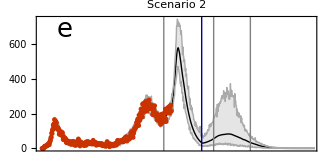

```mathematica
Print[Style["New hospitalizations (per day) total",24,Blue,"Text"]];
Print[Style["Median trajectories and credible intervals",24,Blue,"Text"]];

AspRat=0.5; ImSize=330;
tickValues=DateRange[{2020,3,1},{2022,1,1},{2,"Month"}][[All,{1,2}]];
ticks={#,Rotate[DateString[DateObject[#],{"MonthNameShort"," ","Year"}],π/2]}&/@tickValues;

DataPlotAll:=DateListPlot[Total[Transpose[HospitalisationsData]],"February 26, 2020",PlotMarkers->{Automatic,5},PlotTheme->"Web",Joined-> False,DateTicksFormat->{"MonthShort","/","YearShort"}];

indexlist ={20,22,24,26,28};
TransitionDates=Join[Table[DayPlus[{2020,02,25}, IntegerPart[Median[EstimatesData⟦All,index⟧]]],{index,indexlist}],{DayPlus[{2020,02,25},x6]}];

ImSize=330;

PlotTotalDataAndModel[Var_,VarSimulated_,tendplot_,onlydata_,plotlabel_]:=Show[DateListPlot[{Median[Total[Var]],(*Quantile[Total[Var],0.025],Quantile[Total[Var],0.975],*)Quantile[Total[VarSimulated],0.025],Quantile[Total[VarSimulated],0.975]},"February 25, 2020",FrameTicks->{{Automatic,None},{None (*ticks*),None}},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,PlotRange->{{"February 25, 2020",tendplot},{0,If[onlydata==True,Max[Quantile[Total[VarSimulated],0.975]⟦1;;tenddata⟧],All]}},Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,14],FrameLabel-> {{(*"Hospitalizations (1/day)"*)None,None},{None,None}},Filling->{{3->{2}}(*,{5->{4}}*)},PlotStyle->{{Black,Thick},{Lighter[Gray],Thin},{Lighter[Gray],Thin}(*,{Lighter[Gray],Thin},{Lighter[Gray],Thin}*)},PlotLabel->Style[Row[{plotlabel}],Black,14],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},Prolog->{Join[{Directive[{Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],Join[{Directive[{Darker[Blue]}],InfiniteLine[{DayPlus[{2020,02,25},x7],0},{0,1}]}]},ImagePadding->{{55, 5}, {Automatic, Automatic}}],DataPlotAll(*,PanelLetter[k]*),Graphics[Text[StyleForm["e",FontSize->26],Scaled[{0.1,0.9}]]]];

{DateRange[{2020,02,25},{2022,1,10},{1,"Day"}],Median[Total[HospIncidenceVac]],Quantile[Total[HospIncidenceSimulatedVac],0.025],Quantile[Total[HospIncidenceSimulatedVac],0.975]}//MatrixForm

Fig5e=PlotTotalDataAndModel[HospIncidenceVac,HospIncidenceSimulatedVac,"January 1, 2022",False,"Scenario 2"]
```

```mathematica
HospIncidenceVac//Dimensions
Total[HospIncidenceVac]//Dimensions
Transpose[Total[HospIncidenceVac]]//Dimensions
Accumulate[Transpose[Total[HospIncidenceVac]]]//Dimensions
Transpose[Accumulate[Transpose[Total[HospIncidenceVac]]]]//Dimensions
Median[Transpose[Accumulate[Transpose[Total[HospIncidenceVac]]]]]//Dimensions

CalCumVar[var_]:=Median[Transpose[Accumulate[Transpose[Total[var]]]]];

cumhosp={DateRange[{2020,02,25},{2022,1,10},{1,"Day"}],CalCumVar[HospIncidenceVac]};
cumhosp//MatrixForm

cumhosp⟦All,402⟧

cumhosp⟦All,Dimensions[cumhosp]⟦2⟧⟧

cumhosp⟦2,Dimensions[cumhosp]⟦2⟧⟧-cumhosp⟦2,402⟧
```

{10,50,686}

{50,686}

{686,50}

{686,50}

{50,686}

{686}

({2020,2,25} | {2020,2,26} | {2020,2,27} | {2020,2,28} | {2020,2,29} | {2020,3,1} | {2020,3,2} | {2020,3,3} | {2020,3,4} | {2020,3,5} | {2020,3,6} | {2020,3,7} | {2020,3,8} | {2020,3,9} | {2020,3,10} | {2020,3,11} | {2020,3,12} | {2020,3,13} | {2020,3,14} | {2020,3,15} | {2020,3,16} | {2020,3,17} | {2020,3,18} | {2020,3,19} | {2020,3,20} | {2020,3,21} | {2020,3,22} | {2020,3,23} | {2020,3,24} | {2020,3,25} | {2020,3,26} | {2020,3,27} | {2020,3,28} | {2020,3,29} | {2020,3,30} | {2020,3,31} | {2020,4,1} | {2020,4,2} | {2020,4,3} | {2020,4,4} | {2020,4,5} | {2020,4,6} | {2020,4,7} | {2020,4,8} | {2020,4,9} | {2020,4,10} | {2020,4,11} | {2020,4,12} | {2020,4,13} | {2020,4,14} | {2020,4,15} | {2020,4,16} | {2020,4,17} | {2020,4,18} | {2020,4,19} | {2020,4,20} | {2020,4,21} | {2020,4,22} | {2020,4,23} | {2020,4,24} | {2020,4,25} | {2020,4,26} | {2020,4,27} | {2020,4,28} | {2020,4,29} | {2020,4,30} | {2020,5,1} | {2020,5,2} | {2020,5,3} | {2020,5,4} | {2020,5,5} | {2020,5,6} | {2020,5,7} | {2020,5,8} | {2020,5,9} | {2020,5,10} | {2020,5,11} | {2020,5,12} | {2020,5,13} | {2020,5,14} | {2020,5,15} | {2020,5,16} | {2020,5,17} | {2020,5,18} | {2020,5,19} | {2020,5,20} | {2020,5,21} | {2020,5,22} | {2020,5,23} | {2020,5,24} | {2020,5,25} | {2020,5,26} | {2020,5,27} | {2020,5,28} | {2020,5,29} | {2020,5,30} | {2020,5,31} | {2020,6,1} | {2020,6,2} | {2020,6,3} | {2020,6,4} | {2020,6,5} | {2020,6,6} | {2020,6,7} | {2020,6,8} | {2020,6,9} | {2020,6,10} | {2020,6,11} | {2020,6,12} | {2020,6,13} | {2020,6,14} | {2020,6,15} | {2020,6,16} | {2020,6,17} | {2020,6,18} | {2020,6,19} | {2020,6,20} | {2020,6,21} | {2020,6,22} | {2020,6,23} | {2020,6,24} | {2020,6,25} | {2020,6,26} | {2020,6,27} | {2020,6,28} | {2020,6,29} | {2020,6,30} | {2020,7,1} | {2020,7,2} | {2020,7,3} | {2020,7,4} | {2020,7,5} | {2020,7,6} | {2020,7,7} | {2020,7,8} | {2020,7,9} | {2020,7,10} | {2020,7,11} | {2020,7,12} | {2020,7,13} | {2020,7,14} | {2020,7,15} | {2020,7,16} | {2020,7,17} | {2020,7,18} | {2020,7,19} | {2020,7,20} | {2020,7,21} | {2020,7,22} | {2020,7,23} | {2020,7,24} | {2020,7,25} | {2020,7,26} | {2020,7,27} | {2020,7,28} | {2020,7,29} | {2020,7,30} | {2020,7,31} | {2020,8,1} | {2020,8,2} | {2020,8,3} | {2020,8,4} | {2020,8,5} | {2020,8,6} | {2020,8,7} | {2020,8,8} | {2020,8,9} | {2020,8,10} | {2020,8,11} | {2020,8,12} | {2020,8,13} | {2020,8,14} | {2020,8,15} | {2020,8,16} | {2020,8,17} | {2020,8,18} | {2020,8,19} | {2020,8,20} | {2020,8,21} | {2020,8,22} | {2020,8,23} | {2020,8,24} | {2020,8,25} | {2020,8,26} | {2020,8,27} | {2020,8,28} | {2020,8,29} | {2020,8,30} | {2020,8,31} | {2020,9,1} | {2020,9,2} | {2020,9,3} | {2020,9,4} | {2020,9,5} | {2020,9,6} | {2020,9,7} | {2020,9,8} | {2020,9,9} | {2020,9,10} | {2020,9,11} | {2020,9,12} | {2020,9,13} | {2020,9,14} | {2020,9,15} | {2020,9,16} | {2020,9,17} | {2020,9,18} | {2020,9,19} | {2020,9,20} | {2020,9,21} | {2020,9,22} | {2020,9,23} | {2020,9,24} | {2020,9,25} | {2020,9,26} | {2020,9,27} | {2020,9,28} | {2020,9,29} | {2020,9,30} | {2020,10,1} | {2020,10,2} | {2020,10,3} | {2020,10,4} | {2020,10,5} | {2020,10,6} | {2020,10,7} | {2020,10,8} | {2020,10,9} | {2020,10,10} | {2020,10,11} | {2020,10,12} | {2020,10,13} | {2020,10,14} | {2020,10,15} | {2020,10,16} | {2020,10,17} | {2020,10,18} | {2020,10,19} | {2020,10,20} | {2020,10,21} | {2020,10,22} | {2020,10,23} | {2020,10,24} | {2020,10,25} | {2020,10,26} | {2020,10,27} | {2020,10,28} | {2020,10,29} | {2020,10,30} | {2020,10,31} | {2020,11,1} | {2020,11,2} | {2020,11,3} | {2020,11,4} | {2020,11,5} | {2020,11,6} | {2020,11,7} | {2020,11,8} | {2020,11,9} | {2020,11,10} | {2020,11,11} | {2020,11,12} | {2020,11,13} | {2020,11,14} | {2020,11,15} | {2020,11,16} | {2020,11,17} | {2020,11,18} | {2020,11,19} | {2020,11,20} | {2020,11,21} | {2020,11,22} | {2020,11,23} | {2020,11,24} | {2020,11,25} | {2020,11,26} | {2020,11,27} | {2020,11,28} | {2020,11,29} | {2020,11,30} | {2020,12,1} | {2020,12,2} | {2020,12,3} | {2020,12,4} | {2020,12,5} | {2020,12,6} | {2020,12,7} | {2020,12,8} | {2020,12,9} | {2020,12,10} | {2020,12,11} | {2020,12,12} | {2020,12,13} | {2020,12,14} | {2020,12,15} | {2020,12,16} | {2020,12,17} | {2020,12,18} | {2020,12,19} | {2020,12,20} | {2020,12,21} | {2020,12,22} | {2020,12,23} | {2020,12,24} | {2020,12,25} | {2020,12,26} | {2020,12,27} | {2020,12,28} | {2020,12,29} | {2020,12,30} | {2020,12,31} | {2021,1,1} | {2021,1,2} | {2021,1,3} | {2021,1,4} | {2021,1,5} | {2021,1,6} | {2021,1,7} | {2021,1,8} | {2021,1,9} | {2021,1,10} | {2021,1,11} | {2021,1,12} | {2021,1,13} | {2021,1,14} | {2021,1,15} | {2021,1,16} | {2021,1,17} | {2021,1,18} | {2021,1,19} | {2021,1,20} | {2021,1,21} | {2021,1,22} | {2021,1,23} | {2021,1,24} | {2021,1,25} | {2021,1,26} | {2021,1,27} | {2021,1,28} | {2021,1,29} | {2021,1,30} | {2021,1,31} | {2021,2,1} | {2021,2,2} | {2021,2,3} | {2021,2,4} | {2021,2,5} | {2021,2,6} | {2021,2,7} | {2021,2,8} | {2021,2,9} | {2021,2,10} | {2021,2,11} | {2021,2,12} | {2021,2,13} | {2021,2,14} | {2021,2,15} | {2021,2,16} | {2021,2,17} | {2021,2,18} | {2021,2,19} | {2021,2,20} | {2021,2,21} | {2021,2,22} | {2021,2,23} | {2021,2,24} | {2021,2,25} | {2021,2,26} | {2021,2,27} | {2021,2,28} | {2021,3,1} | {2021,3,2} | {2021,3,3} | {2021,3,4} | {2021,3,5} | {2021,3,6} | {2021,3,7} | {2021,3,8} | {2021,3,9} | {2021,3,10} | {2021,3,11} | {2021,3,12} | {2021,3,13} | {2021,3,14} | {2021,3,15} | {2021,3,16} | {2021,3,17} | {2021,3,18} | {2021,3,19} | {2021,3,20} | {2021,3,21} | {2021,3,22} | {2021,3,23} | {2021,3,24} | {2021,3,25} | {2021,3,26} | {2021,3,27} | {2021,3,28} | {2021,3,29} | {2021,3,30} | {2021,3,31} | {2021,4,1} | {2021,4,2} | {2021,4,3} | {2021,4,4} | {2021,4,5} | {2021,4,6} | {2021,4,7} | {2021,4,8} | {2021,4,9} | {2021,4,10} | {2021,4,11} | {2021,4,12} | {2021,4,13} | {2021,4,14} | {2021,4,15} | {2021,4,16} | {2021,4,17} | {2021,4,18} | {2021,4,19} | {2021,4,20} | {2021,4,21} | {2021,4,22} | {2021,4,23} | {2021,4,24} | {2021,4,25} | {2021,4,26} | {2021,4,27} | {2021,4,28} | {2021,4,29} | {2021,4,30} | {2021,5,1} | {2021,5,2} | {2021,5,3} | {2021,5,4} | {2021,5,5} | {2021,5,6} | {2021,5,7} | {2021,5,8} | {2021,5,9} | {2021,5,10} | {2021,5,11} | {2021,5,12} | {2021,5,13} | {2021,5,14} | {2021,5,15} | {2021,5,16} | {2021,5,17} | {2021,5,18} | {2021,5,19} | {2021,5,20} | {2021,5,21} | {2021,5,22} | {2021,5,23} | {2021,5,24} | {2021,5,25} | {2021,5,26} | {2021,5,27} | {2021,5,28} | {2021,5,29} | {2021,5,30} | {2021,5,31} | {2021,6,1} | {2021,6,2} | {2021,6,3} | {2021,6,4} | {2021,6,5} | {2021,6,6} | {2021,6,7} | {2021,6,8} | {2021,6,9} | {2021,6,10} | {2021,6,11} | {2021,6,12} | {2021,6,13} | {2021,6,14} | {2021,6,15} | {2021,6,16} | {2021,6,17} | {2021,6,18} | {2021,6,19} | {2021,6,20} | {2021,6,21} | {2021,6,22} | {2021,6,23} | {2021,6,24} | {2021,6,25} | {2021,6,26} | {2021,6,27} | {2021,6,28} | {2021,6,29} | {2021,6,30} | {2021,7,1} | {2021,7,2} | {2021,7,3} | {2021,7,4} | {2021,7,5} | {2021,7,6} | {2021,7,7} | {2021,7,8} | {2021,7,9} | {2021,7,10} | {2021,7,11} | {2021,7,12} | {2021,7,13} | {2021,7,14} | {2021,7,15} | {2021,7,16} | {2021,7,17} | {2021,7,18} | {2021,7,19} | {2021,7,20} | {2021,7,21} | {2021,7,22} | {2021,7,23} | {2021,7,24} | {2021,7,25} | {2021,7,26} | {2021,7,27} | {2021,7,28} | {2021,7,29} | {2021,7,30} | {2021,7,31} | {2021,8,1} | {2021,8,2} | {2021,8,3} | {2021,8,4} | {2021,8,5} | {2021,8,6} | {2021,8,7} | {2021,8,8} | {2021,8,9} | {2021,8,10} | {2021,8,11} | {2021,8,12} | {2021,8,13} | {2021,8,14} | {2021,8,15} | {2021,8,16} | {2021,8,17} | {2021,8,18} | {2021,8,19} | {2021,8,20} | {2021,8,21} | {2021,8,22} | {2021,8,23} | {2021,8,24} | {2021,8,25} | {2021,8,26} | {2021,8,27} | {2021,8,28} | {2021,8,29} | {2021,8,30} | {2021,8,31} | {2021,9,1} | {2021,9,2} | {2021,9,3} | {2021,9,4} | {2021,9,5} | {2021,9,6} | {2021,9,7} | {2021,9,8} | {2021,9,9} | {2021,9,10} | {2021,9,11} | {2021,9,12} | {2021,9,13} | {2021,9,14} | {2021,9,15} | {2021,9,16} | {2021,9,17} | {2021,9,18} | {2021,9,19} | {2021,9,20} | {2021,9,21} | {2021,9,22} | {2021,9,23} | {2021,9,24} | {2021,9,25} | {2021,9,26} | {2021,9,27} | {2021,9,28} | {2021,9,29} | {2021,9,30} | {2021,10,1} | {2021,10,2} | {2021,10,3} | {2021,10,4} | {2021,10,5} | {2021,10,6} | {2021,10,7} | {2021,10,8} | {2021,10,9} | {2021,10,10} | {2021,10,11} | {2021,10,12} | {2021,10,13} | {2021,10,14} | {2021,10,15} | {2021,10,16} | {2021,10,17} | {2021,10,18} | {2021,10,19} | {2021,10,20} | {2021,10,21} | {2021,10,22} | {2021,10,23} | {2021,10,24} | {2021,10,25} | {2021,10,26} | {2021,10,27} | {2021,10,28} | {2021,10,29} | {2021,10,30} | {2021,10,31} | {2021,11,1} | {2021,11,2} | {2021,11,3} | {2021,11,4} | {2021,11,5} | {2021,11,6} | {2021,11,7} | {2021,11,8} | {2021,11,9} | {2021,11,10} | {2021,11,11} | {2021,11,12} | {2021,11,13} | {2021,11,14} | {2021,11,15} | {2021,11,16} | {2021,11,17} | {2021,11,18} | {2021,11,19} | {2021,11,20} | {2021,11,21} | {2021,11,22} | {2021,11,23} | {2021,11,24} | {2021,11,25} | {2021,11,26} | {2021,11,27} | {2021,11,28} | {2021,11,29} | {2021,11,30} | {2021,12,1} | {2021,12,2} | {2021,12,3} | {2021,12,4} | {2021,12,5} | {2021,12,6} | {2021,12,7} | {2021,12,8} | {2021,12,9} | {2021,12,10} | {2021,12,11} | {2021,12,12} | {2021,12,13} | {2021,12,14} | {2021,12,15} | {2021,12,16} | {2021,12,17} | {2021,12,18} | {2021,12,19} | {2021,12,20} | {2021,12,21} | {2021,12,22} | {2021,12,23} | {2021,12,24} | {2021,12,25} | {2021,12,26} | {2021,12,27} | {2021,12,28} | {2021,12,29} | {2021,12,30} | {2021,12,31} | {2022,1,1} | {2022,1,2} | {2022,1,3} | {2022,1,4} | {2022,1,5} | {2022,1,6} | {2022,1,7} | {2022,1,8} | {2022,1,9} | {2022,1,10}
3.42547 | 7.09628 | 10.9153 | 15.1226 | 19.6813 | 24.6978 | 30.2898 | 36.5464 | 43.6279 | 51.7588 | 61.0453 | 71.5789 | 83.5779 | 97.2219 | 112.9 | 130.964 | 152.056 | 176.422 | 204.989 | 238.533 | 276.598 | 320.5 | 371.503 | 431.208 | 498.411 | 576.846 | 666.414 | 766.786 | 880.68 | 1004.5 | 1138.51 | 1278.54 | 1420.77 | 1564.72 | 1707.74 | 1847.22 | 1980.12 | 2113.43 | 2241.98 | 2365.16 | 2483.2 | 2597.89 | 2707.77 | 2812.19 | 2912.67 | 3009.2 | 3102.58 | 3191.92 | 3277.17 | 3358.45 | 3436.71 | 3512.99 | 3584.48 | 3651.37 | 3714.32 | 3773.48 | 3829.47 | 3884.29 | 3936.8 | 3986.07 | 4032.87 | 4077.73 | 4120.66 | 4161.17 | 4199.9 | 4237.29 | 4273.77 | 4309.48 | 4344.58 | 4379.19 | 4413.38 | 4447.21 | 4480.72 | 4513.95 | 4546.93 | 4579.68 | 4612.22 | 4644.57 | 4676.83 | 4709.1 | 4741.21 | 4773.17 | 4804.99 | 4836.66 | 4868.2 | 4899.62 | 4930.91 | 4962.08 | 4993.13 | 5024.07 | 5054.89 | 5085.61 | 5116.21 | 5146.71 | 5177.09 | 5207.2 | 5237.02 | 5266.75 | 5296.39 | 5325.95 | 5355.43 | 5384.82 | 5414.13 | 5443.35 | 5472.48 | 5501.53 | 5530.49 | 5559.36 | 5588.14 | 5616.84 | 5645.45 | 5673.96 | 5702.39 | 5730.73 | 5758.74 | 5786.58 | 5814.33 | 5841.98 | 5869.55 | 5897.02 | 5924.42 | 5951.99 | 5979.46 | 6006.83 | 6034.1 | 6061.27 | 6088.35 | 6115.32 | 6142.1 | 6168.41 | 6194.6 | 6220.69 | 6246.66 | 6272.53 | 6298.66 | 6324.8 | 6350.84 | 6376.77 | 6402.6 | 6428.32 | 6453.93 | 6479.44 | 6504.84 | 6530.13 | 6555.31 | 6580.39 | 6605.05 | 6629.13 | 6653.1 | 6676.96 | 6700.74 | 6725.04 | 6749.24 | 6773.33 | 6797.32 | 6821.2 | 6844.97 | 6868.64 | 6892.2 | 6915.65 | 6939. | 6962.24 | 6985.37 | 7008.12 | 7030.14 | 7052.05 | 7073.84 | 7095.52 | 7117.08 | 7138.53 | 7159.66 | 7180.31 | 7200.85 | 7221.26 | 7241.56 | 7262. | 7283.24 | 7304.42 | 7325.48 | 7346.66 | 7368.11 | 7389.76 | 7411.78 | 7433.87 | 7456.5 | 7479.82 | 7503.87 | 7528.68 | 7554.3 | 7580.76 | 7608.11 | 7636.37 | 7665.59 | 7695.8 | 7727.04 | 7759.36 | 7792.8 | 7827.39 | 7863.18 | 7900.21 | 7938.53 | 7978.17 | 8019.19 | 8061.38 | 8104.99 | 8150.15 | 8196.91 | 8245.32 | 8295.44 | 8347.34 | 8401.06 | 8456.66 | 8514.18 | 8573.55 | 8634.99 | 8698.54 | 8764.27 | 8832.26 | 8902.52 | 8975.06 | 9049.95 | 9126.98 | 9206.61 | 9288.9 | 9373.94 | 9461.79 | 9552.55 | 9646.29 | 9743.09 | 9843.05 | 9946.24 | 10052.4 | 10163.4 | 10278. | 10393.9 | 10514.9 | 10640.1 | 10770.1 | 10904.1 | 11042.3 | 11184.7 | 11332.5 | 11484.3 | 11641.5 | 11803.1 | 11969.3 | 12140.5 | 12314.3 | 12492.9 | 12676.6 | 12865.4 | 13059.5 | 13261.8 | 13469.1 | 13678.2 | 13892.6 | 14112.8 | 14338.3 | 14569.7 | 14807.3 | 15049.4 | 15295.2 | 15545.2 | 15793.8 | 16043.2 | 16287.2 | 16533. | 16786.8 | 17039.8 | 17283.8 | 17524.8 | 17763.5 | 18001.4 | 18238.9 | 18471.3 | 18699.2 | 18921.9 | 19140.6 | 19357.4 | 19573.7 | 19784.8 | 19991.2 | 20197.5 | 20401.1 | 20601.5 | 20796.8 | 20987.8 | 21175.6 | 21364.6 | 21550.5 | 21733.3 | 21912.9 | 22089.1 | 22258.9 | 22422.7 | 22588. | 22750.2 | 22910.2 | 23069.8 | 23225.2 | 23381.4 | 23541.4 | 23701.2 | 23862.1 | 24025.3 | 24192.2 | 24361.8 | 24533.6 | 24708.2 | 24886. | 25066.1 | 25249.7 | 25439.4 | 25631.2 | 25826.2 | 26024.6 | 26226.6 | 26432.1 | 26642. | 26856.2 | 27070.1 | 27290.9 | 27516.5 | 27746. | 27979.7 | 28214. | 28448.7 | 28696.6 | 28970. | 29259.9 | 29565. | 29900.2 | 30257. | 30639.2 | 31062.6 | 31521.5 | 32003.4 | 32506.6 | 33045.1 | 33594.2 | 34178.8 | 34760.7 | 35330.8 | 35905. | 36473.1 | 37020.6 | 37556.9 | 38082.4 | 38569.9 | 39047.2 | 39531.4 | 40006.1 | 40450. | 40856.1 | 41237.2 | 41603.2 | 41969.3 | 42319.1 | 42653. | 42976. | 43302.3 | 43595.7 | 43875.4 | 44141.8 | 44395.4 | 44636.6 | 44866. | 45083.9 | 45290.9 | 45487.4 | 45673.9 | 45850.7 | 46018.4 | 46177.3 | 46328. | 46464.2 | 46586.3 | 46701.6 | 46810.3 | 46912.8 | 47009.5 | 47100.7 | 47186.7 | 47276.5 | 47362.4 | 47443.5 | 47520.2 | 47592.7 | 47661.2 | 47726. | 47787.1 | 47844.8 | 47899.4 | 47950.9 | 47999.5 | 48045.4 | 48088.7 | 48129.6 | 48168.2 | 48204.7 | 48239.2 | 48272. | 48303.6 | 48334.5 | 48365.1 | 48395.8 | 48426.7 | 48458.1 | 48489.9 | 48522.2 | 48555.3 | 48589. | 48623.6 | 48659. | 48713.7 | 48771.2 | 48830.8 | 48892.6 | 48932.3 | 48969.5 | 49007.6 | 49046.8 | 49086.9 | 49128.2 | 49170.5 | 49213.9 | 49258.5 | 49304.3 | 49351.4 | 49399.6 | 49449.2 | 49500.1 | 49556.7 | 49619. | 49683.1 | 49748.9 | 49816.5 | 49885.8 | 49956.7 | 50029.3 | 50105.6 | 50184. | 50263.9 | 50345.3 | 50428.2 | 50512.4 | 50592.5 | 50661.9 | 50732. | 50803. | 50874.6 | 50946.9 | 51019.9 | 51093.5 | 51167.6 | 51242.3 | 51333.7 | 51428.9 | 51524.9 | 51621.6 | 51719.1 | 51817.3 | 51916.1 | 52015.4 | 52115.2 | 52215.4 | 52315.9 | 52416.8 | 52517.8 | 52619. | 52720.2 | 52821.4 | 52922.5 | 53023.5 | 53124.3 | 53224.8 | 53324.9 | 53424.5 | 53523.7 | 53622.3 | 53720.2 | 53817.4 | 53913.8 | 54009.3 | 54104. | 54197.6 | 54290.3 | 54381.8 | 54472.1 | 54561.3 | 54647.4 | 54722.1 | 54795.5 | 54867.7 | 54935.8 | 54997.1 | 55057.2 | 55111.7 | 55164.4 | 55216.2 | 55266.9 | 55316.7 | 55365.5 | 55413.4 | 55460.3 | 55506.3 | 55551.2 | 55595.2 | 55638.3 | 55680.4 | 55721.5 | 55761.6 | 55800.8 | 55839. | 55876.4 | 55912.8 | 55948.4 | 55983.3 | 56017.3 | 56050.6 | 56088.7 | 56129.3 | 56169.1 | 56208. | 56246. | 56283.3 | 56319.8 | 56355.5 | 56390.4 | 56424.4 | 56457.7 | 56490.1 | 56521.7 | 56552.4 | 56582.3 | 56611.3 | 56639.5 | 56666.8 | 56693.3 | 56718.9 | 56743.7 | 56767.6 | 56790.7 | 56813. | 56834.4 | 56855. | 56874.8 | 56893.8 | 56912.1 | 56929.6 | 56946.3 | 56962.3 | 56977.7 | 56992.3 | 57006.2 | 57019.5 | 57032.2 | 57044.3 | 57055.8 | 57066.8 | 57077.2 | 57087.1 | 57096.5 | 57105.4 | 57113.8 | 57121.9 | 57129.5 | 57136.7 | 57143.5 | 57150. | 57156.1 | 57161.8 | 57167.3 | 57172.4 | 57177.2 | 57181.8 | 57186.1 | 57190.1 | 57194. | 57197.5 | 57200.9 | 57204. | 57207. | 57209.8 | 57212.4 | 57214.8 | 57217.1 | 57219.3 | 57221.3 | 57223.1 | 57224.9 | 57226.5 | 57228. | 57229.4 | 57230.8 | 57232. | 57233.1 | 57234.2 | 57235.2 | 57236.1 | 57237. | 57237.8 | 57238.5 | 57239.2 | 57239.8 | 57240.4 | 57241. | 57241.5 | 57241.9 | 57242.4 | 57242.8 | 57243.1 | 57243.5 | 57243.8 | 57244.1 | 57244.4 | 57244.6 | 57244.8 | 57245. | 57245.2 | 57245.4 | 57245.6 | 57245.7 | 57245.9 | 57246. | 57246.1 | 57246.2 | 57246.3 | 57246.4 | 57246.5 | 57246.6 | 57246.6 | 57246.7 | 57246.8 | 57246.8 | 57246.9 | 57246.9 | 57246.9 | 57247. | 57247. | 57247.1 | 57247.1 | 57247.1 | 57247.1 | 57247.2 | 57247.2 | 57247.2 | 57247.2 | 57247.2 | 57247.3 | 57247.3 | 57247.3 | 57247.3 | 57247.3 | 57247.3 | 57247.3 | 57247.3 | 57247.3 | 57247.3 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4 | 57247.4)

{{2021,4,1},48272.}

{{2022,1,10},57247.4}

8975.41

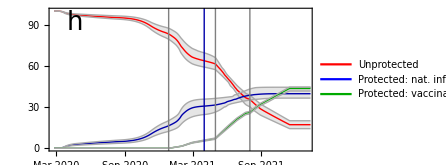

Date
Unprotected
 Protected through natural infection
 Protected through vaccination

({2020,2,25} | {2020,2,26} | {2020,2,27} | {2020,2,28} | {2020,2,29} | {2020,3,1} | {2020,3,2} | {2020,3,3} | {2020,3,4} | {2020,3,5} | {2020,3,6} | {2020,3,7} | {2020,3,8} | {2020,3,9} | {2020,3,10} | {2020,3,11} | {2020,3,12} | {2020,3,13} | {2020,3,14} | {2020,3,15} | {2020,3,16} | {2020,3,17} | {2020,3,18} | {2020,3,19} | {2020,3,20} | {2020,3,21} | {2020,3,22} | {2020,3,23} | {2020,3,24} | {2020,3,25} | {2020,3,26} | {2020,3,27} | {2020,3,28} | {2020,3,29} | {2020,3,30} | {2020,3,31} | {2020,4,1} | {2020,4,2} | {2020,4,3} | {2020,4,4} | {2020,4,5} | {2020,4,6} | {2020,4,7} | {2020,4,8} | {2020,4,9} | {2020,4,10} | {2020,4,11} | {2020,4,12} | {2020,4,13} | {2020,4,14} | {2020,4,15} | {2020,4,16} | {2020,4,17} | {2020,4,18} | {2020,4,19} | {2020,4,20} | {2020,4,21} | {2020,4,22} | {2020,4,23} | {2020,4,24} | {2020,4,25} | {2020,4,26} | {2020,4,27} | {2020,4,28} | {2020,4,29} | {2020,4,30} | {2020,5,1} | {2020,5,2} | {2020,5,3} | {2020,5,4} | {2020,5,5} | {2020,5,6} | {2020,5,7} | {2020,5,8} | {2020,5,9} | {2020,5,10} | {2020,5,11} | {2020,5,12} | {2020,5,13} | {2020,5,14} | {2020,5,15} | {2020,5,16} | {2020,5,17} | {2020,5,18} | {2020,5,19} | {2020,5,20} | {2020,5,21} | {2020,5,22} | {2020,5,23} | {2020,5,24} | {2020,5,25} | {2020,5,26} | {2020,5,27} | {2020,5,28} | {2020,5,29} | {2020,5,30} | {2020,5,31} | {2020,6,1} | {2020,6,2} | {2020,6,3} | {2020,6,4} | {2020,6,5} | {2020,6,6} | {2020,6,7} | {2020,6,8} | {2020,6,9} | {2020,6,10} | {2020,6,11} | {2020,6,12} | {2020,6,13} | {2020,6,14} | {2020,6,15} | {2020,6,16} | {2020,6,17} | {2020,6,18} | {2020,6,19} | {2020,6,20} | {2020,6,21} | {2020,6,22} | {2020,6,23} | {2020,6,24} | {2020,6,25} | {2020,6,26} | {2020,6,27} | {2020,6,28} | {2020,6,29} | {2020,6,30} | {2020,7,1} | {2020,7,2} | {2020,7,3} | {2020,7,4} | {2020,7,5} | {2020,7,6} | {2020,7,7} | {2020,7,8} | {2020,7,9} | {2020,7,10} | {2020,7,11} | {2020,7,12} | {2020,7,13} | {2020,7,14} | {2020,7,15} | {2020,7,16} | {2020,7,17} | {2020,7,18} | {2020,7,19} | {2020,7,20} | {2020,7,21} | {2020,7,22} | {2020,7,23} | {2020,7,24} | {2020,7,25} | {2020,7,26} | {2020,7,27} | {2020,7,28} | {2020,7,29} | {2020,7,30} | {2020,7,31} | {2020,8,1} | {2020,8,2} | {2020,8,3} | {2020,8,4} | {2020,8,5} | {2020,8,6} | {2020,8,7} | {2020,8,8} | {2020,8,9} | {2020,8,10} | {2020,8,11} | {2020,8,12} | {2020,8,13} | {2020,8,14} | {2020,8,15} | {2020,8,16} | {2020,8,17} | {2020,8,18} | {2020,8,19} | {2020,8,20} | {2020,8,21} | {2020,8,22} | {2020,8,23} | {2020,8,24} | {2020,8,25} | {2020,8,26} | {2020,8,27} | {2020,8,28} | {2020,8,29} | {2020,8,30} | {2020,8,31} | {2020,9,1} | {2020,9,2} | {2020,9,3} | {2020,9,4} | {2020,9,5} | {2020,9,6} | {2020,9,7} | {2020,9,8} | {2020,9,9} | {2020,9,10} | {2020,9,11} | {2020,9,12} | {2020,9,13} | {2020,9,14} | {2020,9,15} | {2020,9,16} | {2020,9,17} | {2020,9,18} | {2020,9,19} | {2020,9,20} | {2020,9,21} | {2020,9,22} | {2020,9,23} | {2020,9,24} | {2020,9,25} | {2020,9,26} | {2020,9,27} | {2020,9,28} | {2020,9,29} | {2020,9,30} | {2020,10,1} | {2020,10,2} | {2020,10,3} | {2020,10,4} | {2020,10,5} | {2020,10,6} | {2020,10,7} | {2020,10,8} | {2020,10,9} | {2020,10,10} | {2020,10,11} | {2020,10,12} | {2020,10,13} | {2020,10,14} | {2020,10,15} | {2020,10,16} | {2020,10,17} | {2020,10,18} | {2020,10,19} | {2020,10,20} | {2020,10,21} | {2020,10,22} | {2020,10,23} | {2020,10,24} | {2020,10,25} | {2020,10,26} | {2020,10,27} | {2020,10,28} | {2020,10,29} | {2020,10,30} | {2020,10,31} | {2020,11,1} | {2020,11,2} | {2020,11,3} | {2020,11,4} | {2020,11,5} | {2020,11,6} | {2020,11,7} | {2020,11,8} | {2020,11,9} | {2020,11,10} | {2020,11,11} | {2020,11,12} | {2020,11,13} | {2020,11,14} | {2020,11,15} | {2020,11,16} | {2020,11,17} | {2020,11,18} | {2020,11,19} | {2020,11,20} | {2020,11,21} | {2020,11,22} | {2020,11,23} | {2020,11,24} | {2020,11,25} | {2020,11,26} | {2020,11,27} | {2020,11,28} | {2020,11,29} | {2020,11,30} | {2020,12,1} | {2020,12,2} | {2020,12,3} | {2020,12,4} | {2020,12,5} | {2020,12,6} | {2020,12,7} | {2020,12,8} | {2020,12,9} | {2020,12,10} | {2020,12,11} | {2020,12,12} | {2020,12,13} | {2020,12,14} | {2020,12,15} | {2020,12,16} | {2020,12,17} | {2020,12,18} | {2020,12,19} | {2020,12,20} | {2020,12,21} | {2020,12,22} | {2020,12,23} | {2020,12,24} | {2020,12,25} | {2020,12,26} | {2020,12,27} | {2020,12,28} | {2020,12,29} | {2020,12,30} | {2020,12,31} | {2021,1,1} | {2021,1,2} | {2021,1,3} | {2021,1,4} | {2021,1,5} | {2021,1,6} | {2021,1,7} | {2021,1,8} | {2021,1,9} | {2021,1,10} | {2021,1,11} | {2021,1,12} | {2021,1,13} | {2021,1,14} | {2021,1,15} | {2021,1,16} | {2021,1,17} | {2021,1,18} | {2021,1,19} | {2021,1,20} | {2021,1,21} | {2021,1,22} | {2021,1,23} | {2021,1,24} | {2021,1,25} | {2021,1,26} | {2021,1,27} | {2021,1,28} | {2021,1,29} | {2021,1,30} | {2021,1,31} | {2021,2,1} | {2021,2,2} | {2021,2,3} | {2021,2,4} | {2021,2,5} | {2021,2,6} | {2021,2,7} | {2021,2,8} | {2021,2,9} | {2021,2,10} | {2021,2,11} | {2021,2,12} | {2021,2,13} | {2021,2,14} | {2021,2,15} | {2021,2,16} | {2021,2,17} | {2021,2,18} | {2021,2,19} | {2021,2,20} | {2021,2,21} | {2021,2,22} | {2021,2,23} | {2021,2,24} | {2021,2,25} | {2021,2,26} | {2021,2,27} | {2021,2,28} | {2021,3,1} | {2021,3,2} | {2021,3,3} | {2021,3,4} | {2021,3,5} | {2021,3,6} | {2021,3,7} | {2021,3,8} | {2021,3,9} | {2021,3,10} | {2021,3,11} | {2021,3,12} | {2021,3,13} | {2021,3,14} | {2021,3,15} | {2021,3,16} | {2021,3,17} | {2021,3,18} | {2021,3,19} | {2021,3,20} | {2021,3,21} | {2021,3,22} | {2021,3,23} | {2021,3,24} | {2021,3,25} | {2021,3,26} | {2021,3,27} | {2021,3,28} | {2021,3,29} | {2021,3,30} | {2021,3,31} | {2021,4,1} | {2021,4,2} | {2021,4,3} | {2021,4,4} | {2021,4,5} | {2021,4,6} | {2021,4,7} | {2021,4,8} | {2021,4,9} | {2021,4,10} | {2021,4,11} | {2021,4,12} | {2021,4,13} | {2021,4,14} | {2021,4,15} | {2021,4,16} | {2021,4,17} | {2021,4,18} | {2021,4,19} | {2021,4,20} | {2021,4,21} | {2021,4,22} | {2021,4,23} | {2021,4,24} | {2021,4,25} | {2021,4,26} | {2021,4,27} | {2021,4,28} | {2021,4,29} | {2021,4,30} | {2021,5,1} | {2021,5,2} | {2021,5,3} | {2021,5,4} | {2021,5,5} | {2021,5,6} | {2021,5,7} | {2021,5,8} | {2021,5,9} | {2021,5,10} | {2021,5,11} | {2021,5,12} | {2021,5,13} | {2021,5,14} | {2021,5,15} | {2021,5,16} | {2021,5,17} | {2021,5,18} | {2021,5,19} | {2021,5,20} | {2021,5,21} | {2021,5,22} | {2021,5,23} | {2021,5,24} | {2021,5,25} | {2021,5,26} | {2021,5,27} | {2021,5,28} | {2021,5,29} | {2021,5,30} | {2021,5,31} | {2021,6,1} | {2021,6,2} | {2021,6,3} | {2021,6,4} | {2021,6,5} | {2021,6,6} | {2021,6,7} | {2021,6,8} | {2021,6,9} | {2021,6,10} | {2021,6,11} | {2021,6,12} | {2021,6,13} | {2021,6,14} | {2021,6,15} | {2021,6,16} | {2021,6,17} | {2021,6,18} | {2021,6,19} | {2021,6,20} | {2021,6,21} | {2021,6,22} | {2021,6,23} | {2021,6,24} | {2021,6,25} | {2021,6,26} | {2021,6,27} | {2021,6,28} | {2021,6,29} | {2021,6,30} | {2021,7,1} | {2021,7,2} | {2021,7,3} | {2021,7,4} | {2021,7,5} | {2021,7,6} | {2021,7,7} | {2021,7,8} | {2021,7,9} | {2021,7,10} | {2021,7,11} | {2021,7,12} | {2021,7,13} | {2021,7,14} | {2021,7,15} | {2021,7,16} | {2021,7,17} | {2021,7,18} | {2021,7,19} | {2021,7,20} | {2021,7,21} | {2021,7,22} | {2021,7,23} | {2021,7,24} | {2021,7,25} | {2021,7,26} | {2021,7,27} | {2021,7,28} | {2021,7,29} | {2021,7,30} | {2021,7,31} | {2021,8,1} | {2021,8,2} | {2021,8,3} | {2021,8,4} | {2021,8,5} | {2021,8,6} | {2021,8,7} | {2021,8,8} | {2021,8,9} | {2021,8,10} | {2021,8,11} | {2021,8,12} | {2021,8,13} | {2021,8,14} | {2021,8,15} | {2021,8,16} | {2021,8,17} | {2021,8,18} | {2021,8,19} | {2021,8,20} | {2021,8,21} | {2021,8,22} | {2021,8,23} | {2021,8,24} | {2021,8,25} | {2021,8,26} | {2021,8,27} | {2021,8,28} | {2021,8,29} | {2021,8,30} | {2021,8,31} | {2021,9,1} | {2021,9,2} | {2021,9,3} | {2021,9,4} | {2021,9,5} | {2021,9,6} | {2021,9,7} | {2021,9,8} | {2021,9,9} | {2021,9,10} | {2021,9,11} | {2021,9,12} | {2021,9,13} | {2021,9,14} | {2021,9,15} | {2021,9,16} | {2021,9,17} | {2021,9,18} | {2021,9,19} | {2021,9,20} | {2021,9,21} | {2021,9,22} | {2021,9,23} | {2021,9,24} | {2021,9,25} | {2021,9,26} | {2021,9,27} | {2021,9,28} | {2021,9,29} | {2021,9,30} | {2021,10,1} | {2021,10,2} | {2021,10,3} | {2021,10,4} | {2021,10,5} | {2021,10,6} | {2021,10,7} | {2021,10,8} | {2021,10,9} | {2021,10,10} | {2021,10,11} | {2021,10,12} | {2021,10,13} | {2021,10,14} | {2021,10,15} | {2021,10,16} | {2021,10,17} | {2021,10,18} | {2021,10,19} | {2021,10,20} | {2021,10,21} | {2021,10,22} | {2021,10,23} | {2021,10,24} | {2021,10,25} | {2021,10,26} | {2021,10,27} | {2021,10,28} | {2021,10,29} | {2021,10,30} | {2021,10,31} | {2021,11,1} | {2021,11,2} | {2021,11,3} | {2021,11,4} | {2021,11,5} | {2021,11,6} | {2021,11,7} | {2021,11,8} | {2021,11,9} | {2021,11,10} | {2021,11,11} | {2021,11,12} | {2021,11,13} | {2021,11,14} | {2021,11,15} | {2021,11,16} | {2021,11,17} | {2021,11,18} | {2021,11,19} | {2021,11,20} | {2021,11,21} | {2021,11,22} | {2021,11,23} | {2021,11,24} | {2021,11,25} | {2021,11,26} | {2021,11,27} | {2021,11,28} | {2021,11,29} | {2021,11,30} | {2021,12,1} | {2021,12,2} | {2021,12,3} | {2021,12,4} | {2021,12,5} | {2021,12,6} | {2021,12,7} | {2021,12,8} | {2021,12,9} | {2021,12,10} | {2021,12,11} | {2021,12,12} | {2021,12,13} | {2021,12,14} | {2021,12,15} | {2021,12,16} | {2021,12,17} | {2021,12,18} | {2021,12,19} | {2021,12,20} | {2021,12,21} | {2021,12,22} | {2021,12,23} | {2021,12,24} | {2021,12,25} | {2021,12,26} | {2021,12,27} | {2021,12,28} | {2021,12,29} | {2021,12,30} | {2021,12,31} | {2022,1,1} | {2022,1,2} | {2022,1,3} | {2022,1,4} | {2022,1,5} | {2022,1,6} | {2022,1,7} | {2022,1,8} | {2022,1,9} | {2022,1,10}
99.988 | 99.9845 | 99.9806 | 99.9761 | 99.971 | 99.9648 | 99.9577 | 99.9494 | 99.9396 | 99.9282 | 99.9151 | 99.8998 | 99.8823 | 99.8619 | 99.8388 | 99.8123 | 99.7808 | 99.7449 | 99.7029 | 99.6516 | 99.5939 | 99.5277 | 99.4501 | 99.3587 | 99.2606 | 99.1516 | 99.0313 | 98.9034 | 98.7778 | 98.6517 | 98.5353 | 98.4375 | 98.3478 | 98.2637 | 98.1846 | 98.1112 | 98.042 | 97.9759 | 97.9126 | 97.8522 | 97.7945 | 97.7395 | 97.6871 | 97.6388 | 97.5933 | 97.55 | 97.509 | 97.4701 | 97.4332 | 97.3981 | 97.3649 | 97.3333 | 97.3034 | 97.2751 | 97.2481 | 97.2226 | 97.1984 | 97.1755 | 97.1538 | 97.133 | 97.1132 | 97.094 | 97.0748 | 97.0546 | 97.0328 | 97.0105 | 96.9883 | 96.9664 | 96.9446 | 96.9229 | 96.9014 | 96.8799 | 96.8585 | 96.8372 | 96.8159 | 96.7947 | 96.7736 | 96.7525 | 96.7315 | 96.7105 | 96.6897 | 96.6689 | 96.6481 | 96.6275 | 96.6071 | 96.5869 | 96.5667 | 96.5466 | 96.5266 | 96.5067 | 96.4868 | 96.4671 | 96.4474 | 96.4278 | 96.4082 | 96.3888 | 96.3694 | 96.3501 | 96.3309 | 96.3118 | 96.2928 | 96.2738 | 96.2549 | 96.2361 | 96.2174 | 96.1988 | 96.1802 | 96.1618 | 96.1434 | 96.1251 | 96.1069 | 96.0888 | 96.0707 | 96.0528 | 96.0349 | 96.0171 | 95.9994 | 95.9818 | 95.9643 | 95.9468 | 95.9295 | 95.9122 | 95.895 | 95.8779 | 95.8609 | 95.8439 | 95.8271 | 95.8103 | 95.7936 | 95.777 | 95.7605 | 95.7441 | 95.7278 | 95.7115 | 95.6954 | 95.6793 | 95.6633 | 95.6474 | 95.6315 | 95.6158 | 95.6002 | 95.5846 | 95.5691 | 95.5537 | 95.5384 | 95.5232 | 95.508 | 95.493 | 95.478 | 95.4631 | 95.4483 | 95.4336 | 95.4189 | 95.4044 | 95.3899 | 95.3755 | 95.3612 | 95.347 | 95.3329 | 95.3188 | 95.3049 | 95.291 | 95.2772 | 95.2634 | 95.2498 | 95.2362 | 95.2227 | 95.2093 | 95.196 | 95.1827 | 95.1695 | 95.1563 | 95.1432 | 95.13 | 95.1168 | 95.1034 | 95.0898 | 95.0759 | 95.0615 | 95.0466 | 95.0311 | 95.015 | 94.9982 | 94.9807 | 94.9626 | 94.9438 | 94.9243 | 94.9041 | 94.8831 | 94.8615 | 94.839 | 94.8158 | 94.7917 | 94.7667 | 94.7409 | 94.7141 | 94.6864 | 94.6577 | 94.628 | 94.5973 | 94.5654 | 94.5325 | 94.4983 | 94.463 | 94.4265 | 94.3886 | 94.3495 | 94.309 | 94.2671 | 94.2237 | 94.1789 | 94.1325 | 94.0845 | 94.0349 | 93.9836 | 93.9306 | 93.8758 | 93.8191 | 93.7606 | 93.7 | 93.6375 | 93.5729 | 93.5062 | 93.4373 | 93.3662 | 93.2927 | 93.2169 | 93.1386 | 93.0579 | 92.9746 | 92.8887 | 92.8001 | 92.7087 | 92.6145 | 92.5174 | 92.4174 | 92.3144 | 92.2082 | 92.099 | 91.9865 | 91.8707 | 91.7516 | 91.629 | 91.503 | 91.3735 | 91.2404 | 91.1037 | 90.9633 | 90.8192 | 90.6713 | 90.5197 | 90.3644 | 90.2053 | 90.0427 | 89.8766 | 89.7077 | 89.5364 | 89.3635 | 89.1903 | 89.0179 | 88.8476 | 88.6801 | 88.5155 | 88.3539 | 88.1952 | 88.0392 | 87.8858 | 87.7351 | 87.587 | 87.4413 | 87.298 | 87.1572 | 87.0188 | 86.8827 | 86.749 | 86.6176 | 86.4886 | 86.3619 | 86.2375 | 86.1154 | 85.9956 | 85.878 | 85.7627 | 85.6495 | 85.5386 | 85.4298 | 85.3232 | 85.2187 | 85.1163 | 85.016 | 84.9177 | 84.8215 | 84.7273 | 84.6348 | 84.5441 | 84.4545 | 84.3644 | 84.2702 | 84.1681 | 84.0592 | 83.947 | 83.833 | 83.7171 | 83.5992 | 83.479 | 83.3567 | 83.232 | 83.0805 | 82.9266 | 82.7705 | 82.6121 | 82.4513 | 82.2673 | 82.0811 | 81.8927 | 81.7021 | 81.5092 | 81.3141 | 81.1167 | 80.9174 | 80.7153 | 80.5094 | 80.2983 | 80.0711 | 79.8305 | 79.5774 | 79.3096 | 79.0256 | 78.724 | 78.4038 | 78.0645 | 77.7064 | 77.3304 | 76.9385 | 76.5224 | 76.0921 | 75.6551 | 75.2407 | 74.772 | 74.376 | 74.0161 | 73.6905 | 73.3842 | 73.0435 | 72.7183 | 72.3962 | 72.0442 | 71.7042 | 71.3756 | 71.0581 | 70.7511 | 70.4499 | 70.1541 | 69.8723 | 69.5996 | 69.3355 | 69.0798 | 68.8321 | 68.5922 | 68.3597 | 68.1343 | 67.9157 | 67.7036 | 67.4979 | 67.2981 | 67.104 | 66.9163 | 66.7471 | 66.5823 | 66.4219 | 66.3038 | 66.1894 | 66.0787 | 65.9713 | 65.867 | 65.7659 | 65.6676 | 65.572 | 65.479 | 65.3885 | 65.3003 | 65.2143 | 65.1304 | 65.0485 | 64.9684 | 64.8865 | 64.8053 | 64.7258 | 64.6481 | 64.5721 | 64.4976 | 64.4246 | 64.353 | 64.2826 | 64.2135 | 64.1455 | 64.0784 | 64.0122 | 63.9464 | 63.8809 | 63.8148 | 63.7477 | 63.6791 | 63.609 | 63.5376 | 63.4654 | 63.3923 | 63.322 | 63.2542 | 63.1858 | 63.1168 | 63.047 | 62.9766 | 62.9054 | 62.8334 | 62.7607 | 62.6871 | 62.6127 | 62.5374 | 62.4613 | 62.3842 | 62.3063 | 62.2273 | 62.1462 | 62.06 | 61.9719 | 61.8825 | 61.7918 | 61.6998 | 61.6065 | 61.5118 | 61.463 | 61.1588 | 60.8533 | 60.5466 | 60.2387 | 59.9296 | 59.6192 | 59.3076 | 59.0097 | 58.7161 | 58.4218 | 58.1266 | 57.8305 | 57.5337 | 57.2303 | 56.905 | 56.5784 | 56.2506 | 55.9216 | 55.5847 | 55.2429 | 54.9 | 54.5322 | 54.0926 | 53.69 | 53.3365 | 53.0321 | 52.7348 | 52.4334 | 52.1307 | 51.8061 | 51.476 | 51.1482 | 50.8203 | 50.5083 | 50.2082 | 49.908 | 49.5764 | 49.2758 | 49.0001 | 48.7057 | 48.3753 | 48.0332 | 47.6788 | 47.3244 | 46.9761 | 46.6159 | 46.2575 | 45.89 | 45.5309 | 45.1706 | 44.7834 | 44.3976 | 44.0649 | 43.7729 | 43.4485 | 43.1002 | 42.7528 | 42.4065 | 42.1119 | 41.8745 | 41.6461 | 41.418 | 41.1577 | 40.894 | 40.6312 | 40.3692 | 40.1081 | 39.8479 | 39.5865 | 39.323 | 39.0659 | 38.8152 | 38.5778 | 38.3414 | 38.1059 | 37.8714 | 37.6379 | 37.4054 | 37.1739 | 36.9784 | 36.8053 | 36.6235 | 36.498 | 36.3907 | 36.2842 | 36.1786 | 36.0738 | 35.9646 | 35.8549 | 35.7466 | 35.6396 | 35.5865 | 35.33 | 35.075 | 34.8214 | 34.5692 | 34.3096 | 34.0484 | 33.79 | 33.5352 | 33.2818 | 33.0299 | 32.7794 | 32.5303 | 32.2827 | 32.0365 | 31.7917 | 31.5482 | 31.3106 | 31.075 | 30.841 | 30.6084 | 30.3747 | 30.139 | 29.9047 | 29.6717 | 29.4401 | 29.2098 | 28.9808 | 28.7554 | 28.5891 | 28.4239 | 28.2597 | 28.0965 | 27.9342 | 27.7728 | 27.6123 | 27.4526 | 27.2937 | 27.1356 | 26.9781 | 26.8214 | 26.6671 | 26.5149 | 26.3631 | 26.2118 | 26.0609 | 25.9103 | 25.7601 | 25.6103 | 25.4608 | 25.3116 | 25.1627 | 25.014 | 24.8656 | 24.7174 | 24.5695 | 24.4204 | 24.2692 | 24.1182 | 23.9673 | 23.8167 | 23.6661 | 23.5185 | 23.3717 | 23.225 | 23.0784 | 22.9319 | 22.7855 | 22.6393 | 22.4931 | 22.347 | 22.2009 | 22.0549 | 21.909 | 21.7632 | 21.6174 | 21.4717 | 21.326 | 21.1804 | 21.0348 | 20.8892 | 20.7437 | 20.5982 | 20.4527 | 20.3073 | 20.1619 | 20.0165 | 19.8711 | 19.7272 | 19.5878 | 19.4485 | 19.3091 | 19.1698 | 19.0305 | 18.8912 | 18.7519 | 18.6126 | 18.4693 | 18.3252 | 18.1812 | 18.0371 | 17.8931 | 17.7491 | 17.6051 | 17.4611 | 17.3171 | 17.1731 | 17.1495 | 17.1494 | 17.1494 | 17.1494 | 17.1493 | 17.1493 | 17.1492 | 17.1492 | 17.1492 | 17.1491 | 17.1491 | 17.1491 | 17.1491 | 17.1491 | 17.149 | 17.149 | 17.149 | 17.149 | 17.149 | 17.149 | 17.149 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1489 | 17.1488 | 17.1488 | 17.1488 | 17.1488 | 17.1488 | 17.1488 | 17.1488 | 17.1488 | 17.1488 | 17.1488 | 17.1488 | 17.1488 | 17.1488 | 17.1488 | 17.1488 | 17.1488 | 17.1488
99.9826 | 99.9778 | 99.9723 | 99.9661 | 99.9589 | 99.9507 | 99.9412 | 99.9303 | 99.9177 | 99.9033 | 99.8866 | 99.8674 | 99.8453 | 99.8198 | 99.7904 | 99.7566 | 99.7137 | 99.6612 | 99.6015 | 99.5383 | 99.4652 | 99.3742 | 99.2697 | 99.1508 | 99.0323 | 98.8936 | 98.7243 | 98.5604 | 98.4082 | 98.2646 | 98.1332 | 98.0325 | 97.9453 | 97.8602 | 97.7777 | 97.6982 | 97.6219 | 97.5415 | 97.4582 | 97.3792 | 97.3041 | 97.2327 | 97.165 | 97.1006 | 97.0393 | 96.9812 | 96.9302 | 96.8849 | 96.842 | 96.8014 | 96.7629 | 96.7265 | 96.692 | 96.6594 | 96.6285 | 96.5993 | 96.5716 | 96.5455 | 96.5207 | 96.4972 | 96.4748 | 96.453 | 96.4304 | 96.4056 | 96.3794 | 96.3531 | 96.327 | 96.3012 | 96.2755 | 96.25 | 96.2245 | 96.1991 | 96.1738 | 96.1486 | 96.1234 | 96.0983 | 96.0733 | 96.0483 | 96.0233 | 95.9985 | 95.9737 | 95.9489 | 95.9242 | 95.8996 | 95.8751 | 95.8506 | 95.8262 | 95.8018 | 95.7775 | 95.7533 | 95.7291 | 95.705 | 95.681 | 95.6571 | 95.6332 | 95.6094 | 95.5857 | 95.562 | 95.5384 | 95.5149 | 95.4914 | 95.4681 | 95.4448 | 95.4216 | 95.3984 | 95.3754 | 95.3524 | 95.3295 | 95.3067 | 95.2839 | 95.2613 | 95.2387 | 95.2162 | 95.1938 | 95.1714 | 95.1492 | 95.127 | 95.1049 | 95.0829 | 95.061 | 95.0392 | 95.0174 | 94.9958 | 94.9742 | 94.9527 | 94.9313 | 94.91 | 94.8888 | 94.8677 | 94.8466 | 94.8257 | 94.8048 | 94.7841 | 94.7634 | 94.7428 | 94.7223 | 94.7019 | 94.6816 | 94.6613 | 94.6412 | 94.6212 | 94.6012 | 94.5814 | 94.5616 | 94.5419 | 94.5224 | 94.5029 | 94.4835 | 94.4642 | 94.445 | 94.4259 | 94.4069 | 94.388 | 94.3692 | 94.3504 | 94.3318 | 94.3133 | 94.2948 | 94.2765 | 94.2582 | 94.2401 | 94.222 | 94.204 | 94.1862 | 94.1684 | 94.1507 | 94.1331 | 94.1156 | 94.0982 | 94.081 | 94.0637 | 94.0466 | 94.0296 | 94.0127 | 93.9958 | 93.9791 | 93.9623 | 93.9455 | 93.9285 | 93.911 | 93.8927 | 93.8734 | 93.8529 | 93.8315 | 93.8091 | 93.7859 | 93.7619 | 93.737 | 93.7112 | 93.6846 | 93.6569 | 93.6283 | 93.5987 | 93.568 | 93.5361 | 93.5032 | 93.4691 | 93.4337 | 93.3971 | 93.3591 | 93.3199 | 93.2792 | 93.2371 | 93.1935 | 93.1484 | 93.1017 | 93.0533 | 93.0033 | 92.9516 | 92.898 | 92.8426 | 92.7853 | 92.726 | 92.6648 | 92.6014 | 92.5359 | 92.4682 | 92.3982 | 92.3259 | 92.2512 | 92.174 | 92.0943 | 92.012 | 91.927 | 91.8393 | 91.7487 | 91.6553 | 91.559 | 91.4596 | 91.3571 | 91.2515 | 91.1426 | 91.0304 | 90.9148 | 90.7958 | 90.6733 | 90.5472 | 90.4174 | 90.2838 | 90.1464 | 90.0052 | 89.86 | 89.7109 | 89.5577 | 89.4005 | 89.2391 | 89.0736 | 88.9039 | 88.7299 | 88.5516 | 88.369 | 88.182 | 87.9905 | 87.7945 | 87.5942 | 87.3894 | 87.1803 | 86.9672 | 86.7509 | 86.5336 | 86.3194 | 86.113 | 85.9149 | 85.7221 | 85.5322 | 85.3446 | 85.1591 | 84.9759 | 84.795 | 84.6165 | 84.4405 | 84.2671 | 84.0963 | 83.9281 | 83.7625 | 83.5995 | 83.4392 | 83.2815 | 83.1265 | 82.974 | 82.8243 | 82.6771 | 82.5326 | 82.3906 | 82.2513 | 82.1145 | 81.9803 | 81.8487 | 81.7195 | 81.5929 | 81.4687 | 81.347 | 81.2279 | 81.1114 | 80.9973 | 80.8849 | 80.7738 | 80.6583 | 80.5308 | 80.3953 | 80.2582 | 80.12 | 79.9801 | 79.8383 | 79.6944 | 79.5485 | 79.4003 | 79.2265 | 79.0507 | 78.8728 | 78.693 | 78.5111 | 78.3071 | 78.1012 | 77.8935 | 77.6839 | 77.4726 | 77.2594 | 77.0441 | 76.8271 | 76.6076 | 76.3839 | 76.1547 | 75.9182 | 75.673 | 75.4154 | 75.1419 | 74.8498 | 74.5371 | 74.2032 | 73.8482 | 73.472 | 73.0753 | 72.6609 | 72.232 | 71.6858 | 71.1004 | 70.5184 | 69.9722 | 69.4947 | 69.0754 | 68.6934 | 68.3295 | 67.9309 | 67.5463 | 67.1759 | 66.8196 | 66.4773 | 66.1484 | 65.8327 | 65.5296 | 65.2386 | 64.9592 | 64.6908 | 64.4329 | 64.185 | 63.9467 | 63.7175 | 63.4968 | 63.2843 | 63.0796 | 62.8822 | 62.6918 | 62.5079 | 62.3303 | 62.1586 | 61.9924 | 61.8315 | 61.6756 | 61.5244 | 61.4122 | 61.3041 | 61.1999 | 61.0993 | 61.0021 | 60.9082 | 60.8173 | 60.7293 | 60.6439 | 60.5611 | 60.4807 | 60.4026 | 60.3265 | 60.2524 | 60.1802 | 60.1098 | 60.041 | 59.9738 | 59.908 | 59.8436 | 59.7805 | 59.7186 | 59.6578 | 59.5981 | 59.5394 | 59.4816 | 59.4248 | 59.3688 | 59.3136 | 59.2589 | 59.2043 | 59.1485 | 59.0908 | 59.0321 | 58.9729 | 58.9135 | 58.854 | 58.7943 | 58.7343 | 58.6741 | 58.6135 | 58.5527 | 58.4915 | 58.43 | 58.3682 | 58.306 | 58.2435 | 58.1807 | 58.1175 | 58.054 | 57.9901 | 57.9259 | 57.8613 | 57.7963 | 57.7309 | 57.6652 | 57.5991 | 57.5326 | 57.4657 | 57.3985 | 57.3308 | 57.306 | 57.05 | 56.7937 | 56.5372 | 56.2804 | 56.0234 | 55.7662 | 55.5087 | 55.2511 | 54.9932 | 54.7352 | 54.4769 | 54.2186 | 53.96 | 53.7013 | 53.4425 | 53.1836 | 52.9245 | 52.6654 | 52.4061 | 52.1468 | 51.881 | 51.6021 | 51.323 | 51.0437 | 50.7643 | 50.4847 | 50.205 | 49.9252 | 49.6452 | 49.3653 | 49.0852 | 48.8052 | 48.5251 | 48.2451 | 47.9046 | 47.4042 | 46.9068 | 46.4127 | 45.9222 | 45.4355 | 45.1704 | 44.9112 | 44.6522 | 44.3933 | 44.1345 | 43.8759 | 43.6174 | 43.3591 | 42.9723 | 42.5745 | 42.1807 | 41.7908 | 41.405 | 41.0233 | 40.6122 | 40.1872 | 39.7656 | 39.3473 | 38.9565 | 38.588 | 38.2231 | 37.8618 | 37.5043 | 37.1506 | 36.8008 | 36.4549 | 36.1131 | 35.7753 | 35.4415 | 35.1119 | 34.7863 | 34.4649 | 34.1477 | 33.8346 | 33.5255 | 33.2206 | 32.9198 | 32.623 | 32.3302 | 32.075 | 31.8463 | 31.6213 | 31.4513 | 31.3002 | 31.1523 | 31.0076 | 30.8659 | 30.7273 | 30.5916 | 30.4589 | 30.3291 | 30.2482 | 29.9761 | 29.7076 | 29.4425 | 29.1807 | 28.9222 | 28.6669 | 28.4147 | 28.1656 | 27.9194 | 27.7048 | 27.499 | 27.2947 | 27.092 | 26.8907 | 26.6907 | 26.4921 | 26.2947 | 26.0984 | 25.9033 | 25.7092 | 25.5161 | 25.324 | 25.1327 | 24.9423 | 24.7527 | 24.5639 | 24.3757 | 24.1904 | 24.0566 | 23.9233 | 23.7906 | 23.6584 | 23.5266 | 23.3953 | 23.2644 | 23.1338 | 23.0036 | 22.8738 | 22.7442 | 22.615 | 22.486 | 22.3572 | 22.2287 | 22.1004 | 21.9723 | 21.8444 | 21.7167 | 21.5891 | 21.4617 | 21.3345 | 21.2073 | 21.0803 | 20.9534 | 20.8266 | 20.6999 | 20.5733 | 20.4467 | 20.3203 | 20.1939 | 20.0676 | 19.9413 | 19.8151 | 19.6889 | 19.5628 | 19.4368 | 19.3107 | 19.1847 | 19.0588 | 18.9328 | 18.8069 | 18.6811 | 18.5552 | 18.4294 | 18.3036 | 18.1778 | 18.052 | 17.9263 | 17.8005 | 17.6748 | 17.5491 | 17.4234 | 17.2977 | 17.172 | 17.0463 | 16.9206 | 16.795 | 16.6693 | 16.5436 | 16.418 | 16.2924 | 16.1667 | 16.0411 | 15.9154 | 15.7898 | 15.6642 | 15.5386 | 15.4129 | 15.2873 | 15.1617 | 15.0361 | 14.9105 | 14.7849 | 14.6592 | 14.5336 | 14.408 | 14.2824 | 14.2619 | 14.2619 | 14.2619 | 14.2619 | 14.2619 | 14.2619 | 14.2619 | 14.2619 | 14.2619 | 14.2619 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618 | 14.2618
99.9924 | 99.9899 | 99.9871 | 99.9839 | 99.9802 | 99.9759 | 99.9709 | 99.9651 | 99.9582 | 99.9502 | 99.9408 | 99.9298 | 99.917 | 99.902 | 99.8844 | 99.8638 | 99.8409 | 99.8146 | 99.7834 | 99.7471 | 99.7049 | 99.6559 | 99.5991 | 99.5338 | 99.4601 | 99.3754 | 99.2797 | 99.1802 | 99.0805 | 98.9869 | 98.9021 | 98.8277 | 98.7614 | 98.701 | 98.6444 | 98.5906 | 98.5396 | 98.4909 | 98.4444 | 98.4001 | 98.3578 | 98.3176 | 98.2794 | 98.243 | 98.2083 | 98.1754 | 98.1441 | 98.1144 | 98.0861 | 98.0592 | 98.0337 | 98.0094 | 97.9864 | 97.9645 | 97.9437 | 97.9239 | 97.9051 | 97.8873 | 97.8703 | 97.8542 | 97.8389 | 97.8243 | 97.8105 | 97.7974 | 97.7849 | 97.7713 | 97.7557 | 97.74 | 97.7246 | 97.7093 | 97.6942 | 97.6791 | 97.6641 | 97.6492 | 97.6343 | 97.6194 | 97.6046 | 97.5898 | 97.5751 | 97.5604 | 97.5458 | 97.5311 | 97.5166 | 97.502 | 97.4875 | 97.4731 | 97.4587 | 97.4443 | 97.4299 | 97.4157 | 97.4014 | 97.3872 | 97.373 | 97.3589 | 97.3448 | 97.3307 | 97.3167 | 97.3027 | 97.2888 | 97.2749 | 97.261 | 97.2472 | 97.2334 | 97.2197 | 97.206 | 97.1924 | 97.1788 | 97.1652 | 97.1517 | 97.1383 | 97.1248 | 97.1114 | 97.0981 | 97.0848 | 97.0715 | 97.0583 | 97.0452 | 97.032 | 97.019 | 97.0059 | 96.9929 | 96.98 | 96.9671 | 96.9542 | 96.9414 | 96.9287 | 96.9159 | 96.9033 | 96.8906 | 96.8781 | 96.8655 | 96.853 | 96.8406 | 96.8282 | 96.8158 | 96.8035 | 96.7912 | 96.779 | 96.7669 | 96.7547 | 96.7427 | 96.7306 | 96.7186 | 96.7067 | 96.6948 | 96.683 | 96.6712 | 96.6594 | 96.6477 | 96.636 | 96.6244 | 96.6129 | 96.6013 | 96.5899 | 96.5784 | 96.5671 | 96.5557 | 96.5444 | 96.5332 | 96.522 | 96.5109 | 96.4998 | 96.4887 | 96.4777 | 96.4668 | 96.4559 | 96.445 | 96.4342 | 96.4234 | 96.4127 | 96.402 | 96.3914 | 96.3808 | 96.3703 | 96.3597 | 96.3492 | 96.3386 | 96.3278 | 96.3166 | 96.3048 | 96.2924 | 96.2793 | 96.2657 | 96.2516 | 96.2371 | 96.2221 | 96.2065 | 96.1905 | 96.1739 | 96.1568 | 96.1391 | 96.1208 | 96.1018 | 96.0822 | 96.062 | 96.0411 | 96.0195 | 95.9971 | 95.974 | 95.9502 | 95.9255 | 95.9 | 95.8736 | 95.8464 | 95.8182 | 95.7892 | 95.7591 | 95.7281 | 95.696 | 95.6629 | 95.6287 | 95.5934 | 95.5569 | 95.5192 | 95.4803 | 95.4401 | 95.3987 | 95.3559 | 95.3117 | 95.2661 | 95.219 | 95.1704 | 95.1203 | 95.0686 | 95.0152 | 94.9602 | 94.9035 | 94.845 | 94.7847 | 94.7225 | 94.6584 | 94.5923 | 94.5242 | 94.4541 | 94.3818 | 94.3074 | 94.2307 | 94.1517 | 94.0705 | 93.9868 | 93.9007 | 93.8121 | 93.721 | 93.6272 | 93.5308 | 93.4317 | 93.3299 | 93.2252 | 93.1176 | 93.0072 | 92.8938 | 92.7773 | 92.6578 | 92.5352 | 92.4093 | 92.2805 | 92.1486 | 92.0141 | 91.8782 | 91.7431 | 91.6117 | 91.4851 | 91.3633 | 91.2448 | 91.1286 | 91.0139 | 90.9008 | 90.7891 | 90.6791 | 90.5707 | 90.4639 | 90.3588 | 90.2553 | 90.1534 | 90.0532 | 89.9547 | 89.8578 | 89.7624 | 89.6687 | 89.5766 | 89.4861 | 89.3971 | 89.3096 | 89.2238 | 89.1394 | 89.0565 | 88.9751 | 88.8952 | 88.8168 | 88.7397 | 88.6642 | 88.59 | 88.5172 | 88.4457 | 88.3756 | 88.3069 | 88.2394 | 88.1731 | 88.1036 | 88.0242 | 87.9415 | 87.858 | 87.7735 | 87.6877 | 87.6004 | 87.5115 | 87.421 | 87.3026 | 87.1825 | 87.0608 | 86.9375 | 86.8125 | 86.664 | 86.5138 | 86.362 | 86.2086 | 86.0536 | 85.8969 | 85.7386 | 85.5789 | 85.4178 | 85.2541 | 85.0867 | 84.9144 | 84.7359 | 84.5476 | 84.3456 | 84.1286 | 83.8955 | 83.645 | 83.3759 | 83.0881 | 82.782 | 82.4575 | 82.115 | 81.7567 | 81.3897 | 81.0215 | 80.6642 | 80.323 | 80.0007 | 79.6978 | 79.4084 | 79.0742 | 78.7484 | 78.4302 | 78.1191 | 77.8152 | 77.5182 | 77.2281 | 76.9448 | 76.6683 | 76.3984 | 76.1349 | 75.8776 | 75.6266 | 75.3859 | 75.1534 | 74.9263 | 74.7044 | 74.4877 | 74.2759 | 74.069 | 73.8667 | 73.669 | 73.4756 | 73.2865 | 73.1014 | 72.9203 | 72.743 | 72.6109 | 72.4823 | 72.357 | 72.2349 | 72.1158 | 71.9998 | 71.8865 | 71.776 | 71.6681 | 71.5484 | 71.4213 | 71.2972 | 71.1758 | 71.0573 | 70.9414 | 70.8422 | 70.7489 | 70.6575 | 70.5678 | 70.4799 | 70.3936 | 70.3089 | 70.2257 | 70.144 | 70.0637 | 69.9846 | 69.9069 | 69.8304 | 69.755 | 69.6808 | 69.6074 | 69.5315 | 69.4468 | 69.3587 | 69.2699 | 69.18 | 69.0887 | 68.9957 | 68.9009 | 68.8043 | 68.7056 | 68.6047 | 68.5017 | 68.3964 | 68.2887 | 68.1785 | 68.0658 | 67.9503 | 67.8321 | 67.711 | 67.5869 | 67.4597 | 67.3293 | 67.1956 | 67.0585 | 66.9178 | 66.7735 | 66.6254 | 66.4735 | 66.3175 | 66.1575 | 66.0427 | 65.6573 | 65.2681 | 64.8751 | 64.4783 | 64.0775 | 63.6729 | 63.2644 | 62.852 | 62.4357 | 62.0155 | 61.5914 | 61.1636 | 60.732 | 60.2967 | 59.8577 | 59.4152 | 58.9693 | 58.6101 | 58.3095 | 58.008 | 57.7058 | 57.4028 | 57.0665 | 56.6263 | 56.1844 | 55.741 | 55.2962 | 54.8503 | 54.4312 | 54.0979 | 53.7642 | 53.43 | 53.1207 | 52.8198 | 52.5189 | 52.2178 | 51.9168 | 51.6157 | 51.3147 | 51.0137 | 50.7128 | 50.4121 | 50.1115 | 49.8111 | 49.511 | 49.2111 | 48.9115 | 48.6122 | 48.3133 | 48.0147 | 47.7167 | 47.419 | 47.1218 | 46.8252 | 46.5291 | 46.2336 | 45.9387 | 45.6444 | 45.3753 | 45.1263 | 44.8779 | 44.6302 | 44.3831 | 44.1368 | 43.8912 | 43.6464 | 43.4023 | 43.1591 | 42.9166 | 42.675 | 42.4342 | 42.1943 | 41.9553 | 41.7171 | 41.4799 | 41.2435 | 40.9911 | 40.7274 | 40.4644 | 40.2394 | 40.0403 | 39.8418 | 39.703 | 39.5825 | 39.4627 | 39.3434 | 39.2247 | 39.1067 | 38.9892 | 38.8725 | 38.7564 | 38.7357 | 38.5005 | 38.2658 | 38.0315 | 37.7976 | 37.5641 | 37.3311 | 37.0985 | 36.8663 | 36.6346 | 36.4033 | 36.1725 | 35.942 | 35.712 | 35.4824 | 35.2533 | 35.0245 | 34.7962 | 34.5682 | 34.3407 | 34.1135 | 33.8867 | 33.6603 | 33.4342 | 33.2085 | 32.9831 | 32.7581 | 32.5333 | 32.3114 | 32.1473 | 31.9821 | 31.8176 | 31.6539 | 31.4908 | 31.3283 | 31.1665 | 31.0054 | 30.8448 | 30.6847 | 30.5252 | 30.3662 | 30.2077 | 30.0497 | 29.8921 | 29.735 | 29.5782 | 29.4219 | 29.2659 | 29.1102 | 28.9549 | 28.7999 | 28.6452 | 28.4908 | 28.3366 | 28.181 | 28.0239 | 27.8669 | 27.7099 | 27.553 | 27.3962 | 27.2394 | 27.0827 | 26.926 | 26.7694 | 26.6128 | 26.4563 | 26.2998 | 26.1433 | 25.9869 | 25.8305 | 25.6741 | 25.5178 | 25.3614 | 25.2051 | 25.0488 | 24.8926 | 24.7363 | 24.5801 | 24.4239 | 24.2677 | 24.1115 | 23.9553 | 23.7991 | 23.6429 | 23.4868 | 23.3306 | 23.1745 | 23.0184 | 22.8623 | 22.7061 | 22.55 | 22.3939 | 22.2378 | 22.0817 | 21.9256 | 21.7695 | 21.6134 | 21.4573 | 21.3012 | 21.1451 | 20.9891 | 20.833 | 20.6769 | 20.5208 | 20.3647 | 20.2087 | 20.0526 | 20.0271 | 20.0271 | 20.0271 | 20.0271 | 20.0271 | 20.0271 | 20.0271 | 20.0271 | 20.0271 | 20.0271 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027 | 20.027
0.00209945 | 0.00460646 | 0.00768587 | 0.0112054 | 0.0152887 | 0.0198461 | 0.0252548 | 0.0315603 | 0.0387266 | 0.0470492 | 0.0567179 | 0.0679523 | 0.0812047 | 0.0968596 | 0.114709 | 0.13509 | 0.158389 | 0.185871 | 0.216934 | 0.253534 | 0.297196 | 0.347908 | 0.406682 | 0.474881 | 0.553457 | 0.640614 | 0.736687 | 0.841603 | 0.948818 | 1.06204 | 1.17085 | 1.27069 | 1.36657 | 1.4611 | 1.55033 | 1.63446 | 1.71464 | 1.79217 | 1.86546 | 1.93483 | 2.00053 | 2.06279 | 2.1218 | 2.17774 | 2.23078 | 2.28158 | 2.33084 | 2.3776 | 2.42198 | 2.46411 | 2.50408 | 2.54201 | 2.578 | 2.61215 | 2.64454 | 2.67528 | 2.70443 | 2.73208 | 2.7583 | 2.78318 | 2.80684 | 2.82943 | 2.85122 | 2.87265 | 2.89416 | 2.91586 | 2.93768 | 2.95952 | 2.98135 | 3.00314 | 3.02487 | 3.04655 | 3.06815 | 3.08969 | 3.11117 | 3.13257 | 3.15391 | 3.17519 | 3.1964 | 3.21755 | 3.23848 | 3.25929 | 3.28003 | 3.30068 | 3.32126 | 3.34176 | 3.36219 | 3.38253 | 3.40279 | 3.42298 | 3.44308 | 3.46311 | 3.48306 | 3.50293 | 3.52272 | 3.54242 | 3.56205 | 3.5816 | 3.60106 | 3.62045 | 3.63975 | 3.65897 | 3.67811 | 3.69717 | 3.71615 | 3.73504 | 3.75385 | 3.77258 | 3.79122 | 3.80978 | 3.82826 | 3.84665 | 3.86496 | 3.88319 | 3.90133 | 3.91939 | 3.93737 | 3.95525 | 3.97306 | 3.99078 | 4.00841 | 4.02596 | 4.04343 | 4.06081 | 4.0781 | 4.09531 | 4.11244 | 4.12948 | 4.14643 | 4.1633 | 4.18008 | 4.19678 | 4.21339 | 4.22992 | 4.24636 | 4.26271 | 4.27898 | 4.29517 | 4.31127 | 4.32728 | 4.34321 | 4.35905 | 4.37481 | 4.39048 | 4.40606 | 4.42157 | 4.43698 | 4.45231 | 4.46756 | 4.48272 | 4.4978 | 4.51279 | 4.5277 | 4.54252 | 4.55726 | 4.57192 | 4.58649 | 4.60098 | 4.61538 | 4.6297 | 4.64394 | 4.6581 | 4.67217 | 4.68616 | 4.70006 | 4.71389 | 4.72763 | 4.7413 | 4.75489 | 4.7684 | 4.78184 | 4.79522 | 4.80854 | 4.82183 | 4.83511 | 4.84841 | 4.86178 | 4.87529 | 4.889 | 4.903 | 4.91735 | 4.93213 | 4.94739 | 4.96317 | 4.97951 | 4.99643 | 5.01397 | 5.03214 | 5.05097 | 5.07047 | 5.09068 | 5.11161 | 5.13329 | 5.15574 | 5.179 | 5.20309 | 5.22804 | 5.25387 | 5.28063 | 5.30833 | 5.33702 | 5.36672 | 5.39747 | 5.4293 | 5.46226 | 5.49637 | 5.53167 | 5.56821 | 5.60602 | 5.64515 | 5.68564 | 5.72752 | 5.77085 | 5.81567 | 5.86203 | 5.90997 | 5.95955 | 6.0108 | 6.06379 | 6.11857 | 6.17518 | 6.23369 | 6.29415 | 6.35661 | 6.42113 | 6.48777 | 6.55658 | 6.62764 | 6.701 | 6.77671 | 6.85485 | 6.93547 | 7.01865 | 7.10443 | 7.1929 | 7.28411 | 7.37813 | 7.47502 | 7.57485 | 7.67769 | 7.7836 | 7.89264 | 8.00488 | 8.12039 | 8.23921 | 8.36143 | 8.48708 | 8.61624 | 8.74894 | 8.88524 | 9.02517 | 9.16876 | 9.31601 | 9.46691 | 9.6214 | 9.77931 | 9.94041 | 10.1043 | 10.2704 | 10.4379 | 10.6061 | 10.7742 | 10.9414 | 11.1073 | 11.2714 | 11.4337 | 11.5938 | 11.7517 | 11.9072 | 12.0605 | 12.2113 | 12.3598 | 12.5059 | 12.6497 | 12.791 | 12.93 | 13.0666 | 13.2008 | 13.3327 | 13.4623 | 13.5896 | 13.7146 | 13.8373 | 13.9577 | 14.0759 | 14.1918 | 14.3055 | 14.4171 | 14.5265 | 14.6337 | 14.7388 | 14.8418 | 14.9427 | 15.0416 | 15.1386 | 15.2338 | 15.3278 | 15.4218 | 15.5179 | 15.617 | 15.7192 | 15.8242 | 15.9317 | 16.0418 | 16.1542 | 16.269 | 16.3861 | 16.5055 | 16.6272 | 16.7513 | 16.8777 | 17.0064 | 17.1374 | 17.2708 | 17.4064 | 17.5444 | 17.6846 | 17.8272 | 17.9721 | 18.1192 | 18.2688 | 18.4211 | 18.5767 | 18.7362 | 18.901 | 19.0784 | 19.2714 | 19.4756 | 19.6926 | 19.9238 | 20.1704 | 20.4331 | 20.7125 | 21.0083 | 21.3197 | 21.6451 | 21.9819 | 22.3534 | 22.7866 | 23.225 | 23.6437 | 23.9895 | 24.3091 | 24.6078 | 24.8916 | 25.1615 | 25.4184 | 25.6538 | 25.9027 | 26.1417 | 26.3704 | 26.6026 | 26.8276 | 27.0426 | 27.2481 | 27.4443 | 27.6317 | 27.8105 | 27.981 | 28.1435 | 28.2983 | 28.4458 | 28.5863 | 28.7199 | 28.8471 | 28.968 | 29.0829 | 29.1922 | 29.2959 | 29.3945 | 29.4817 | 29.5599 | 29.6328 | 29.7017 | 29.7671 | 29.8289 | 29.8875 | 29.9429 | 29.9954 | 30.045 | 30.092 | 30.1364 | 30.1784 | 30.2182 | 30.2558 | 30.2913 | 30.3249 | 30.3567 | 30.3867 | 30.4151 | 30.4435 | 30.4714 | 30.4977 | 30.5226 | 30.5462 | 30.5685 | 30.5897 | 30.6099 | 30.6292 | 30.648 | 30.6665 | 30.6854 | 30.705 | 30.7255 | 30.7471 | 30.7697 | 30.7932 | 30.8177 | 30.8431 | 30.8694 | 30.8966 | 30.9247 | 30.9538 | 30.9838 | 31.0093 | 31.0324 | 31.0562 | 31.0808 | 31.1062 | 31.1324 | 31.1595 | 31.1875 | 31.2165 | 31.2463 | 31.2771 | 31.3089 | 31.3418 | 31.3756 | 31.4106 | 31.4486 | 31.4922 | 31.5371 | 31.5834 | 31.6309 | 31.6797 | 31.7298 | 31.7813 | 31.8342 | 31.8884 | 31.944 | 32.001 | 32.0594 | 32.1191 | 32.1803 | 32.2429 | 32.3069 | 32.3723 | 32.4391 | 32.5073 | 32.5769 | 32.6478 | 32.7118 | 32.7653 | 32.8246 | 32.8918 | 32.9598 | 33.0287 | 33.1599 | 33.3071 | 33.4216 | 33.5289 | 33.7055 | 33.8829 | 33.9778 | 34.0575 | 34.138 | 34.2194 | 34.3015 | 34.3844 | 34.449 | 34.5098 | 34.6121 | 34.6718 | 34.7484 | 34.8286 | 34.9361 | 35.0306 | 35.1222 | 35.2585 | 35.3602 | 35.4371 | 35.5135 | 35.5894 | 35.6519 | 35.6898 | 35.7274 | 35.7915 | 35.9025 | 36.0205 | 36.1097 | 36.2411 | 36.3708 | 36.4834 | 36.5636 | 36.6431 | 36.722 | 36.8284 | 36.9366 | 37.0431 | 37.1345 | 37.2146 | 37.3048 | 37.3811 | 37.4582 | 37.5278 | 37.5889 | 37.649 | 37.7083 | 37.7799 | 37.8508 | 37.9203 | 37.9884 | 38.0551 | 38.1155 | 38.1738 | 38.2312 | 38.2877 | 38.3367 | 38.3823 | 38.4237 | 38.4644 | 38.5043 | 38.5434 | 38.5819 | 38.6194 | 38.6594 | 38.7026 | 38.7445 | 38.7852 | 38.8246 | 38.8629 | 38.9009 | 38.9477 | 38.9879 | 39.0186 | 39.0484 | 39.0772 | 39.1051 | 39.1268 | 39.1453 | 39.165 | 39.1884 | 39.2108 | 39.2352 | 39.2596 | 39.2831 | 39.3056 | 39.3273 | 39.3481 | 39.368 | 39.3872 | 39.4055 | 39.423 | 39.4399 | 39.456 | 39.4714 | 39.4862 | 39.5003 | 39.5137 | 39.5266 | 39.5389 | 39.5506 | 39.5617 | 39.5724 | 39.5825 | 39.5921 | 39.6013 | 39.61 | 39.6182 | 39.6261 | 39.6348 | 39.6432 | 39.6512 | 39.6588 | 39.666 | 39.6709 | 39.6747 | 39.6783 | 39.6817 | 39.6849 | 39.6879 | 39.6907 | 39.6933 | 39.6958 | 39.6981 | 39.7003 | 39.7023 | 39.7042 | 39.7059 | 39.7076 | 39.7091 | 39.7105 | 39.7119 | 39.7131 | 39.7142 | 39.7153 | 39.7163 | 39.7173 | 39.7181 | 39.7189 | 39.7197 | 39.7204 | 39.721 | 39.7216 | 39.7221 | 39.7227 | 39.7231 | 39.7236 | 39.724 | 39.7243 | 39.7247 | 39.725 | 39.7253 | 39.7256 | 39.7258 | 39.7261 | 39.7263 | 39.7265 | 39.7267 | 39.7268 | 39.727 | 39.7271 | 39.7272 | 39.7274 | 39.7275 | 39.7276 | 39.7277 | 39.7278 | 39.7278 | 39.7279 | 39.728 | 39.728 | 39.7281 | 39.7282 | 39.7282 | 39.7282 | 39.7283 | 39.7283 | 39.7284 | 39.7284 | 39.7284 | 39.7285 | 39.7285 | 39.7285 | 39.7285 | 39.7285 | 39.7286 | 39.7286 | 39.7286 | 39.7286 | 39.7286 | 39.7286 | 39.7287 | 39.7287 | 39.7287 | 39.7287 | 39.7287 | 39.7287 | 39.7287 | 39.7287 | 39.7287 | 39.7287 | 39.7287 | 39.7287 | 39.7287 | 39.7287 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288 | 39.7288
0.00127217 | 0.00289991 | 0.00485771 | 0.00716513 | 0.00986673 | 0.0130241 | 0.0167136 | 0.0210263 | 0.0260689 | 0.0319671 | 0.038867 | 0.0469401 | 0.0563874 | 0.067441 | 0.0803733 | 0.0955054 | 0.113206 | 0.133902 | 0.158086 | 0.185989 | 0.215589 | 0.24962 | 0.288963 | 0.337338 | 0.393156 | 0.457048 | 0.529247 | 0.609003 | 0.694225 | 0.781659 | 0.868242 | 0.95141 | 1.02993 | 1.10343 | 1.17225 | 1.23689 | 1.29777 | 1.35529 | 1.40975 | 1.4614 | 1.51045 | 1.55705 | 1.60133 | 1.64344 | 1.68347 | 1.72153 | 1.75771 | 1.79211 | 1.82482 | 1.8559 | 1.88545 | 1.91353 | 1.94022 | 1.96559 | 1.98969 | 2.0126 | 2.03436 | 2.05504 | 2.07469 | 2.09336 | 2.1111 | 2.12795 | 2.14395 | 2.15916 | 2.17363 | 2.18786 | 2.20246 | 2.21737 | 2.23242 | 2.24753 | 2.26265 | 2.27775 | 2.29283 | 2.30787 | 2.32287 | 2.33783 | 2.35275 | 2.36763 | 2.38246 | 2.39726 | 2.41202 | 2.42674 | 2.44142 | 2.45605 | 2.47065 | 2.48521 | 2.49973 | 2.51421 | 2.52866 | 2.54306 | 2.55742 | 2.57174 | 2.58603 | 2.60027 | 2.61447 | 2.62863 | 2.64276 | 2.65684 | 2.67088 | 2.68488 | 2.69884 | 2.71275 | 2.72663 | 2.74047 | 2.75426 | 2.76801 | 2.78172 | 2.79539 | 2.80901 | 2.82259 | 2.83613 | 2.84963 | 2.86308 | 2.87649 | 2.88986 | 2.90318 | 2.91646 | 2.9297 | 2.94289 | 2.95604 | 2.96914 | 2.9822 | 2.99522 | 3.00819 | 3.02112 | 3.034 | 3.04684 | 3.05963 | 3.07238 | 3.08508 | 3.09773 | 3.11035 | 3.12291 | 3.13543 | 3.14791 | 3.16034 | 3.17272 | 3.18506 | 3.19735 | 3.20959 | 3.22179 | 3.23394 | 3.24605 | 3.25811 | 3.27012 | 3.28209 | 3.29401 | 3.30589 | 3.31771 | 3.3295 | 3.34123 | 3.35292 | 3.36456 | 3.37615 | 3.3877 | 3.3992 | 3.41066 | 3.42206 | 3.43342 | 3.44474 | 3.456 | 3.46722 | 3.47839 | 3.48952 | 3.5006 | 3.51163 | 3.52261 | 3.53355 | 3.54444 | 3.55529 | 3.56608 | 3.57684 | 3.58754 | 3.5982 | 3.60882 | 3.61942 | 3.63002 | 3.64068 | 3.65149 | 3.66257 | 3.67403 | 3.68594 | 3.69831 | 3.71115 | 3.72447 | 3.73826 | 3.75254 | 3.7673 | 3.78257 | 3.79835 | 3.81467 | 3.83155 | 3.849 | 3.86703 | 3.88568 | 3.90496 | 3.92488 | 3.94548 | 3.96678 | 3.98879 | 4.01154 | 4.03505 | 4.05936 | 4.08447 | 4.11043 | 4.13725 | 4.16497 | 4.19361 | 4.22319 | 4.25376 | 4.28534 | 4.31796 | 4.35165 | 4.38645 | 4.4224 | 4.45951 | 4.49784 | 4.53741 | 4.57826 | 4.62043 | 4.66397 | 4.7089 | 4.75527 | 4.80313 | 4.8525 | 4.90344 | 4.95599 | 5.0102 | 5.0661 | 5.12375 | 5.1832 | 5.24448 | 5.30765 | 5.37276 | 5.43986 | 5.509 | 5.58022 | 5.65359 | 5.72915 | 5.80695 | 5.88706 | 5.96952 | 6.05439 | 6.14173 | 6.23159 | 6.32401 | 6.41907 | 6.5168 | 6.61726 | 6.7205 | 6.82658 | 6.93554 | 7.04743 | 7.16231 | 7.28022 | 7.40118 | 7.52515 | 7.65204 | 7.78141 | 7.91236 | 8.04342 | 8.17319 | 8.30072 | 8.42574 | 8.54833 | 8.66873 | 8.78711 | 8.90362 | 9.01834 | 9.13131 | 9.24256 | 9.35212 | 9.45999 | 9.56619 | 9.67073 | 9.77361 | 9.87483 | 9.97442 | 10.0724 | 10.1687 | 10.2635 | 10.3566 | 10.4481 | 10.5381 | 10.6266 | 10.7134 | 10.7988 | 10.8827 | 10.965 | 11.0459 | 11.1253 | 11.2032 | 11.2798 | 11.3549 | 11.4286 | 11.501 | 11.5719 | 11.6416 | 11.7113 | 11.7838 | 11.859 | 11.9366 | 12.0161 | 12.0973 | 12.1802 | 12.2648 | 12.351 | 12.4388 | 12.5282 | 12.6193 | 12.712 | 12.8064 | 12.9024 | 13.0001 | 13.0994 | 13.2004 | 13.303 | 13.4073 | 13.5133 | 13.6209 | 13.7302 | 13.8412 | 13.9546 | 14.071 | 14.1913 | 14.3173 | 14.4513 | 14.5953 | 14.7512 | 14.9205 | 15.1045 | 15.3043 | 15.5205 | 15.7538 | 16.0044 | 16.2719 | 16.5541 | 16.8473 | 17.1453 | 17.4423 | 17.7333 | 18.0148 | 18.2859 | 18.5466 | 18.7975 | 19.0393 | 19.2727 | 19.4981 | 19.7159 | 19.9263 | 20.1296 | 20.3259 | 20.5155 | 20.6985 | 20.8751 | 21.0453 | 21.2095 | 21.3676 | 21.52 | 21.6667 | 21.8078 | 21.9437 | 22.0743 | 22.1999 | 22.3206 | 22.4366 | 22.5479 | 22.6549 | 22.7575 | 22.856 | 22.9506 | 23.0413 | 23.1284 | 23.2096 | 23.2864 | 23.3599 | 23.4304 | 23.4979 | 23.5626 | 23.6246 | 23.6839 | 23.7406 | 23.795 | 23.8469 | 23.8967 | 23.9443 | 23.9898 | 24.0333 | 24.0749 | 24.1174 | 24.1723 | 24.225 | 24.2737 | 24.3087 | 24.3422 | 24.3742 | 24.4048 | 24.434 | 24.4619 | 24.4886 | 24.5142 | 24.5397 | 24.5676 | 24.5982 | 24.6308 | 24.6652 | 24.7014 | 24.7394 | 24.779 | 24.8205 | 24.8638 | 24.9091 | 24.9563 | 25.0057 | 25.0573 | 25.1111 | 25.1673 | 25.226 | 25.2873 | 25.3512 | 25.4178 | 25.4874 | 25.5599 | 25.6354 | 25.7142 | 25.7963 | 25.8817 | 25.9707 | 26.0633 | 26.1596 | 26.2599 | 26.3641 | 26.4721 | 26.5841 | 26.6999 | 26.8198 | 26.9438 | 27.072 | 27.2043 | 27.3409 | 27.4817 | 27.6269 | 27.7763 | 27.93 | 28.0881 | 28.2504 | 28.4169 | 28.5877 | 28.7627 | 28.9417 | 29.1248 | 29.3119 | 29.5029 | 29.6976 | 29.8959 | 30.0776 | 30.1261 | 30.1756 | 30.2259 | 30.3645 | 30.5608 | 30.7591 | 30.9591 | 31.1607 | 31.3637 | 31.5678 | 31.7263 | 31.8156 | 31.9055 | 31.996 | 32.087 | 32.1785 | 32.2704 | 32.3627 | 32.4518 | 32.512 | 32.5723 | 32.6327 | 32.6932 | 32.7538 | 32.8143 | 32.8748 | 32.9353 | 32.9957 | 33.056 | 33.1161 | 33.1761 | 33.2358 | 33.2954 | 33.3546 | 33.4136 | 33.4723 | 33.5307 | 33.5887 | 33.6464 | 33.7037 | 33.7606 | 33.817 | 33.873 | 33.9285 | 33.9835 | 34.0379 | 34.0919 | 34.1452 | 34.198 | 34.2502 | 34.3017 | 34.3526 | 34.4029 | 34.4525 | 34.5015 | 34.5498 | 34.5975 | 34.6444 | 34.6908 | 34.7366 | 34.7818 | 34.8263 | 34.8702 | 34.9135 | 34.9561 | 34.9981 | 35.0394 | 35.0802 | 35.12 | 35.159 | 35.197 | 35.2342 | 35.2705 | 35.3059 | 35.3403 | 35.3739 | 35.4066 | 35.4383 | 35.4691 | 35.499 | 35.528 | 35.556 | 35.5832 | 35.6094 | 35.6347 | 35.6591 | 35.6826 | 35.7052 | 35.7269 | 35.7478 | 35.7678 | 35.787 | 35.8054 | 35.823 | 35.8515 | 35.883 | 35.9133 | 35.9425 | 35.9706 | 35.9977 | 36.0236 | 36.0486 | 36.0725 | 36.0955 | 36.1175 | 36.1385 | 36.1587 | 36.1779 | 36.1963 | 36.2139 | 36.2306 | 36.2466 | 36.2618 | 36.2763 | 36.2901 | 36.3032 | 36.3157 | 36.3275 | 36.3388 | 36.3494 | 36.3595 | 36.3691 | 36.3781 | 36.3867 | 36.3948 | 36.4025 | 36.4097 | 36.4165 | 36.423 | 36.429 | 36.4347 | 36.4401 | 36.4452 | 36.4499 | 36.4544 | 36.4586 | 36.4626 | 36.4663 | 36.4698 | 36.473 | 36.4761 | 36.4789 | 36.4816 | 36.4841 | 36.4865 | 36.4886 | 36.4907 | 36.4926 | 36.4944 | 36.496 | 36.4976 | 36.499 | 36.5004 | 36.5016 | 36.5028 | 36.5039 | 36.5049 | 36.5058 | 36.5067 | 36.5075 | 36.5082 | 36.5089 | 36.5096 | 36.5102 | 36.5107 | 36.5112 | 36.5117 | 36.5121 | 36.5125 | 36.5129 | 36.5133 | 36.5136 | 36.5139 | 36.5142 | 36.5144 | 36.5147 | 36.5149 | 36.5151 | 36.5153 | 36.5155 | 36.5156 | 36.5158 | 36.5159 | 36.5161 | 36.5162 | 36.5163 | 36.5164 | 36.5165 | 36.5166 | 36.5167 | 36.5168 | 36.5168 | 36.5169 | 36.517 | 36.517 | 36.5171 | 36.5172 | 36.5172 | 36.5173 | 36.5173 | 36.5173 | 36.5174 | 36.5174 | 36.5174 | 36.5175 | 36.5175 | 36.5175 | 36.5175 | 36.5176 | 36.5176 | 36.5176 | 36.5176 | 36.5176 | 36.5177 | 36.5177 | 36.5177 | 36.5177 | 36.5177 | 36.5177 | 36.5177 | 36.5178 | 36.5178 | 36.5178 | 36.5178 | 36.5178 | 36.5178 | 36.5178 | 36.5178 | 36.5178 | 36.5178
0.00312651 | 0.00679032 | 0.0110213 | 0.0158865 | 0.0214782 | 0.0279089 | 0.0353113 | 0.0438389 | 0.0536696 | 0.0650074 | 0.0780893 | 0.0931869 | 0.110583 | 0.130445 | 0.153329 | 0.179691 | 0.210064 | 0.247444 | 0.288693 | 0.336293 | 0.39121 | 0.454572 | 0.527666 | 0.611997 | 0.709377 | 0.821575 | 0.950285 | 1.0947 | 1.21783 | 1.34731 | 1.48652 | 1.61514 | 1.73328 | 1.8425 | 1.94423 | 2.04552 | 2.14806 | 2.23566 | 2.31539 | 2.3914 | 2.47002 | 2.54661 | 2.61916 | 2.68789 | 2.75301 | 2.81471 | 2.87316 | 2.92853 | 2.98098 | 3.03065 | 3.0777 | 3.12225 | 3.16443 | 3.20438 | 3.2422 | 3.278 | 3.31189 | 3.34398 | 3.37435 | 3.4031 | 3.43036 | 3.45635 | 3.48156 | 3.50669 | 3.53205 | 3.55763 | 3.58333 | 3.60906 | 3.63477 | 3.66045 | 3.68608 | 3.71164 | 3.73715 | 3.76259 | 3.78797 | 3.81329 | 3.83854 | 3.86374 | 3.88887 | 3.91394 | 3.93894 | 3.96389 | 3.98877 | 4.01359 | 4.03835 | 4.06305 | 4.08768 | 4.11224 | 4.13675 | 4.16118 | 4.18555 | 4.20986 | 4.2341 | 4.25826 | 4.28237 | 4.3064 | 4.33036 | 4.35425 | 4.37807 | 4.40182 | 4.4255 | 4.4491 | 4.47263 | 4.49609 | 4.51947 | 4.54277 | 4.566 | 4.58916 | 4.61223 | 4.63523 | 4.65815 | 4.68098 | 4.70374 | 4.72642 | 4.74902 | 4.77154 | 4.79397 | 4.81633 | 4.8386 | 4.86078 | 4.88289 | 4.9049 | 4.92684 | 4.94869 | 4.97045 | 4.99212 | 5.01371 | 5.03522 | 5.05663 | 5.07796 | 5.0992 | 5.12035 | 5.14141 | 5.16238 | 5.18326 | 5.20405 | 5.22475 | 5.24536 | 5.26589 | 5.28631 | 5.30665 | 5.3269 | 5.34705 | 5.36711 | 5.38708 | 5.40696 | 5.42674 | 5.44643 | 5.46603 | 5.48553 | 5.50494 | 5.52426 | 5.54348 | 5.56261 | 5.58164 | 5.60058 | 5.61942 | 5.63817 | 5.65683 | 5.67539 | 5.69385 | 5.71222 | 5.7305 | 5.74868 | 5.76676 | 5.78475 | 5.80265 | 5.82045 | 5.83815 | 5.85576 | 5.87327 | 5.89069 | 5.90802 | 5.92525 | 5.94239 | 5.95945 | 5.97643 | 5.99336 | 6.01032 | 6.02741 | 6.0448 | 6.06264 | 6.0811 | 6.10026 | 6.12018 | 6.14087 | 6.16234 | 6.18461 | 6.2077 | 6.23163 | 6.25643 | 6.28212 | 6.30875 | 6.33633 | 6.36491 | 6.39452 | 6.4252 | 6.45697 | 6.48989 | 6.52398 | 6.55929 | 6.59586 | 6.63373 | 6.67294 | 6.71354 | 6.75558 | 6.7991 | 6.84414 | 6.89077 | 6.93902 | 6.98895 | 7.04061 | 7.09406 | 7.14935 | 7.20654 | 7.26569 | 7.32684 | 7.39008 | 7.45544 | 7.523 | 7.59282 | 7.66497 | 7.7395 | 7.81648 | 7.89599 | 7.97809 | 8.06284 | 8.15033 | 8.24061 | 8.33376 | 8.42984 | 8.52894 | 8.63111 | 8.73643 | 8.84497 | 8.95679 | 9.07198 | 9.1906 | 9.31272 | 9.43842 | 9.56776 | 9.70081 | 9.83764 | 9.9783 | 10.1229 | 10.2714 | 10.4239 | 10.5804 | 10.7411 | 10.9059 | 11.075 | 11.2482 | 11.4258 | 11.6077 | 11.7939 | 11.9845 | 12.1794 | 12.3786 | 12.5818 | 12.7883 | 12.9965 | 13.2043 | 13.4098 | 13.6123 | 13.8118 | 14.0086 | 14.2027 | 14.3942 | 14.5833 | 14.7698 | 14.9539 | 15.1355 | 15.3145 | 15.491 | 15.665 | 15.8363 | 16.0051 | 16.1713 | 16.3348 | 16.4958 | 16.6541 | 16.8098 | 16.9629 | 17.1133 | 17.2612 | 17.4064 | 17.5491 | 17.6892 | 17.8267 | 17.9616 | 18.094 | 18.2239 | 18.3513 | 18.4761 | 18.5984 | 18.7183 | 18.8361 | 18.9535 | 19.0733 | 19.1968 | 19.3235 | 19.4529 | 19.5847 | 19.7189 | 19.8554 | 19.9941 | 20.135 | 20.278 | 20.4232 | 20.5706 | 20.72 | 20.8715 | 21.025 | 21.1806 | 21.3381 | 21.4975 | 21.659 | 21.8223 | 21.9877 | 22.1551 | 22.3246 | 22.4967 | 22.672 | 22.8515 | 23.0364 | 23.2283 | 23.4295 | 23.642 | 23.8682 | 24.1097 | 24.368 | 24.6442 | 24.9387 | 25.2919 | 25.7127 | 26.1635 | 26.6428 | 27.1418 | 27.643 | 28.1258 | 28.5775 | 28.995 | 29.3839 | 29.749 | 30.0934 | 30.4192 | 30.728 | 31.0207 | 31.2985 | 31.5618 | 31.8114 | 32.048 | 32.272 | 32.4841 | 32.6848 | 32.8746 | 33.0541 | 33.2236 | 33.3837 | 33.5349 | 33.6776 | 33.8122 | 33.9391 | 34.0587 | 34.1715 | 34.2777 | 34.3778 | 34.472 | 34.5606 | 34.6441 | 34.7226 | 34.7965 | 34.8661 | 34.9315 | 34.993 | 35.0508 | 35.1052 | 35.1564 | 35.2044 | 35.2496 | 35.292 | 35.3318 | 35.3693 | 35.4045 | 35.4375 | 35.4685 | 35.4976 | 35.5249 | 35.5506 | 35.5747 | 35.5973 | 35.6185 | 35.6384 | 35.6571 | 35.6746 | 35.6911 | 35.7065 | 35.7209 | 35.7345 | 35.7472 | 35.7594 | 35.7715 | 35.7843 | 35.7978 | 35.8119 | 35.8265 | 35.8415 | 35.8569 | 35.8725 | 35.8885 | 35.9048 | 35.9214 | 35.9383 | 35.9555 | 35.973 | 35.9909 | 36.0091 | 36.0276 | 36.0465 | 36.0658 | 36.0854 | 36.1054 | 36.1257 | 36.1464 | 36.1675 | 36.1889 | 36.2108 | 36.233 | 36.2556 | 36.2786 | 36.302 | 36.3259 | 36.35 | 36.3746 | 36.3994 | 36.4246 | 36.4501 | 36.4759 | 36.5021 | 36.5286 | 36.5554 | 36.5825 | 36.6099 | 36.6375 | 36.6655 | 36.6937 | 36.7222 | 36.7509 | 36.7798 | 36.809 | 36.8384 | 36.8681 | 36.8979 | 36.9279 | 36.9581 | 36.9884 | 37.0189 | 37.0495 | 37.0803 | 37.1112 | 37.1422 | 37.1733 | 37.2044 | 37.2357 | 37.2669 | 37.2983 | 37.3296 | 37.361 | 37.3924 | 37.4238 | 37.4552 | 37.4865 | 37.5178 | 37.5491 | 37.5803 | 37.6114 | 37.6424 | 37.7262 | 37.955 | 38.1798 | 38.4003 | 38.6164 | 38.8281 | 38.9358 | 38.9597 | 38.9835 | 39.0072 | 39.0307 | 39.1169 | 39.272 | 39.4237 | 39.5719 | 39.7165 | 39.8576 | 39.995 | 40.1289 | 40.2592 | 40.3859 | 40.509 | 40.6286 | 40.7446 | 40.8571 | 40.9661 | 41.0718 | 41.174 | 41.2729 | 41.3685 | 41.4609 | 41.5501 | 41.6362 | 41.7536 | 41.8786 | 42.0003 | 42.1186 | 42.2338 | 42.3458 | 42.4547 | 42.5606 | 42.6634 | 42.7632 | 42.8601 | 42.954 | 43.0451 | 43.1335 | 43.2187 | 43.3008 | 43.3798 | 43.4558 | 43.529 | 43.5993 | 43.6668 | 43.7316 | 43.7937 | 43.8533 | 43.9103 | 43.9649 | 44.017 | 44.0668 | 44.1144 | 44.1597 | 44.1789 | 44.1968 | 44.2137 | 44.2295 | 44.2443 | 44.2582 | 44.2712 | 44.2834 | 44.2948 | 44.3054 | 44.3154 | 44.3246 | 44.3333 | 44.3414 | 44.349 | 44.356 | 44.3626 | 44.3687 | 44.3744 | 44.3797 | 44.3847 | 44.3893 | 44.3935 | 44.3975 | 44.4011 | 44.4045 | 44.4077 | 44.4106 | 44.4133 | 44.4158 | 44.4181 | 44.4203 | 44.4222 | 44.4241 | 44.4257 | 44.4273 | 44.4287 | 44.4301 | 44.4313 | 44.4324 | 44.4334 | 44.4344 | 44.4352 | 44.436 | 44.4368 | 44.4375 | 44.4381 | 44.4387 | 44.4392 | 44.4397 | 44.4401 | 44.4405 | 44.4409 | 44.4412 | 44.4415 | 44.4418 | 44.442 | 44.4423 | 44.4425 | 44.4427 | 44.4429 | 44.443 | 44.4432 | 44.4433 | 44.4434 | 44.4436 | 44.4437 | 44.4437 | 44.4438 | 44.4439 | 44.444 | 44.444 | 44.4441 | 44.4442 | 44.4442 | 44.4442 | 44.4443 | 44.4443 | 44.4443 | 44.4444 | 44.4444 | 44.4444 | 44.4444 | 44.4445 | 44.4445 | 44.4445 | 44.4445 | 44.4445 | 44.4445 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4446 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447 | 44.4447
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.024941 | 0.0498417 | 0.074701 | 0.0995181 | 0.124292 | 0.17024 | 0.216091 | 0.261854 | 0.307542 | 0.353154 | 0.398688 | 0.444142 | 0.489517 | 0.53481 | 0.58002 | 0.625147 | 0.670189 | 0.715143 | 0.76001 | 0.804788 | 0.849472 | 0.89406 | 0.938546 | 0.982924 | 1.02719 | 1.07133 | 1.11533 | 1.15919 | 1.2029 | 1.24644 | 1.28981 | 1.33299 | 1.37597 | 1.41875 | 1.46133 | 1.50369 | 1.59835 | 1.69227 | 1.78574 | 1.87877 | 1.9714 | 2.06365 | 2.15552 | 2.24703 | 2.33812 | 2.42885 | 2.51925 | 2.60947 | 2.69987 | 2.79 | 2.87987 | 2.9695 | 3.0589 | 3.14807 | 3.23642 | 3.32439 | 3.41214 | 3.49968 | 3.58702 | 3.67417 | 3.76114 | 3.84794 | 3.93457 | 4.02106 | 4.06937 | 4.11762 | 4.16624 | 4.21492 | 4.26355 | 4.31214 | 4.36067 | 4.40917 | 4.45763 | 4.50605 | 4.55443 | 4.60278 | 4.6511 | 4.69939 | 4.74765 | 4.79588 | 4.84409 | 4.89227 | 4.94044 | 4.98858 | 5.0367 | 5.0848 | 5.13289 | 5.18096 | 5.22901 | 5.27705 | 5.32508 | 5.37309 | 5.42109 | 5.46908 | 5.51706 | 5.56502 | 5.61288 | 5.66065 | 5.70842 | 5.75617 | 5.80391 | 5.85164 | 5.89936 | 5.94707 | 5.99476 | 6.04244 | 6.09011 | 6.13777 | 6.18541 | 6.23304 | 6.28065 | 6.32825 | 6.37584 | 6.42341 | 6.47096 | 6.5185 | 6.56602 | 6.61352 | 6.661 | 6.70847 | 6.75613 | 6.80385 | 6.85156 | 6.89924 | 6.94691 | 7.20231 | 7.45758 | 7.71274 | 7.96778 | 8.22097 | 8.47272 | 8.72429 | 8.97566 | 9.22663 | 9.47524 | 9.72475 | 9.97582 | 10.2267 | 10.4773 | 10.7278 | 10.978 | 11.2277 | 11.4764 | 11.7248 | 11.9728 | 12.2207 | 12.4682 | 12.7154 | 12.9623 | 13.2089 | 13.4552 | 13.7012 | 13.9469 | 14.1922 | 14.4372 | 14.6818 | 14.9261 | 15.1701 | 15.4137 | 15.6569 | 15.8998 | 16.1423 | 16.3843 | 16.6243 | 16.864 | 17.1032 | 17.3421 | 17.5804 | 17.8184 | 18.056 | 18.2931 | 18.5298 | 18.766 | 18.9996 | 19.2291 | 19.4581 | 19.6864 | 19.9211 | 20.1597 | 20.3981 | 20.6361 | 20.8726 | 21.1044 | 21.3359 | 21.5236 | 21.711 | 21.898 | 22.0847 | 22.2709 | 22.4568 | 22.6424 | 22.8276 | 23.0124 | 23.1969 | 23.381 | 23.5648 | 23.7482 | 23.9313 | 24.1141 | 24.2965 | 24.4803 | 24.6659 | 24.8512 | 25.0362 | 25.2209 | 25.3436 | 25.4607 | 25.5776 | 25.6263 | 25.675 | 25.7235 | 25.7719 | 25.8218 | 25.8729 | 25.9238 | 25.9747 | 26.0255 | 26.2429 | 26.4599 | 26.6765 | 26.8928 | 27.1087 | 27.3243 | 27.5395 | 27.7577 | 27.9782 | 28.1983 | 28.4182 | 28.6372 | 28.8522 | 29.0626 | 29.2728 | 29.4826 | 29.6921 | 29.9013 | 30.1103 | 30.3065 | 30.4883 | 30.674 | 30.8853 | 31.1003 | 31.3083 | 31.5179 | 31.7318 | 31.9455 | 32.0901 | 32.2307 | 32.3712 | 32.5233 | 32.6724 | 32.8174 | 32.9623 | 33.1072 | 33.2519 | 33.3966 | 33.5413 | 33.6904 | 33.8433 | 33.9962 | 34.149 | 34.3017 | 34.4544 | 34.6056 | 34.7562 | 34.9069 | 35.054 | 35.2009 | 35.3477 | 35.4939 | 35.6391 | 35.7842 | 35.9292 | 36.0744 | 36.2246 | 36.3718 | 36.523 | 36.6747 | 36.8263 | 36.978 | 37.129 | 37.2799 | 37.4308 | 37.5817 | 37.7325 | 37.8834 | 38.0342 | 38.185 | 38.3358 | 38.4865 | 38.6373 | 38.7828 | 38.9277 | 39.0779 | 39.2298 | 39.3816 | 39.5335 | 39.6853 | 39.8371 | 39.989 | 40.1369 | 40.2847 | 40.4325 | 40.5803 | 40.7264 | 40.8702 | 41.014 | 41.1578 | 41.3016 | 41.4454 | 41.5892 | 41.7318 | 41.8744 | 42.0169 | 42.1595 | 42.3021 | 42.4501 | 42.5978 | 42.7416 | 42.8855 | 43.0293 | 43.1731 | 43.317 | 43.4608 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046 | 43.6046
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0236265 | 0.0472033 | 0.0707293 | 0.0942034 | 0.117624 | 0.161244 | 0.204774 | 0.248213 | 0.291558 | 0.334808 | 0.377962 | 0.421016 | 0.46397 | 0.506821 | 0.549568 | 0.592209 | 0.634742 | 0.677166 | 0.719478 | 0.761676 | 0.803757 | 0.845716 | 0.887545 | 0.929233 | 0.97077 | 1.01214 | 1.05334 | 1.09434 | 1.13514 | 1.17571 | 1.21605 | 1.25612 | 1.29593 | 1.33546 | 1.37471 | 1.41369 | 1.50141 | 1.58861 | 1.67572 | 1.76286 | 1.84957 | 1.93587 | 2.02177 | 2.10728 | 2.19242 | 2.27721 | 2.36166 | 2.44579 | 2.52962 | 2.61316 | 2.69643 | 2.77944 | 2.8622 | 2.94473 | 3.02705 | 3.10916 | 3.19107 | 3.27281 | 3.35437 | 3.43577 | 3.51702 | 3.59813 | 3.6791 | 3.75995 | 3.80553 | 3.85106 | 3.89654 | 3.94196 | 3.98733 | 4.03266 | 4.07795 | 4.1232 | 4.16841 | 4.21358 | 4.25873 | 4.30364 | 4.34844 | 4.39321 | 4.43796 | 4.48268 | 4.52738 | 4.57206 | 4.61671 | 4.66135 | 4.70597 | 4.75057 | 4.79516 | 4.83974 | 4.8843 | 4.92884 | 4.97338 | 5.0179 | 5.06242 | 5.10692 | 5.15142 | 5.1959 | 5.24038 | 5.28485 | 5.32931 | 5.37376 | 5.4182 | 5.46263 | 5.50706 | 5.55148 | 5.59589 | 5.64029 | 5.68468 | 5.72907 | 5.77344 | 5.81781 | 5.86216 | 5.90651 | 5.95085 | 5.99518 | 6.0395 | 6.0838 | 6.1281 | 6.17239 | 6.21667 | 6.26094 | 6.30519 | 6.34944 | 6.39367 | 6.4379 | 6.48211 | 6.71785 | 6.95352 | 7.18912 | 7.42465 | 7.6601 | 7.89548 | 8.13079 | 8.36601 | 8.60116 | 8.83623 | 9.07121 | 9.30611 | 9.54093 | 9.77566 | 10.0103 | 10.2449 | 10.4793 | 10.7137 | 10.948 | 11.1822 | 11.4163 | 11.6503 | 11.8842 | 12.118 | 12.3518 | 12.5854 | 12.8189 | 13.0523 | 13.2857 | 13.5189 | 13.752 | 13.9851 | 14.218 | 14.4508 | 14.6835 | 14.9161 | 15.1486 | 15.381 | 15.6133 | 15.8455 | 16.0776 | 16.3096 | 16.5415 | 16.7733 | 17.0049 | 17.2365 | 17.4679 | 17.6993 | 17.9305 | 18.1617 | 18.3927 | 18.6236 | 18.8545 | 19.0852 | 19.3158 | 19.5463 | 19.7767 | 20.007 | 20.2372 | 20.424 | 20.6107 | 20.7973 | 20.9839 | 21.1703 | 21.3566 | 21.5429 | 21.7291 | 21.9152 | 22.1012 | 22.2871 | 22.473 | 22.6588 | 22.8444 | 23.03 | 23.2156 | 23.401 | 23.5864 | 23.7716 | 23.9568 | 24.142 | 24.2673 | 24.3925 | 24.5177 | 24.5691 | 24.6206 | 24.672 | 24.7234 | 24.7747 | 24.826 | 24.8773 | 24.9286 | 24.9799 | 25.202 | 25.4239 | 25.6458 | 25.8675 | 26.0892 | 26.3107 | 26.5322 | 26.7535 | 26.9747 | 27.1959 | 27.4169 | 27.6378 | 27.8587 | 28.0795 | 28.3001 | 28.5207 | 28.7323 | 28.9433 | 29.1541 | 29.3648 | 29.5633 | 29.7535 | 29.9437 | 30.1336 | 30.3235 | 30.5132 | 30.7028 | 30.8923 | 31.0263 | 31.1603 | 31.2941 | 31.428 | 31.5617 | 31.6954 | 31.8291 | 31.9627 | 32.0962 | 32.2297 | 32.3632 | 32.4966 | 32.63 | 32.7634 | 32.8967 | 33.03 | 33.1633 | 33.2965 | 33.4297 | 33.5629 | 33.6961 | 33.8293 | 33.9624 | 34.1097 | 34.2606 | 34.4116 | 34.5625 | 34.7134 | 34.8643 | 35.0152 | 35.166 | 35.3169 | 35.4677 | 35.6185 | 35.7693 | 35.9201 | 36.0709 | 36.2217 | 36.3725 | 36.5232 | 36.674 | 36.8247 | 36.9755 | 37.1262 | 37.2769 | 37.4276 | 37.5784 | 37.7291 | 37.8798 | 38.0305 | 38.1665 | 38.2922 | 38.4178 | 38.5434 | 38.669 | 38.7946 | 38.9202 | 39.0458 | 39.1714 | 39.297 | 39.4226 | 39.5482 | 39.6738 | 39.7994 | 39.925 | 40.0506 | 40.1762 | 40.3018 | 40.4274 | 40.553 | 40.6786 | 40.8042 | 40.9298 | 41.0554 | 41.1811 | 41.3067 | 41.4323 | 41.5579 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834 | 41.6834
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0264317 | 0.0528337 | 0.0792053 | 0.105546 | 0.131855 | 0.180169 | 0.22843 | 0.276637 | 0.324789 | 0.372886 | 0.420925 | 0.468907 | 0.51683 | 0.564694 | 0.612497 | 0.660238 | 0.707916 | 0.755529 | 0.803078 | 0.850559 | 0.89797 | 0.94531 | 0.992572 | 1.03975 | 1.08685 | 1.13385 | 1.18075 | 1.22754 | 1.27421 | 1.32075 | 1.36716 | 1.41343 | 1.45954 | 1.50549 | 1.55127 | 1.59689 | 1.69776 | 1.7983 | 1.89851 | 1.99841 | 2.09799 | 2.19726 | 2.29623 | 2.3949 | 2.49329 | 2.5914 | 2.68924 | 2.78681 | 2.88413 | 2.9812 | 3.07804 | 3.17464 | 3.27101 | 3.36717 | 3.46312 | 3.55887 | 3.65442 | 3.74978 | 3.84497 | 3.93997 | 4.03481 | 4.12949 | 4.22401 | 4.31838 | 4.37037 | 4.4223 | 4.47416 | 4.52595 | 4.57767 | 4.62933 | 4.68094 | 4.73249 | 4.78398 | 4.83542 | 4.88681 | 4.93815 | 4.98945 | 5.0407 | 5.09191 | 5.14308 | 5.19422 | 5.24531 | 5.29637 | 5.34739 | 5.39839 | 5.44935 | 5.50028 | 5.55118 | 5.60206 | 5.65291 | 5.70373 | 5.75453 | 5.80531 | 5.85606 | 5.9068 | 5.95751 | 6.00821 | 6.05888 | 6.10954 | 6.16017 | 6.21079 | 6.26138 | 6.31195 | 6.3625 | 6.41302 | 6.46352 | 6.51399 | 6.56444 | 6.61485 | 6.66524 | 6.7156 | 6.76593 | 6.81623 | 6.86649 | 6.91671 | 6.9669 | 7.01705 | 7.06716 | 7.11723 | 7.16725 | 7.21723 | 7.26716 | 7.31705 | 7.36688 | 7.41665 | 7.68434 | 7.95169 | 8.21869 | 8.48533 | 8.7516 | 9.01746 | 9.28292 | 9.54795 | 9.81254 | 10.0767 | 10.3403 | 10.6035 | 10.8661 | 11.1283 | 11.3898 | 11.6509 | 11.9113 | 12.1711 | 12.4304 | 12.689 | 12.9469 | 13.2042 | 13.4608 | 13.7167 | 13.9719 | 14.2263 | 14.48 | 14.733 | 14.9851 | 15.2365 | 15.487 | 15.7367 | 15.9856 | 16.2337 | 16.4809 | 16.7272 | 16.9726 | 17.2172 | 17.4608 | 17.7036 | 17.9454 | 18.1863 | 18.4263 | 18.6654 | 18.9035 | 19.1407 | 19.3769 | 19.6123 | 19.8467 | 20.0801 | 20.3126 | 20.5442 | 20.7749 | 21.0047 | 21.2335 | 21.4614 | 21.6885 | 21.9146 | 22.1399 | 22.3219 | 22.5031 | 22.6836 | 22.8633 | 23.0424 | 23.2207 | 23.3984 | 23.5754 | 23.7517 | 23.9273 | 24.1057 | 24.2847 | 24.4631 | 24.6486 | 24.8346 | 25.0202 | 25.2139 | 25.4077 | 25.5787 | 25.759 | 25.9428 | 26.0667 | 26.1903 | 26.3137 | 26.3641 | 26.4144 | 26.4645 | 26.5146 | 26.5646 | 26.6145 | 26.6643 | 26.714 | 26.7637 | 26.9752 | 27.1863 | 27.397 | 27.6073 | 27.8173 | 28.0269 | 28.2361 | 28.445 | 28.6536 | 28.8619 | 29.0699 | 29.2775 | 29.4849 | 29.6921 | 29.8989 | 30.1055 | 30.3119 | 30.518 | 30.724 | 30.9297 | 31.1352 | 31.3405 | 31.5456 | 31.7505 | 31.9553 | 32.1599 | 32.3644 | 32.5687 | 32.7134 | 32.8581 | 33.0061 | 33.1543 | 33.3024 | 33.4503 | 33.5981 | 33.7458 | 33.8934 | 34.0409 | 34.1883 | 34.3372 | 34.4904 | 34.6434 | 34.7964 | 34.9494 | 35.1023 | 35.2551 | 35.4078 | 35.5605 | 35.7131 | 35.8657 | 36.0182 | 36.1707 | 36.3231 | 36.4755 | 36.6278 | 36.7801 | 36.9323 | 37.0845 | 37.2367 | 37.3889 | 37.541 | 37.6931 | 37.8451 | 37.9972 | 38.1492 | 38.3012 | 38.4531 | 38.6051 | 38.757 | 38.9089 | 39.0608 | 39.2126 | 39.3645 | 39.5163 | 39.6681 | 39.8199 | 39.9717 | 40.1235 | 40.2753 | 40.427 | 40.5788 | 40.7305 | 40.8822 | 41.034 | 41.1857 | 41.3374 | 41.4891 | 41.6408 | 41.7925 | 41.9442 | 42.0959 | 42.2475 | 42.3992 | 42.5509 | 42.7025 | 42.8542 | 43.0058 | 43.1575 | 43.3091 | 43.4608 | 43.6124 | 43.7641 | 43.9157 | 44.0674 | 44.219 | 44.3706 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223 | 44.5223)

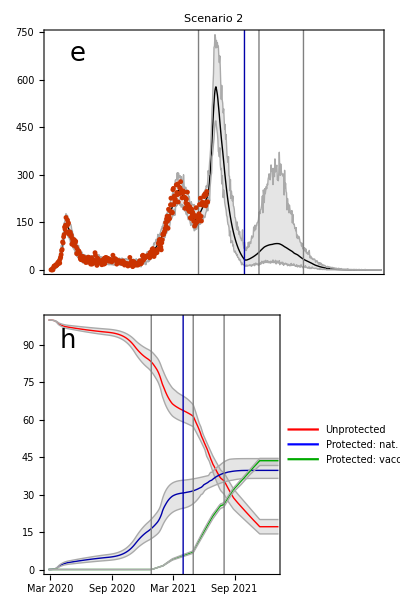

```mathematica
Unprotected=100 Total[Susceptible]/NNtot/.Demography;

ProtectedNatInf=100 Transpose[Accumulate[Transpose[Total[ProtectedNaturalInfection]]]]/NNtot/.Demography;

ProtectedVac=100 Transpose[Accumulate[Transpose[Total[ProtectedVaccine]]]]/NNtot/.Demography;

PlotProportions[tendplot_,onlydata_,plotlabel_,panel_,yaxislabel_,TickVar_]:=Show[DateListPlot[{ Median[Unprotected], Quantile[Unprotected,0.025],Quantile[Unprotected,0.975],Median[ProtectedNatInf], Quantile[ProtectedNatInf,0.025],Quantile[ProtectedNatInf,0.975],Median[ProtectedVac], Quantile[ProtectedVac,0.025],Quantile[ProtectedVac,0.975]},"February 25, 2020",FrameTicks->{{Automatic,None},{If[TickVar,ticks,None],None}},AspectRatio->AspRat,ImageSize->330,PlotRangePadding->None,PlotRange->{{"February 25, 2020",tendplot},{0,100}},Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,14],FrameLabel-> {{None,None},{None,None}},Filling->{{3->{2}},{6->{5}},{9->{8}}},PlotLegends->Placed[LineLegend[{Directive[Red,Thick],Directive[Blue,Thick],Directive[Darker[Green],Thick]},{"Unprotected","Protected: nat. infection","Protected: vaccination"}],Scaled[{{0.3, 0.50}, {0.5,0.5 }}](*{After,Top}*)] ,PlotStyle->{{Red,Thick},{Lighter[Gray],Thin},{Lighter[Gray],Thin},{Darker[Blue],Thick},{Lighter[Gray],Thin},{Lighter[Gray],Thin},{Darker[Green],Thick},{Lighter[Gray],Thin},{Lighter[Gray],Thin}},PlotLabel->If[TickVar,None,Style[Row[{plotlabel}],Black,14]],FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},Prolog->{Join[{Directive[{Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],Join[{Directive[{Darker[Blue]}],InfiniteLine[{DayPlus[{2020,02,25},x7],0},{0,1}]}]},ImagePadding->{{55, 5}, {Automatic, Automatic}}](*,PanelLetter[k]*),Graphics[Text[StyleForm[panel,FontSize->26],Scaled[{0.1,0.9}]]]];

(* Placed[BarChartLegends,Scaled[{{0.25, 0.50}, {0.5,0.5 }}](*{After,Top}*)] *)

Fig5h=PlotProportions["January 1, 2022",False,False,"h","Proportion (%)",True]

Print[Style["Date\nUnprotected\n Protected through natural infection\n Protected through vaccination",16,Blue,"Text"]];

{DateRange[{2020,02,25},{2022,1,10},{1,"Day"}],Median[Unprotected], Quantile[Unprotected,0.025],Quantile[Unprotected,0.975],Median[ProtectedNatInf], Quantile[ProtectedNatInf,0.025],Quantile[ProtectedNatInf,0.975],Median[ProtectedVac], Quantile[ProtectedVac,0.025],Quantile[ProtectedVac,0.975]}//MatrixForm

Grid[{{Fig5e},{Fig5h}}]
```

## Calculating average contact rate

```mathematica
Subscript[t, start]=0;
Subscript[t, end]=tendvac;
Subscript[t, step]=14;

nSamples=Dimensions[EstimatesData]⟦1⟧;
stepSamples=40;
ListSamples=Table[i,{i,1,nSamples,stepSamples}];

ParametersAllVaccination=Table[ParametersVaccination[i],{i,1,nSamples,stepSamples}];

AverageContactRateSampleAtTimet[sample_,tcont_]:=Sum[(Table[Total[Simplify[Simplify[ContactMatrix[tcont]/.ParametersAllVaccination⟦sample⟧]/.{Subscript[c, {k,l}]-> ContactDataPTBefore10Vespignani,Subscript[d, {k,l}]->ContactDataPTAfter10Vespignani }]⟦g,All⟧],{g,AgeGroups}])⟦k⟧ DemographyData10⟦k⟧/Total[DemographyData10],{k,AgeGroups}]

TrajectoriesContacts=Table[Table[AverageContactRateSampleAtTimet[i,t],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{i,1,Length[ListSamples]}];

Export["MathematicaFiles//Scenario2//TrajectoriesContacts.txt",TrajectoriesContacts,"Table"]
(*TrajectoriesContacts=Import["MathematicaFiles//Scenario2//TrajectoriesContacts.txt","Table"]*)
```

MathematicaFiles//Scenario2//TrajectoriesContacts.txt

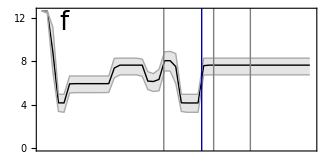

({2020,2,25} | {2020,3,10} | {2020,3,24} | {2020,4,7} | {2020,4,21} | {2020,5,5} | {2020,5,19} | {2020,6,2} | {2020,6,16} | {2020,6,30} | {2020,7,14} | {2020,7,28} | {2020,8,11} | {2020,8,25} | {2020,9,8} | {2020,9,22} | {2020,10,6} | {2020,10,20} | {2020,11,3} | {2020,11,17} | {2020,12,1} | {2020,12,15} | {2020,12,29} | {2021,1,12} | {2021,1,26} | {2021,2,9} | {2021,2,23} | {2021,3,9} | {2021,3,23} | {2021,4,6} | {2021,4,20} | {2021,5,4} | {2021,5,18} | {2021,6,1} | {2021,6,15} | {2021,6,29} | {2021,7,13} | {2021,7,27} | {2021,8,10} | {2021,8,24} | {2021,9,7} | {2021,9,21} | {2021,10,5} | {2021,10,19} | {2021,11,2} | {2021,11,16} | {2021,11,30} | {2021,12,14} | {2021,12,28}
12.6132 | 12.6131 | 8.83272 | 4.17259 | 4.16434 | 5.9183 | 5.93456 | 5.93457 | 5.93457 | 5.93457 | 5.93457 | 5.93457 | 5.93604 | 7.37227 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 6.16822 | 6.13163 | 6.32492 | 8.04618 | 8.04558 | 7.50549 | 4.17562 | 4.15934 | 4.15935 | 4.16424 | 7.58917 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646 | 7.63646
12.6104 | 12.4038 | 7.01082 | 3.38157 | 3.30457 | 5.07909 | 5.10961 | 5.10961 | 5.10961 | 5.10961 | 5.10961 | 5.10968 | 5.12441 | 6.46804 | 6.74308 | 6.74339 | 6.74335 | 6.74101 | 6.6104 | 5.39424 | 5.21349 | 5.27962 | 7.10651 | 7.08738 | 5.95783 | 3.38026 | 3.30409 | 3.30325 | 3.30343 | 6.72858 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339 | 6.74339
12.6132 | 12.6132 | 11.1201 | 4.95615 | 4.95614 | 6.63955 | 6.63955 | 6.63955 | 6.63955 | 6.63955 | 6.63955 | 6.63955 | 6.63955 | 8.26374 | 8.27907 | 8.27907 | 8.27905 | 8.27747 | 8.19373 | 7.03515 | 6.85717 | 7.25202 | 8.86239 | 8.90194 | 8.70089 | 4.95616 | 4.95614 | 4.95614 | 4.95614 | 8.27906 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907 | 8.27907)

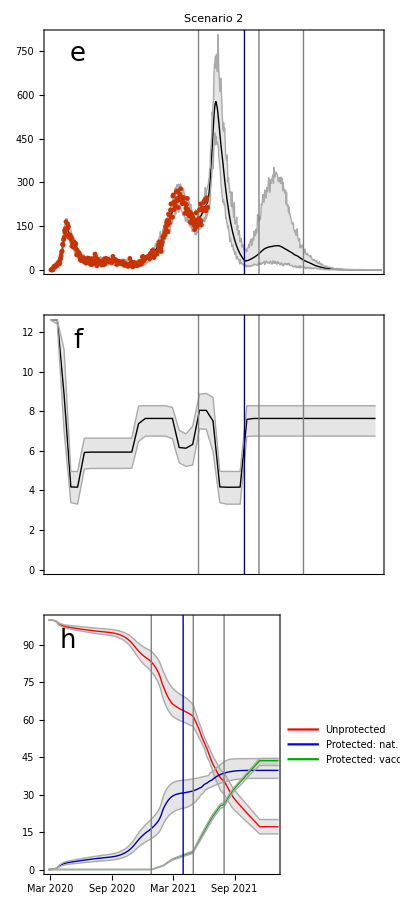

```mathematica
Fig5f=Show[DateListPlot[{Median[TrajectoriesContacts],Quantile[TrajectoriesContacts,0.025],Quantile[TrajectoriesContacts,0.975]},{"February 25, 2020",Automatic,{0,0,Subscript[t, step]}},
FrameTicks->{{Automatic,None},{None(*ticks*),None}},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,
Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,14],PlotRange->{{"February 25, 2020","January 1, 2022"},{0,Automatic}},
AxesOrigin->{"February 25, 2020",0},FrameLabel-> {{(*"Average contacts (1/day)"*)None,None},{None,None}},Filling->{3->{2}},PlotStyle->{{Black,Thick},{Lighter[Gray],Thin},{Lighter[Gray],Thin}},FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},Prolog->{Join[{Directive[{Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],Join[{Directive[{Darker[Blue]}],InfiniteLine[{DayPlus[{2020,02,25},x7],0},{0,1}]}]},ImagePadding->{{55, 5}, {Automatic, Automatic}}],Graphics[Text[StyleForm["f",FontSize->26],Scaled[{0.1,0.9}]]](*,PlotLabel->Style[Row[{"Model fit"}],Black,17]*)]

{DateRange[{2020,02,25},{2022,1,10},{14,"Day"}],Median[TrajectoriesContacts],Quantile[TrajectoriesContacts,0.025],Quantile[TrajectoriesContacts,0.975]}//MatrixForm

Grid[{{Fig5e},{Fig5f},{Fig5h}}]
```

```mathematica
Subscript[t, start]=0;
Subscript[t, end]=tendvac;
Subscript[t, step]=14; (* 3 for contact rates *)

nSamples=Dimensions[EstimatesData]⟦1⟧;
stepSamples=40; (* 50 for contact rates *)
ListSamples=Table[i,{i,1,nSamples,stepSamples}];

ParametersAllVaccination=Table[ParametersVaccination[i],{i,1,nSamples,stepSamples}];
ParametersAllNoVaccination=Table[ParametersNoVaccination[i],{i,1,nSamples,stepSamples}];
ParametersSteadyStateAll=Table[ParametersSteadyState[i],{i,1,nSamples,stepSamples}];

solutionCrI[Intervention_,sample_]:=NDSolve[Join[EqsList[Intervention],ICsList]/.ParametersAllVaccination⟦sample⟧,VarsList,{t,Subscript[t, start],Subscript[t, end]},Method->"StiffnessSwitching"];
solutionCrIAll=Table[solutionCrI["Estimation",i],{i,1,Length[ListSamples]}];

VarSampleAtTimet[var_,sample_,tRe_]:=(Evaluate[var/.First@solutionCrIAll⟦sample⟧])/.t-> tRe;

DiseaseState[sample_,tRe_]:=Flatten[Table[{Subscript[S,k][t]->VarSampleAtTimet[Subscript[S,k][t],sample,tRe],Subscript[EE,k][t]->0,Subscript[II,k][t]->0,Subscript[R,k][t]->VarSampleAtTimet[Subscript[R,k][t]+Subscript[EE,k][t]+Subscript[II,k][t]+Subscript[H,k][t],sample,tRe],Subscript[H,k][t]->0,Subscript[SV,k][t]->VarSampleAtTimet[Subscript[SV,k][t],sample,tRe],Subscript[EEV,k][t]->0,Subscript[IIV,k][t]->0,Subscript[RV,k][t]->VarSampleAtTimet[Subscript[RV,k][t]+Subscript[EEV,k][t]+Subscript[IIV,k][t]+Subscript[P,k][t]+Subscript[HV,k][t],sample,tRe],Subscript[P,k][t]->0,Subscript[HV,k][t]->0},{k,AgeGroups}]];

EqNumbersRe=Join[EqNumbers⟦NumAgeGroups+1;;3 NumAgeGroups⟧,EqNumbers⟦6 NumAgeGroups+1;;8 NumAgeGroups⟧];

JacobAnalyt=Table[ D[EqsList["Estimation"]⟦k,2⟧,VarsList⟦p⟧],{k,EqNumbersRe} ,{p,EqNumbersRe}];
TransmissionMatrix=ϵ Table[Coefficient[JacobAnalyt⟦k⟧⟦p⟧,ϵ],{k,1,Length[EqNumbersRe]} ,{p,1,Length[EqNumbersRe]}];
TransitionMatrix=JacobAnalyt-TransmissionMatrix;

TransmissionMatrixSampleAtTimet[sample_,tRe_]:=((TransmissionMatrix/.DiseaseState[sample,tRe])/.ParametersSteadyStateAll⟦sample⟧)/.t->tRe ;

TransitionMatrixSampleAtTimet[sample_,tRe_]:=((TransitionMatrix/.DiseaseState[sample,tRe])/.ParametersSteadyStateAll⟦sample⟧)/.t->tRe;

ReSampleAtTimet[sample_,tRe_]:=Re[Eigenvalues[-TransmissionMatrixSampleAtTimet[sample,tRe].Inverse[TransitionMatrixSampleAtTimet[sample,tRe]]]⟦1⟧];

Timing[TrajectoriesRe=Table[Table[ReSampleAtTimet[i,t],{t,Subscript[t, start],Subscript[t, end],Subscript[t, step]}],{i,1,Length[ListSamples]}]]

Export["MathematicaFiles//Scenario2//TrajectoriesRe.txt",TrajectoriesRe,"Table"]
(*TrajectoriesRe=Import["MathematicaFiles//Scenario2//TrajectoriesRe.txt","Table"]*)
(* 4 seconds 1 sample *)
```

{14591.5985,{{2.39321,2.38628,1.3957,0.662329,0.657219,0.98774,0.983762,0.979926,0.976255,0.972769,0.969481,0.966401,0.963547,1.20911,1.25934,1.24983,1.23461,1.21106,1.17642,0.919077,0.890651,0.868892,1.10987,1.12599,1.27605,0.659539,0.631603,0.618484,0.611507,1.2145,1.20447,1.18732,1.14996,1.11111,1.07109,1.03082,0.992546,0.959433,0.89687,0.822332,0.764302,0.71798,0.679219,0.647093,0.620715,0.600359,0.600259,0.600219,0.600203},{2.10785,2.10429,1.39313,0.739227,0.734671,0.985986,0.982926,0.979765,0.97676,0.973922,0.97126,0.968779,0.966986,1.18019,1.22152,1.21414,1.20228,1.18383,1.15151,0.930021,0.883605,0.988707,1.11302,1.09463,1.38813,0.762952,0.723255,0.702613,0.691647,1.18313,1.16888,1.14571,1.10018,1.05289,1.00574,0.961153,0.92215,0.891639,0.834674,0.765954,0.712185,0.668363,0.630685,0.598804,0.57233,0.551849,0.55184,0.551837,0.551836},{2.56379,2.53328,1.46719,0.654408,0.636045,0.979267,0.976446,0.973456,0.970621,0.967946,0.965434,0.963088,0.962445,1.22687,1.27539,1.26768,1.25528,1.23557,1.1831,0.930111,0.865563,0.854042,1.16312,1.23597,1.26135,0.69007,0.645786,0.630644,0.622548,1.28175,1.27021,1.2457,1.19559,1.13979,1.07935,1.01736,0.959056,0.910015,0.83825,0.76088,0.703239,0.658692,0.622069,0.591938,0.567268,0.548261,0.548182,0.548153,0.548142},{1.86925,1.86644,1.72656,0.762153,0.758005,0.984536,0.981528,0.978644,0.975921,0.973368,0.97099,0.968789,0.966763,1.2044,1.20115,1.19489,1.18485,1.1692,1.14509,0.944407,0.908382,0.895086,1.08985,1.0572,1.47565,0.821908,0.77829,0.754041,0.740591,1.19827,1.17993,1.14965,1.09235,1.03202,0.973097,0.920271,0.877205,0.84606,0.788549,0.717819,0.661501,0.614526,0.573353,0.538317,0.509497,0.48768,0.487679,0.487679,0.487679},{2.31861,2.2768,1.25488,0.722853,0.710334,0.980718,0.977886,0.975196,0.972672,0.970318,0.968136,0.966124,0.964278,1.21055,1.20702,1.20108,1.19159,1.17682,1.15175,0.956676,0.895485,0.890763,1.10305,1.1843,1.25907,0.799016,0.747578,0.727605,0.716926,1.24552,1.23132,1.20213,1.14452,1.07897,1.00987,0.944358,0.88939,0.849023,0.789598,0.723246,0.672721,0.631979,0.596921,0.567091,0.542141,0.522703,0.522699,0.522698,0.522697},{2.17075,2.16618,1.46282,0.696617,0.692325,0.98621,0.983142,0.979854,0.976715,0.973737,0.970931,0.968301,0.965854,1.21973,1.24434,1.23624,1.22324,1.20302,1.17301,0.899247,0.87587,1.0176,1.09477,1.07585,1.35714,0.720567,0.688708,0.671943,0.662701,1.2207,1.20756,1.18416,1.13469,1.0829,1.03041,0.979742,0.934475,0.898501,0.830117,0.746071,0.679113,0.623454,0.574724,0.533374,0.499749,0.474845,0.474841,0.47484,0.474839},{2.13522,2.13216,1.37086,0.733296,0.733233,0.977838,0.982221,0.979298,0.97652,0.973901,0.971447,0.969164,0.968193,1.16128,1.22057,1.21385,1.20278,1.18535,1.15875,0.938715,0.916063,0.899783,1.11366,1.10281,1.39198,0.776149,0.737499,0.717147,0.709804,1.17899,1.19479,1.16912,1.12015,1.06641,1.01067,0.95718,0.910621,0.874634,0.817416,0.75234,0.702589,0.662719,0.628735,0.599965,0.57588,0.557006,0.556994,0.55699,0.556989},{2.12595,2.12253,1.55507,0.68759,0.683932,0.981855,0.978912,0.976113,0.973465,0.970976,0.968649,0.966483,0.964507,1.21658,1.22908,1.22253,1.21212,1.19598,1.1719,0.932889,0.912533,0.896106,1.12239,1.12518,1.37055,0.743821,0.710146,0.692461,0.682791,1.25627,1.24081,1.21418,1.15989,1.09962,1.03598,0.973827,0.919022,0.876386,0.81018,0.735608,0.678865,0.633455,0.59479,0.562334,0.535658,0.515287,0.515278,0.515275,0.515274},{2.33327,2.32315,1.34005,0.693997,0.688053,0.974813,0.971908,0.968898,0.966082,0.963464,0.961042,0.958812,0.956768,1.25635,1.25185,1.24454,1.23288,1.21475,1.18272,0.915725,0.887963,0.951617,1.13955,1.18961,1.31743,0.734354,0.695539,0.676973,0.666907,1.23956,1.2274,1.20026,1.14681,1.08907,1.0295,0.971953,0.921095,0.881027,0.816035,0.741619,0.684601,0.638887,0.599996,0.567362,0.540511,0.519964,0.519947,0.519942,0.51994},{2.12549,2.12233,1.53006,0.700213,0.700979,0.976056,0.977433,0.974818,0.97235,0.970033,0.967869,0.965858,0.963997,1.23419,1.23377,1.22761,1.21774,1.20228,1.17552,0.930483,0.906079,0.89191,1.1843,1.17762,1.46396,0.752184,0.71337,0.692954,0.684383,1.20873,1.21826,1.18987,1.13625,1.07698,1.01526,0.956061,0.904723,0.865187,0.806039,0.740379,0.690695,0.651288,0.618014,0.590049,0.566765,0.548587,0.548566,0.548559,0.548557},{2.06649,2.06272,1.64379,0.701881,0.702161,0.979785,0.981082,0.978121,0.975305,0.972645,0.970145,0.967809,0.965637,1.23946,1.2378,1.23059,1.21906,1.20093,1.16131,0.949822,0.882767,0.866103,1.10763,1.07684,1.43804,0.747957,0.714322,0.696259,0.688723,1.21902,1.23002,1.20333,1.14973,1.09105,1.02989,0.970622,0.918446,0.877736,0.812025,0.73682,0.679198,0.632867,0.593328,0.56015,0.532949,0.51226,0.512251,0.512248,0.512247},{1.97275,1.96976,1.55916,0.739877,0.73582,0.987089,0.984197,0.981425,0.978786,0.976288,0.97394,0.971744,0.969703,1.21152,1.20988,1.20341,1.19298,1.17643,1.13734,0.949632,0.897661,0.89574,1.10057,1.07474,1.42395,0.791109,0.75079,0.729327,0.717804,1.20846,1.19235,1.16566,1.11412,1.05826,1.00135,0.9479,0.902382,0.868028,0.810377,0.743111,0.691139,0.648982,0.612743,0.582058,0.556562,0.536832,0.536828,0.536826,0.536826},{2.08011,2.07749,1.62602,0.729075,0.725774,0.978118,0.97595,0.973621,0.971434,0.969391,0.967491,0.965731,0.964205,1.2165,1.22731,1.22183,1.213,1.19904,1.17775,0.932391,0.915053,0.901151,1.10618,1.08088,1.47489,0.821505,0.78173,0.758374,0.744704,1.28324,1.26025,1.21813,1.14075,1.053,0.965192,0.889014,0.831243,0.792598,0.739266,0.680059,0.634949,0.598453,0.567003,0.540244,0.517853,0.500378,0.500375,0.500374,0.500374},{2.18633,2.18179,1.69234,0.678477,0.674957,0.985885,0.984487,0.981022,0.977702,0.97454,0.97155,0.968739,0.96632,1.19112,1.25792,1.24909,1.23482,1.21248,1.16929,0.932175,0.874848,0.866197,1.12445,1.09358,1.40038,0.682841,0.653212,0.638269,0.630718,1.20226,1.20128,1.18166,1.13965,1.09598,1.05147,1.0076,0.967095,0.933399,0.868738,0.790779,0.729927,0.680847,0.639225,0.604539,0.576219,0.554692,0.554662,0.554652,0.554648},{2.34842,2.33614,1.37967,0.696665,0.688436,0.987827,0.984692,0.981667,0.97877,0.976012,0.973401,0.970945,0.968646,1.22351,1.23127,1.22425,1.21312,1.19595,1.16945,0.964894,0.863414,0.863594,1.12383,1.17677,1.28786,0.740335,0.700885,0.683193,0.673636,1.23882,1.22411,1.19934,1.14943,1.09492,1.03778,0.981627,0.931271,0.891103,0.827493,0.755637,0.700943,0.657411,0.62057,0.589636,0.564007,0.544165,0.544144,0.544137,0.544135},{2.08956,2.08544,1.56668,0.680721,0.676737,0.987786,0.984401,0.981133,0.978007,0.975036,0.972231,0.969665,0.972279,1.13087,1.23897,1.23365,1.22117,1.2016,1.17239,0.93479,0.911798,0.893666,1.13055,1.13213,1.35403,0.707493,0.675933,0.660189,0.65185,1.23214,1.22046,1.19935,1.15515,1.10727,1.05672,1.00588,0.958647,0.91936,0.853753,0.778893,0.721897,0.676837,0.639093,0.607726,0.581971,0.562169,0.562137,0.562127,0.562123},{2.21374,2.20967,1.52325,0.690672,0.686801,0.980702,0.977527,0.974507,0.971654,0.968974,0.966472,0.964147,0.962561,1.22086,1.24566,1.23821,1.2263,1.20778,1.17738,0.920126,0.878779,0.959605,1.10591,1.0904,1.37639,0.732423,0.70004,0.682688,0.673037,1.24876,1.23331,1.20707,1.15294,1.09457,1.03422,0.975705,0.923845,0.883122,0.813886,0.73234,0.6687,0.616617,0.571489,0.533369,0.502295,0.479071,0.479065,0.479064,0.479063},{2.1265,2.12188,1.39842,0.716788,0.716972,0.972266,0.987295,0.983572,0.979971,0.976541,0.973298,0.970257,0.967422,1.19166,1.24011,1.23101,1.21621,1.19297,1.15733,0.931119,0.901212,0.925141,1.12424,1.10592,1.33832,0.690428,0.656476,0.64025,0.638811,1.08974,1.1234,1.10657,1.06858,1.0314,0.995673,0.962111,0.932332,0.908885,0.848988,0.768645,0.702274,0.645645,0.595367,0.552467,0.517529,0.491655,0.491653,0.491653,0.491653},{2.06111,2.05739,1.47425,0.725155,0.7222,0.970006,0.991438,0.988217,0.985078,0.982055,0.979165,0.976419,0.974168,1.121,1.22354,1.21588,1.20333,1.18384,1.15502,0.909103,0.887147,0.948877,1.11004,1.10645,1.38169,0.73625,0.699582,0.681102,0.675316,1.14031,1.16056,1.14003,1.09747,1.05407,1.01114,0.970382,0.934265,0.905664,0.846469,0.772539,0.713776,0.66531,0.623359,0.587921,0.558786,0.536614,0.536607,0.536605,0.536605},{2.30982,2.3054,1.35433,0.716081,0.711269,0.983216,0.979271,0.975494,0.97192,0.968562,0.96543,0.962528,0.95986,1.23407,1.258,1.24873,1.23365,1.20998,1.17402,0.923053,0.871358,0.855561,1.15104,1.1058,1.45006,0.684708,0.65027,0.633394,0.624624,1.14225,1.13113,1.11342,1.0754,1.03809,1.00217,0.968424,0.9385,0.914772,0.858387,0.785047,0.725779,0.676343,0.63331,0.596885,0.566938,0.544168,0.544158,0.544155,0.544154},{2.16913,2.16398,1.39863,0.697516,0.692548,0.981732,0.978163,0.974776,0.971583,0.968596,0.965832,0.963799,0.979905,1.16423,1.23332,1.22786,1.21479,1.19436,1.16405,0.94154,0.91364,0.898562,1.12197,1.13722,1.31172,0.703955,0.670542,0.654507,0.646101,1.19084,1.17947,1.16076,1.12099,1.08,1.03859,0.998161,0.96116,0.930676,0.870873,0.798242,0.741388,0.69539,0.656261,0.623465,0.596424,0.575602,0.575575,0.575566,0.575563},{2.04124,2.03778,1.77183,0.695976,0.692382,0.982535,0.979645,0.976874,0.974247,0.971771,0.96945,0.967285,0.96534,1.23127,1.23812,1.23114,1.21993,1.20222,1.15366,0.942997,0.9108,0.913858,1.12518,1.09871,1.45399,0.744205,0.710166,0.692107,0.682253,1.25145,1.23626,1.20997,1.15748,1.09902,1.03702,0.976077,0.921916,0.879311,0.815194,0.744337,0.691005,0.6489,0.61348,0.583882,0.559454,0.540589,0.540571,0.540566,0.540564},{2.11097,2.10628,1.52908,0.689585,0.685731,0.985937,0.982806,0.97935,0.976058,0.972943,0.970017,0.967285,0.964749,1.24283,1.23797,1.22933,1.21551,1.19414,1.16249,0.922598,0.886992,0.868846,1.11596,1.08269,1.40889,0.695198,0.6651,0.650187,0.642499,1.19225,1.18671,1.16894,1.13141,1.09211,1.05161,1.0112,0.973343,0.941235,0.881167,0.809858,0.754541,0.710351,0.673227,0.642308,0.6168,0.597035,0.596979,0.596958,0.59695},{2.3102,2.30522,1.69648,0.656058,0.651742,0.983317,0.979606,0.976051,0.972668,0.96947,0.966466,0.963659,0.961986,1.19224,1.26763,1.25893,1.24491,1.22325,1.18816,0.961341,0.872486,0.906543,1.13566,1.12792,1.34887,0.659195,0.630804,0.616485,0.608706,1.21968,1.20757,1.18743,1.14346,1.09832,1.05278,1.00822,0.967275,0.933452,0.865482,0.78139,0.714658,0.659941,0.612891,0.573501,0.54159,0.517789,0.517768,0.517762,0.517759},{2.08347,2.08086,1.66553,0.721491,0.718736,0.984175,0.983689,0.981705,0.979803,0.977988,0.976261,0.974626,0.973082,1.22846,1.22577,1.22084,1.21303,1.20092,1.18263,0.918761,0.904663,0.89672,1.12769,1.09976,1.56074,0.838928,0.799566,0.775583,0.761176,1.31393,1.28607,1.2345,1.1435,1.03836,0.935575,0.851136,0.791109,0.753237,0.703682,0.649259,0.607858,0.574302,0.545302,0.520534,0.499706,0.483354,0.483351,0.483351,0.483351},{2.22948,2.21427,1.35725,0.706915,0.696742,0.983561,0.981499,0.978856,0.976341,0.973961,0.97172,0.969622,0.968258,1.18772,1.23276,1.22638,1.21611,1.20001,1.16829,0.944496,0.895733,0.879929,1.11734,1.1811,1.2833,0.768545,0.725172,0.706118,0.695778,1.25525,1.24183,1.21278,1.15582,1.09163,1.02375,0.958273,0.901762,0.858796,0.795786,0.726291,0.673844,0.632074,0.59656,0.566638,0.541815,0.522606,0.522596,0.522593,0.522592},{2.19341,2.18915,1.4533,0.693972,0.697623,0.977076,0.979025,0.976106,0.973343,0.970746,0.968319,0.966063,0.964024,1.22225,1.23259,1.2256,1.21442,1.19702,1.17063,0.920689,0.894265,0.910931,1.11932,1.1392,1.33324,0.739218,0.70475,0.687299,0.682036,1.20694,1.22807,1.20314,1.15255,1.09687,1.0382,0.980497,0.928872,0.887912,0.822988,0.749645,0.693864,0.649401,0.611703,0.580079,0.553987,0.533918,0.533904,0.533899,0.533898},{2.20749,2.20326,1.56342,0.716882,0.712031,0.981261,0.977874,0.974217,0.970767,0.967536,0.964529,0.96175,0.959631,1.16197,1.25933,1.25087,1.23682,1.21452,1.17904,0.925602,0.894971,0.875051,1.15155,1.12229,1.40926,0.70135,0.666026,0.64847,0.639351,1.16744,1.15635,1.13715,1.0978,1.058,1.01868,0.981079,0.947266,0.919852,0.863003,0.792622,0.737092,0.691812,0.653073,0.620503,0.593609,0.572887,0.572861,0.572852,0.572848},{2.29617,2.29084,1.52372,0.689063,0.684571,0.977648,0.973702,0.969967,0.966457,0.963182,0.960144,0.957342,0.954788,1.26606,1.26746,1.25817,1.24335,1.22044,1.1867,0.907606,0.880939,0.866004,1.13972,1.0945,1.50689,0.684274,0.653532,0.637769,0.629324,1.20511,1.19262,1.17255,1.13181,1.08942,1.04619,1.00359,0.964174,0.931077,0.870291,0.798359,0.742557,0.69796,0.660496,0.629332,0.603678,0.583853,0.583775,0.583743,0.583731},{2.34682,2.34319,1.5559,0.667628,0.666573,0.977763,0.975634,0.973102,0.970703,0.96844,0.966316,0.964329,0.962831,1.22365,1.26667,1.26035,1.25025,1.23452,1.21075,0.909079,0.891872,0.902506,1.14379,1.12283,1.47423,0.747512,0.716436,0.698795,0.688988,1.33042,1.32034,1.28368,1.2134,1.1284,1.03433,0.942787,0.865692,0.809374,0.743646,0.678137,0.630634,0.593973,0.56343,0.537889,0.516645,0.500052,0.500029,0.500021,0.500018},{2.23345,2.22896,1.46183,0.706774,0.701826,0.980342,0.977849,0.975482,0.973247,0.971146,0.96918,0.967349,0.965651,1.22714,1.22358,1.21785,1.2088,1.19472,1.16206,0.954035,0.905384,0.912893,1.08413,1.12178,1.32652,0.807827,0.771561,0.751231,0.739109,1.31337,1.29093,1.25032,1.17097,1.07939,0.985382,0.901889,0.837611,0.794348,0.735207,0.669513,0.619228,0.578258,0.542733,0.512529,0.487499,0.468297,0.468295,0.468295,0.468295},{2.0803,2.0763,1.49858,0.709252,0.705342,0.98506,0.981538,0.978165,0.974964,0.971945,0.969119,0.966488,0.964347,1.18815,1.23219,1.22434,1.21177,1.19229,1.1632,0.936931,0.910921,0.892438,1.13447,1.10256,1.42994,0.71988,0.68502,0.667556,0.658443,1.1863,1.17464,1.15492,1.11456,1.07263,1.03016,0.988814,0.951209,0.920411,0.862137,0.792266,0.737865,0.694033,0.656838,0.62565,0.599849,0.579871,0.579843,0.579833,0.57983},{2.2686,2.26456,1.45947,0.703796,0.69964,0.987162,0.983896,0.980557,0.977363,0.97433,0.971468,0.968783,0.966372,1.23338,1.23316,1.22456,1.2111,1.19066,1.16103,0.905372,0.880219,0.909848,1.13366,1.08998,1.51402,0.706495,0.673098,0.656283,0.647437,1.17626,1.16572,1.1466,1.10693,1.06653,1.02628,0.987493,0.952378,0.923741,0.865745,0.7944,0.738175,0.692374,0.653191,0.620211,0.592935,0.571889,0.571862,0.571853,0.57185},{2.39644,2.38995,1.45145,0.664403,0.659573,0.976305,0.972777,0.969433,0.966291,0.963355,0.960627,0.958108,0.958045,1.24109,1.26861,1.2601,1.24654,1.22554,1.18621,0.942313,0.870154,0.861828,1.14699,1.16356,1.32305,0.681069,0.649318,0.633522,0.624849,1.22945,1.21564,1.19227,1.14253,1.0909,1.03872,0.988089,0.942282,0.9053,0.833044,0.742962,0.670335,0.609276,0.555152,0.508794,0.471121,0.443632,0.443626,0.443625,0.443625},{2.20258,2.199,1.54779,0.69274,0.692028,0.976248,0.979141,0.976318,0.973641,0.971117,0.968751,0.966544,0.964546,1.21015,1.23765,1.231,1.22044,1.20408,1.17943,0.915669,0.865853,0.958217,1.12725,1.12044,1.39132,0.746919,0.712465,0.693958,0.686124,1.2272,1.23716,1.20867,1.15172,1.08936,1.0247,0.962644,0.908708,0.867244,0.800508,0.723623,0.664296,0.616149,0.574687,0.539724,0.511084,0.489437,0.489431,0.489429,0.489429},{2.45856,2.45153,1.69991,0.593893,0.598263,0.975411,0.974031,0.970731,0.967609,0.964671,0.961921,0.95936,0.956994,1.28604,1.28147,1.27253,1.25852,1.23713,1.20301,0.979556,0.834216,0.908418,1.13772,1.17271,1.28349,0.61619,0.590886,0.579494,0.575759,1.25612,1.27528,1.25491,1.209,1.16017,1.10867,1.05585,1.00496,0.960664,0.881617,0.789024,0.717531,0.660668,0.613015,0.573792,0.542337,0.518998,0.518942,0.518922,0.518914},{2.08864,2.08589,1.70861,0.705286,0.719563,0.971133,0.987905,0.985571,0.983228,0.980977,0.978828,0.976804,0.977076,1.10312,1.22485,1.22123,1.21203,1.19748,1.17043,0.928351,0.876482,0.971716,1.10028,1.07697,1.50342,0.789722,0.754522,0.734828,0.740626,1.21439,1.26801,1.23273,1.16312,1.08261,0.998491,0.921395,0.859727,0.816619,0.756534,0.690263,0.639954,0.599359,0.564449,0.534904,0.510435,0.491606,0.491603,0.491602,0.491602},{2.24552,2.24091,1.42802,0.691442,0.687022,0.984452,0.98133,0.97834,0.975496,0.972805,0.970274,0.967911,0.967068,1.15522,1.24088,1.23414,1.22283,1.20514,1.17857,0.914776,0.89285,0.877698,1.12681,1.14565,1.33918,0.734871,0.700767,0.683451,0.674126,1.25051,1.23567,1.21059,1.16073,1.10479,1.04473,0.984718,0.93035,0.886677,0.822012,0.751298,0.69825,0.656606,0.621729,0.592583,0.568428,0.549648,0.549621,0.549611,0.549608},{2.0141,2.01092,1.54352,0.750238,0.745974,0.981388,0.980384,0.977451,0.97468,0.972081,0.969658,0.967429,0.969645,1.17165,1.21619,1.20953,1.19845,1.18112,1.15525,0.935182,0.913827,0.917536,1.14582,1.11383,1.51405,0.775184,0.730717,0.707855,0.696058,1.16096,1.14936,1.12622,1.08237,1.03722,0.9927,0.951105,0.915045,0.887034,0.833382,0.768246,0.717194,0.675534,0.63969,0.609297,0.583941,0.564194,0.564185,0.564182,0.564181},{2.26204,2.25807,1.44466,0.715465,0.711111,0.98725,0.983908,0.980691,0.977612,0.974683,0.971915,0.969313,0.967127,1.18629,1.24757,1.23959,1.22677,1.20681,1.17379,0.931618,0.89863,0.879644,1.11477,1.08255,1.41992,0.734372,0.699483,0.68102,0.670975,1.21147,1.19666,1.17276,1.1255,1.07569,1.02506,0.976232,0.932653,0.897762,0.836546,0.764608,0.708952,0.664144,0.626009,0.593973,0.567505,0.547104,0.547082,0.547075,0.547072},{2.31126,2.30834,1.58892,0.683551,0.680578,0.985185,0.982874,0.980648,0.978513,0.976474,0.974535,0.972697,0.970995,1.23068,1.24104,1.23536,1.22645,1.21274,1.19212,0.905532,0.889041,0.876816,1.13414,1.13801,1.42504,0.785507,0.752204,0.732822,0.721371,1.34048,1.31735,1.27567,1.19588,1.10073,0.999823,0.907766,0.835553,0.78624,0.726416,0.664406,0.618528,0.58221,0.55131,0.525178,0.503372,0.486373,0.486366,0.486363,0.486363},{2.37922,2.3751,1.55175,0.67956,0.675728,0.978685,0.975327,0.97214,0.969133,0.966313,0.963683,0.961247,0.960949,1.18602,1.26708,1.25964,1.2472,1.22771,1.19488,0.907264,0.881514,0.865788,1.14797,1.13484,1.40596,0.711938,0.679911,0.663012,0.653783,1.26114,1.24569,1.21991,1.16869,1.11219,1.05221,0.992415,0.937905,0.893544,0.826435,0.752543,0.696994,0.653438,0.617086,0.586867,0.561985,0.542779,0.542737,0.542722,0.542717},{2.10574,2.10225,1.66136,0.738847,0.73462,0.987482,0.984374,0.981335,0.978428,0.975663,0.973051,0.970596,0.968302,1.21563,1.2286,1.22139,1.20998,1.19239,1.16642,0.91982,0.897418,0.880045,1.13726,1.0978,1.52933,0.768419,0.727586,0.70558,0.693568,1.18919,1.17238,1.14601,1.09583,1.04406,0.993148,0.945895,0.905327,0.874183,0.815783,0.74473,0.688762,0.642794,0.603031,0.569373,0.541591,0.520341,0.520335,0.520333,0.520332},{2.36659,2.30994,1.28203,0.723792,0.703895,0.988868,0.985867,0.982041,0.978379,0.974901,0.971624,0.968558,0.96571,1.24136,1.23678,1.22712,1.21161,1.1876,1.15254,0.932296,0.901428,0.880512,1.13105,1.2003,1.19104,0.695286,0.642563,0.626988,0.619378,1.12508,1.1174,1.10294,1.07132,1.04038,1.0105,0.982185,0.956754,0.93621,0.886303,0.821979,0.770436,0.727838,0.691021,0.659742,0.633576,0.613103,0.613076,0.613065,0.613061},{2.22861,2.22493,1.54598,0.71458,0.710047,0.986697,0.983078,0.979606,0.9763,0.973175,0.970242,0.967506,0.964971,1.22541,1.23338,1.22513,1.2119,1.19135,1.16057,0.913826,0.880261,0.959439,1.10821,1.06843,1.44459,0.723566,0.689759,0.672571,0.663453,1.18838,1.1759,1.15556,1.11319,1.06949,1.02562,0.983334,0.945287,0.914597,0.854158,0.780208,0.722009,0.674487,0.633654,0.599232,0.570853,0.549115,0.549102,0.549097,0.549096},{2.16167,2.15722,1.5102,0.69461,0.690552,0.988343,0.98542,0.982134,0.978979,0.97597,0.973119,0.970433,0.967917,1.24272,1.24245,1.23423,1.22118,1.20103,1.16429,0.938415,0.886652,0.87,1.12105,1.0905,1.417,0.713483,0.681057,0.664278,0.655237,1.21324,1.2022,1.18033,1.13512,1.08765,1.03917,0.99181,0.948829,0.913825,0.850536,0.775535,0.717373,0.67057,0.630841,0.597617,0.570342,0.549476,0.549452,0.549444,0.549442},{2.19785,2.19309,1.51656,0.685687,0.680256,0.985994,0.982849,0.979697,0.97669,0.973841,0.971159,0.968647,0.966308,1.23511,1.23848,1.23086,1.21863,1.19958,1.17121,0.907016,0.883487,0.871914,1.1111,1.1347,1.30481,0.716846,0.684505,0.66874,0.660332,1.23614,1.22498,1.20327,1.15831,1.10905,1.05656,1.00355,0.954312,0.913471,0.848009,0.774456,0.71874,0.674856,0.63815,0.607586,0.582376,0.562875,0.56284,0.562828,0.562824},{2.29486,2.29012,1.48439,0.688711,0.684077,0.988759,0.98526,0.981878,0.97863,0.975533,0.972597,0.969831,0.96724,1.25417,1.25114,1.2428,1.22948,1.20885,1.17743,0.926871,0.897744,0.884061,1.15838,1.16154,1.35677,0.692999,0.659214,0.642518,0.63369,1.1922,1.17946,1.15882,1.1155,1.07126,1.02716,0.984771,0.94658,0.915716,0.852607,0.774074,0.711653,0.660265,0.615881,0.578509,0.547968,0.524926,0.524913,0.524909,0.524908},{2.19888,2.19473,1.5728,0.678539,0.674671,0.988757,0.98548,0.982313,0.979272,0.976372,0.973621,0.97103,0.969551,1.15581,1.24776,1.2401,1.22733,1.20734,1.17435,0.925345,0.890571,0.883434,1.14309,1.1171,1.42147,0.695536,0.664417,0.648793,0.64052,1.2207,1.20846,1.18802,1.14502,1.09948,1.05233,1.00548,0.96215,0.926109,0.861938,0.78677,0.728838,0.682605,0.643661,0.611224,0.584594,0.564151,0.564116,0.564104,0.5641},{2.60068,2.57904,1.35949,0.687898,0.680105,0.979158,0.981934,0.978741,0.975692,0.972797,0.970065,0.967514,0.968004,1.16304,1.25287,1.2457,1.23325,1.21397,1.18009,0.931094,0.887131,0.870101,1.15693,1.21418,1.29051,0.715014,0.674121,0.657053,0.649434,1.20906,1.21539,1.1921,1.14641,1.09684,1.04477,0.992895,0.945167,0.905707,0.842728,0.771724,0.717591,0.674798,0.638948,0.60901,0.584181,0.564834,0.564776,0.564755,0.564748}}}

MathematicaFiles//Scenario2//TrajectoriesRe.txt

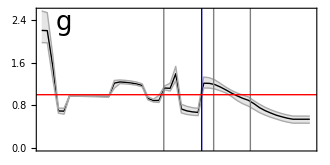

({2020,2,25} | {2020,3,10} | {2020,3,24} | {2020,4,7} | {2020,4,21} | {2020,5,5} | {2020,5,19} | {2020,6,2} | {2020,6,16} | {2020,6,30} | {2020,7,14} | {2020,7,28} | {2020,8,11} | {2020,8,25} | {2020,9,8} | {2020,9,22} | {2020,10,6} | {2020,10,20} | {2020,11,3} | {2020,11,17} | {2020,12,1} | {2020,12,15} | {2020,12,29} | {2021,1,12} | {2021,1,26} | {2021,2,9} | {2021,2,23} | {2021,3,9} | {2021,3,23} | {2021,4,6} | {2021,4,20} | {2021,5,4} | {2021,5,18} | {2021,6,1} | {2021,6,15} | {2021,6,29} | {2021,7,13} | {2021,7,27} | {2021,8,10} | {2021,8,24} | {2021,9,7} | {2021,9,21} | {2021,10,5} | {2021,10,19} | {2021,11,2} | {2021,11,16} | {2021,11,30} | {2021,12,14} | {2021,12,28}
2.20073 | 2.19687 | 1.5199 | 0.696641 | 0.692465 | 0.982875 | 0.981533 | 0.978693 | 0.975806 | 0.972801 | 0.970105 | 0.96751 | 0.965782 | 1.21654 | 1.23804 | 1.23093 | 1.21885 | 1.20098 | 1.17155 | 0.930297 | 0.890611 | 0.893052 | 1.12482 | 1.11877 | 1.39165 | 0.733388 | 0.697511 | 0.678997 | 0.668941 | 1.21444 | 1.21193 | 1.18895 | 1.14299 | 1.08836 | 1.02969 | 0.977987 | 0.932492 | 0.895653 | 0.833213 | 0.758258 | 0.702431 | 0.658051 | 0.61755 | 0.587394 | 0.560719 | 0.541684 | 0.541654 | 0.541644 | 0.54164
1.97275 | 1.96976 | 1.28203 | 0.654408 | 0.636045 | 0.971133 | 0.972777 | 0.969433 | 0.966291 | 0.963355 | 0.960627 | 0.958108 | 0.956768 | 1.121 | 1.20702 | 1.20108 | 1.19159 | 1.17643 | 1.14509 | 0.905372 | 0.863414 | 0.855561 | 1.08985 | 1.06843 | 1.25907 | 0.659195 | 0.630804 | 0.616485 | 0.608706 | 1.12508 | 1.1234 | 1.10657 | 1.07132 | 1.03202 | 0.965192 | 0.889014 | 0.831243 | 0.78624 | 0.726416 | 0.664406 | 0.618528 | 0.578258 | 0.545302 | 0.512529 | 0.487499 | 0.468297 | 0.468295 | 0.468295 | 0.468295
2.56379 | 2.53328 | 1.72656 | 0.750238 | 0.745974 | 0.988759 | 0.987905 | 0.985571 | 0.983228 | 0.980977 | 0.978828 | 0.976419 | 0.977076 | 1.26606 | 1.27539 | 1.26768 | 1.25528 | 1.23557 | 1.20301 | 0.964894 | 0.915053 | 0.988707 | 1.16312 | 1.21418 | 1.52933 | 0.821908 | 0.78173 | 0.758374 | 0.744704 | 1.33042 | 1.31735 | 1.27567 | 1.209 | 1.13979 | 1.07935 | 1.03082 | 0.992546 | 0.959433 | 0.886303 | 0.821979 | 0.764302 | 0.71798 | 0.679219 | 0.647093 | 0.620715 | 0.600359 | 0.600259 | 0.600219 | 0.600203)

```mathematica
Fig5g=Show[DateListPlot[{Median[TrajectoriesRe],Quantile[TrajectoriesRe,0.025],Quantile[TrajectoriesRe,0.975]},{"February 25, 2020",Automatic,{0,0,Subscript[t, step]}},
FrameTicks->{{Automatic,None},{None,None}},AspectRatio->AspRat,ImageSize->ImSize,PlotRangePadding->None,
Frame-> {{True,False},{True,False}},PlotTheme->"Web",FrameStyle->Directive[Black,14],PlotRange->{{"February 25, 2020","January 1, 2022"},{0,Automatic}},
AxesOrigin->{"February 25, 2020",0},FrameLabel-> {{None(*"R_e"*),None},{None,None}},Filling->{3->{2}},PlotStyle->{{Black,Thick},{Lighter[Gray],Thin},{Lighter[Gray],Thin}},FrameTicksStyle->{{{Black,14,Opacity[1]},None},{{Black,14,Opacity[1]},None}},
Prolog->{Join[{Directive[{Gray}]},Table[InfiniteLine[{UniqueStartVaccinationDates⟦i⟧,0},{0,1}],{i,1,Length[UniqueStartVaccinationDates]}]],Join[{Directive[{Darker[Blue]}],InfiniteLine[{DayPlus[{2020,02,25},x7],0},{0,1}]}],{Directive[{Thick,Red}],InfiniteLine[{{0,1},{2,1}}]}},ImagePadding->{{55, 5}, {Automatic, Automatic}}(*,PlotLabel->Style[Row[{"Model fit"}],Black,17]*)],Graphics[Text[StyleForm["g",FontSize->26],Scaled[{0.1,0.9}]]]]

{DateRange[{2020,02,25},{2022,1,10},{14,"Day"}],Median[TrajectoriesRe],Quantile[TrajectoriesRe,0.025],Quantile[TrajectoriesRe,0.975]}//MatrixForm
```

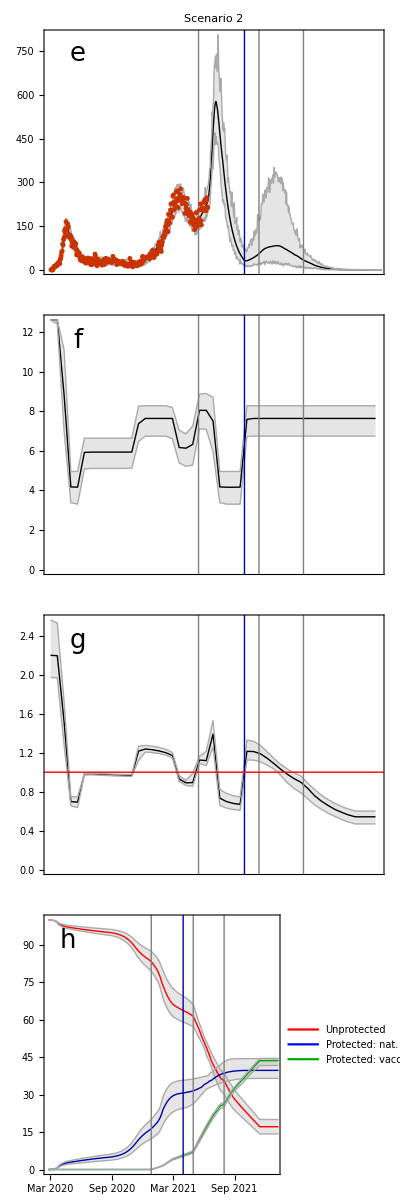

Figures//Fig6b.pdf

Figures//Fig6b.eps

```mathematica
fig6b=Grid[{{Fig5e},{Fig5f},{Fig5g},{Fig5h}}]
Export[StringJoin["Figures//Fig6b.pdf"],fig6b]
Export[StringJoin["Figures//Fig6b.eps"],fig6b]
```

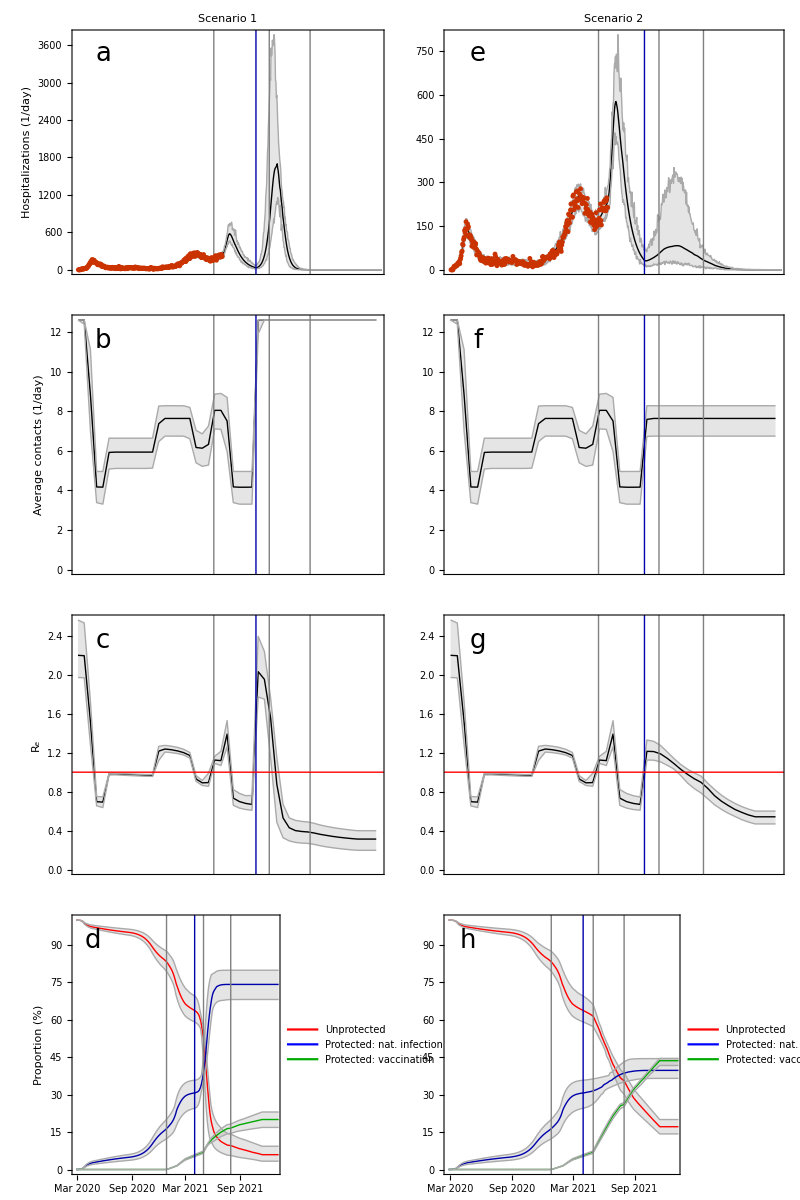

Figures//Fig6.pdf

Figures//Fig6.eps

```mathematica
fig6=Grid[{{Fig5a,Fig5e},{Fig5b,Fig5f},{Fig5c,Fig5g},{Fig5d,Fig5h}}]

Export[StringJoin["Figures//Fig6.pdf"],fig6]
Export[StringJoin["Figures//Fig6.eps"],fig6]
```